```mathematica
sphere[x_]:=Module[
{},Sum[(x[[i]])^2,{i,Length@x}]]
```

```mathematica
GA[f_,dim_]:=Module[{G,Solution1,nextGeneration,nextGenerationX,parent1,parent2,parents,parentsX,momX,dadX,momXCross,dadXCross,momXOrig,dadXOrig,child1,child2},
G1=RandomReal[{-500,500},{50,dim}];


G={};

Solution={};

(*2While generation number G<=2000*)
For[a=1,a<=2000,a++,
G1=Round[G1,0.001];
AppendTo[G,G1];

Solution1=Table[f[G1[[i]]],{i,50}];
AppendTo[Solution,Min@Solution1];

nextGeneration=TakeSmallest[Solution1,10];
nextGenerationX=G1[[Ordering[Solution1,10]]];
G1={};
For[k=1,k<=20,k++,

(*Ranking Selection*)
parent1=RandomChoice[Table[i/((10+1)*10/2),{i,10}]->Reverse@nextGeneration];


parent2=RandomChoice[Table[i/((9+1)*9/2),{i,9}]->Reverse[ReplacePart[nextGeneration,First@First@Position[nextGeneration,parent1]->Nothing]]];

parents={parent1,parent2};


parentsX=nextGenerationX[[
Join[
Flatten@Position[
nextGeneration,parents[[1]]
],
Flatten@Position[
nextGeneration,parents[[2]]
]
]
]];
parentsX=Round[(parentsX+500)*1000];
parentsX=IntegerDigits[parentsX,10,7];
parentsX=IntegerDigits[parentsX,2,4];
momX=parentsX[[1]];
dadX=parentsX[[2]];
momX=Flatten@momX;
dadX=Flatten@dadX;
(*One-point crossover, exchange 1/dim length of parents' binary numbers*)

momXCross=Take[momX,(Length@momX)/dim];
momXOrig=Drop[momX,(Length@momX)/dim];
dadXCross=Take[dadX,(Length@dadX)/dim];
dadXOrig=Drop[dadX,(Length@dadX)/dim];
child1=Join[momXCross,dadXOrig];
child2=Join[dadXCross,momXOrig];
(*Random-Mutation*)
For[i=1,i<=Length@child1,i++,If[RandomReal[]<=0.01,If[child1[[i]]==0,child1[[i]]=1,child1[[i]]=0]]];
For[i=1,i<=Length@child2,i++,If[RandomReal[]<=0.01,If[child2[[i]]==0,child2[[i]]=1,child2[[i]]=0]]];
child1=Partition[child1,4];
child1=Partition[child1,7];
child2=Partition[Partition[child2,4],7];
child1=Table[Table[FromDigits[child1[[i]][[j]],2],{j,7}],{i,dim}];

child1=Table[FromDigits[child1[[i]]],{i,dim}];
child1=child1/1000-500//N;
For[i=1,i<=Length@child1,i++,If[child1[[i]]<-500,child1[[i]]=-500,If[child1[[i]]>500,child1[[i]]=500]]];

child2=Table[Table[FromDigits[child2[[i]][[j]],2],{j,7}],{i,dim}];
child2=Table[FromDigits[child2[[i]]],{i,dim}];
child2=child2/1000-500//N;
For[i=1,i<=Length@child2,i++,If[child2[[i]]<-500,child2[[i]]=-500,If[child2[[i]]>500,child2[[i]]=500]]];

AppendTo[G1,child1];
AppendTo[G1,child2]
];
G1=Join[G1,nextGenerationX]

];
Return@Min@Solution1
]
```

```mathematica
(*sphere 2D*)
```

```mathematica
GA[sphere,2]
```

0.

```mathematica
Solution
```

{2975.74,436.719,16.3068,10.6012,10.6012,10.6012,5.26916,5.09683,4.27476,1.48076,1.34276,0.575156,0.437156,0.085156,0.058756,0.058756,0.058756,0.058176,0.058176,0.057616,0.057616,0.001616,0.001616,0.001616,0.0016,0.000016,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

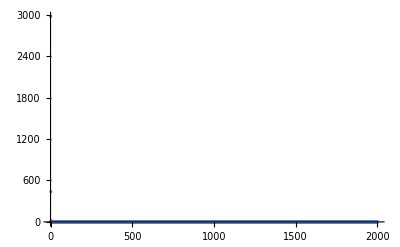

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[sphere,2];AppendTo[Solution30,Solution]]
```

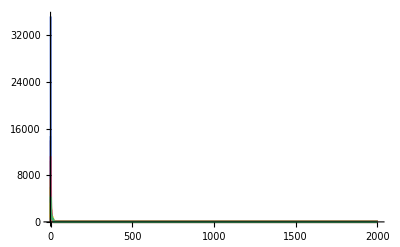

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{101.044,12.4106,8.12578,7.19618,4.65378,0.639376,0.639376,0.479376,0.090576,0.070976,0.010576,0.010576,0.010256,0.000576,0.000256,0.000256,0.000256,0.000016,0.000016,0.000016,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{35236.4,1259.82,1034.89,1034.89,972.439,972.439,150.499,114.355,106.102,3.33468,3.3312,3.22792,2.0992,1.96452,0.284521,0.284521,0.284521,0.188521,0.115721,0.019721,0.010121,0.000221,0.0002,0.0002,0.0002,0.0002,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{5732.93,1481.72,721.671,510.865,428.841,345.596,216.366,160.971,124.511,99.2425,83.357,60.4798,48.1104,39.0953,34.6093,34.1461,27.3997,12.0179,9.56881,9.35764,2.30323,2.22929,2.22632,0.581927,0.0332243,0.00502127,0.0018619,0.00181923,0.0016901,0.000969167,0.0006077,0.0005846,0.0005571,0.000419733,0.0004185,0.000405533,0.000398033,0.0003787,0.000364667,0.0000168,0.0000101,5.×10^-6,4.46667×10^-6,3.53333×10^-6,3.4×10^-6,3.4×10^-6,2.86667×10^-6,2.86667×10^-6,2.83333×10^-6,2.83333×10^-6,2.3×10^-6,2.16667×10^-6,2.16667×10^-6,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,3.33333×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

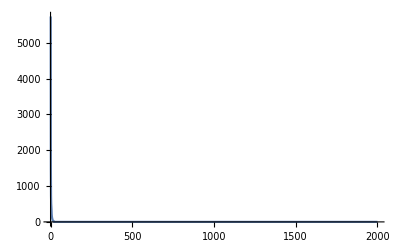

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{3946.3,928.627,561.806,389.391,227.665,183.955,78.9867,25.0057,19.2135,8.80649,5.31696,4.56127,3.38734,2.30198,0.399957,0.190799,0.076155,0.0727975,0.0430625,0.021001,0.0059425,0.000945,0.0007585,0.000383,0.000246,0.0001725,0.0000365,0.000026,0.000016,0.0000105,1.×10^-6,1.×10^-6,1.×10^-6,5.×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{6857.68,1634.76,591.688,501.058,505.875,436.93,268.611,252.032,219.275,207.029,202.405,180.628,138.467,116.751,114.479,113.204,90.8458,49.1827,48.0868,47.6264,12.3797,12.1494,12.1455,3.15466,0.154772,0.0112781,0.00540126,0.00527602,0.00482803,0.00271299,0.00194907,0.00194252,0.0019003,0.00182656,0.00182667,0.00182672,0.00182712,0.00182189,0.00182321,0.0000471391,0.0000325082,0.0000126655,0.0000125223,0.0000121421,0.0000121474,0.0000121474,0.0000119243,0.0000119243,0.0000119311,0.0000119311,0.0000116771,0.0000116799,0.0000116799,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,1.82574×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*sphere 5D*)
```

```mathematica
GA[sphere,5]
```

0.

```mathematica
Solution
```

{102695.,72039.6,32931.,16591.6,14911.2,14735.8,12866.9,11858.1,9055.51,6917.27,6883.23,6148.,3011.91,2167.09,1632.83,1469.31,1469.31,1456.54,919.355,918.615,908.04,873.917,671.157,537.873,408.115,189.288,188.775,29.2383,29.2187,22.335,22.2438,22.2131,19.9418,6.34247,6.32693,6.30947,5.95573,4.56373,4.56373,3.15573,3.15573,2.53373,2.53373,1.62193,0.561551,0.561551,0.56155,0.519511,0.518751,0.517722,0.266522,0.266442,0.266442,0.255382,0.237302,0.237302,0.197302,0.197302,0.197302,0.003822,0.003702,0.003702,0.003702,0.001942,0.001606,0.001602,0.000022,0.000022,0.000022,0.000018,0.000018,0.000018,0.000018,0.000018,0.000018,0.000018,0.000018,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

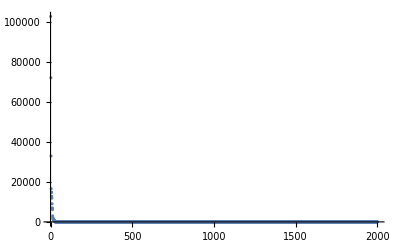

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[sphere,5];AppendTo[Solution30,Solution]]
```

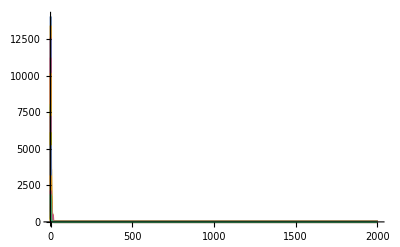

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{1.19034,1.19034,0.81514,0.81514,0.681412,0.681412,0.681412,0.567172,0.11234,0.057812,0.057812,0.003412,0.003232,0.002792,0.002792,0.002281,0.002281,0.00202,0.00202,0.00026,0.00026,0.000148,0.000148,0.000144,0.000104,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{14046.5,2379.4,574.124,268.652,63.7029,62.4541,29.3509,28.4817,20.1353,5.2562,0.873896,0.057896,0.057896,0.055796,0.055796,0.055796,0.010196,0.010196,0.010196,0.0101,0.000196,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{5253.09,1589.36,795.209,513.265,400.034,263.864,178.263,126.343,101.423,86.0005,49.1781,37.0268,35.864,30.6739,13.5451,2.25177,1.18039,0.622714,0.435275,0.376886,0.303461,0.233757,0.213133,0.074762,0.0616355,0.0376743,0.036521,0.0347845,0.0325158,0.0322077,0.00979337,0.00234737,0.00220253,0.00131483,0.00131043,0.00130777,0.00106043,0.0010504,0.000425733,0.0000674667,0.0000234667,0.0000234667,0.0000185333,0.0000178667,0.0000178667,0.0000178667,0.0000177333,0.0000177333,7.6×10^-6,7.6×10^-6,9.33333×10^-7,9.×10^-7,8.66667×10^-7,8.66667×10^-7,5.66667×10^-7,5.33333×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

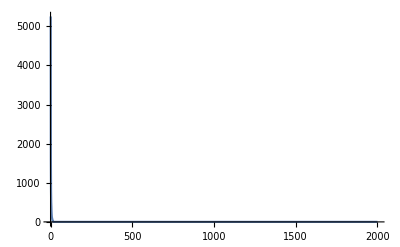

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{4286.53,1045.79,454.478,246.168,144.429,81.2328,47.7531,19.3373,11.9465,10.197,4.898,1.43712,0.881373,0.765186,0.543506,0.264033,0.0756415,0.0184865,0.012133,0.0110225,0.0016845,0.001632,0.000526,0.000162,0.0001,0.0000525,0.0000525,0.0000185,0.0000165,0.0000105,3.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{4322.75,1596.04,826.529,528.962,470.927,327.422,230.301,197.469,175.762,161.559,123.445,114.934,114.771,98.9534,51.4683,4.84162,3.02738,1.11924,0.915027,0.893331,0.860211,0.742431,0.738418,0.179643,0.166531,0.123073,0.121788,0.121141,0.120572,0.120528,0.0348273,0.00881889,0.00859445,0.00477605,0.00477726,0.00477799,0.00412506,0.00412598,0.00191613,0.000337159,0.0000978538,0.0000978538,0.0000964654,0.0000965411,0.0000965411,0.0000965411,0.0000965637,0.0000965637,0.0000410623,0.0000410623,4.56322×10^-6,4.55881×10^-6,4.56171×10^-6,4.56171×10^-6,2.9206×10^-6,2.92119×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*sphere 10D*)
```

```mathematica
GA[sphere,10]
```

0.

```mathematica
Solution
```

{327583.,327161.,297057.,282475.,236463.,188769.,183924.,177586.,177385.,169838.,169620.,134713.,134713.,134621.,133621.,127964.,127217.,127123.,101014.,101007.,99764.2,99748.1,98635.3,97319.2,97283.4,97242.9,97015.,96950.7,96690.4,96690.4,96166.6,95153.4,95153.4,95148.7,95063.1,95002.4,94844.1,94844.1,94242.9,94049.4,94006.,93895.8,93873.,92379.7,92337.8,92328.1,92209.8,92071.,92066.6,92004.3,91999.7,91922.9,91875.3,91734.5,91734.5,91731.8,91731.8,91731.8,91334.8,91179.8,91179.6,91170.8,91167.1,91132.7,91119.3,91096.1,91096.1,91096.1,91095.3,91095.3,91095.3,90614.2,90614.2,90273.7,90273.7,90228.1,90226.5,90226.5,90226.5,90214.,90106.5,90106.5,90106.5,90088.4,90082.1,90073.2,90073.2,90055.9,90055.9,90050.8,90043.8,90043.8,90043.8,90043.8,90041.8,90041.8,90041.8,90041.5,90041.4,90032.6,90032.6,90027.5,90027.5,90027.5,90027.5,90027.1,90027.1,90026.8,90023.6,90023.5,90018.7,90018.1,90016.,90015.7,90015.7,90014.3,90013.6,90013.6,90013.6,90013.5,90010.7,90008.3,90006.2,90006.1,90006.1,90006.1,90006.1,90005.8,90005.2,54251.3,52660.3,52660.3,14939.1,14939.1,5053.33,5053.33,263.823,253.332,214.411,214.411,213.41,211.968,205.241,199.584,198.081,198.081,198.081,125.814,125.762,125.719,125.719,122.893,113.736,113.736,113.717,113.717,113.717,113.716,112.724,112.387,112.014,109.298,109.296,109.296,109.296,109.079,108.512,107.899,107.899,104.432,104.429,104.429,104.424,104.424,103.956,103.955,103.734,103.734,103.01,103.01,103.01,103.005,103.005,102.699,101.832,101.358,101.358,101.358,101.353,101.346,100.568,100.568,100.568,17.52,17.52,17.5087,17.5087,17.5046,17.4647,4.62083,0.151924,0.151924,0.151924,0.151924,0.151924,0.151924,0.151924,0.151924,0.151924,0.151587,0.151587,0.107924,0.107924,0.107924,0.107924,0.096384,0.096384,0.096384,0.081604,0.056388,0.055844,0.041644,0.041644,0.041529,0.041529,0.041529,0.041484,0.041053,0.041053,0.041053,0.038693,0.038693,0.038693,0.033053,0.033053,0.033053,0.026381,0.026381,0.026101,0.026101,0.018176,0.018176,0.018176,0.018176,0.018176,0.018176,0.018176,0.018176,0.018052,0.018052,0.018052,0.017296,0.017296,0.017296,0.017184,0.015056,0.015056,0.015056,0.015056,0.015056,0.015056,0.012332,0.012332,0.012204,0.012204,0.012204,0.012204,0.012204,0.012204,0.012204,0.0115,0.01118,0.01118,0.01118,0.01118,0.01118,0.01118,0.01118,0.01118,0.01118,0.009749,0.009749,0.009605,0.009605,0.009605,0.008765,0.008765,0.008765,0.008765,0.008765,0.008404,0.008404,0.008404,0.008404,0.008404,0.007972,0.007972,0.007964,0.007964,0.007964,0.007924,0.007924,0.0079,0.0079,0.0079,0.007875,0.007875,0.007875,0.007875,0.007875,0.007875,0.00774,0.00774,0.00774,0.001435,0.001435,0.001435,0.001435,0.001435,0.001387,0.001275,0.001275,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.000875,0.00046,0.000391,0.000391,0.000391,0.000391,0.000391,0.000371,0.000352,0.000352,0.000352,0.000352,0.000352,0.000352,0.000352,0.000352,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000327,0.000319,0.000314,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000187,0.000104,0.000104,0.000104,0.000104,0.000104,0.000104,0.000099,0.000099,0.000087,0.000087,0.000083,0.000083,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000019,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

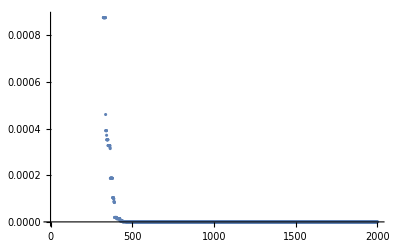

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[sphere,10];AppendTo[Solution30,Solution]]
```

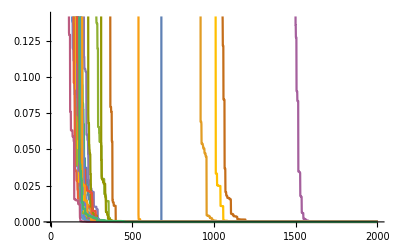

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{192266.,148812.,148812.,119233.,119233.,112181.,112154.,95428.3,83235.2,80202.4,74267.9,72216.1,53462.9,38285.5,36870.9,20937.2,20937.2,14002.3,13269.8,9085.85,8607.66,8607.66,8156.05,8156.05,7841.95,7327.47,7249.01,7166.74,6302.68,4831.54,4513.05,4268.1,4145.2,3901.28,3428.49,3298.58,2718.77,2718.77,2705.51,2077.78,2077.78,2030.05,1866.99,1802.66,1601.23,1520.23,1396.87,1396.87,1260.59,1051.92,977.584,952.246,933.915,933.221,636.817,636.726,610.975,588.267,490.297,490.049,329.413,329.036,198.738,198.738,198.738,198.738,198.152,198.152,173.965,173.965,173.965,145.274,145.274,145.274,145.252,136.612,136.612,116.615,116.418,59.6263,59.6263,59.5213,59.0905,54.5002,54.5002,54.1926,54.1926,29.5429,29.5429,29.5429,29.5429,29.2389,28.2127,28.2127,28.2127,27.9139,27.9139,26.4407,24.6934,24.6934,20.0934,19.9395,19.9395,18.9255,18.6829,18.6829,15.8728,15.8728,15.5754,15.3138,15.3138,15.3138,15.3118,14.606,14.6057,14.6057,14.6015,14.6015,14.5022,12.5944,10.5701,10.5694,9.58217,7.87406,7.87404,7.87404,7.87404,5.99437,5.82909,4.84204,4.82312,4.82312,4.82312,4.12544,4.12544,3.59327,2.54925,2.54925,2.54739,2.54349,2.42148,2.42148,2.39807,2.39327,2.39327,1.88687,1.88207,1.88207,1.81778,1.81778,1.81778,1.81568,1.81568,1.81568,1.62818,1.62809,1.62809,1.62809,1.62483,1.45609,1.45342,1.45342,1.41227,1.41227,1.41225,1.23775,1.23775,1.23775,1.23775,1.23711,1.23711,0.74431,0.74431,0.742286,0.741218,0.741218,0.04191,0.04191,0.03999,0.03999,0.039979,0.039294,0.03507,0.03507,0.03507,0.03507,0.02999,0.02999,0.02999,0.028342,0.028342,0.01339,0.01339,0.01339,0.01339,0.01339,0.013355,0.013355,0.009126,0.009126,0.009023,0.009023,0.009023,0.009023,0.009023,0.009023,0.009015,0.008986,0.008986,0.008986,0.006039,0.006039,0.006039,0.006039,0.006039,0.006039,0.005527,0.005519,0.005159,0.005159,0.005114,0.005114,0.005114,0.005114,0.005114,0.005114,0.005101,0.00501,0.00501,0.00501,0.00501,0.004094,0.004094,0.004094,0.004094,0.004094,0.004054,0.004054,0.004054,0.004054,0.004054,0.004054,0.004054,0.003614,0.003614,0.003614,0.003614,0.003614,0.003614,0.003555,0.003555,0.003555,0.003555,0.00355,0.00355,0.003151,0.002949,0.002949,0.002949,0.002949,0.002949,0.002949,0.002925,0.002925,0.002925,0.002925,0.002925,0.002709,0.002709,0.002709,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.002553,0.000952,0.000952,0.000952,0.000952,0.000952,0.000952,0.000944,0.000944,0.000936,0.000936,0.000936,0.000936,0.000936,0.000936,0.000936,0.000936,0.000936,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000935,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000535,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.000531,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.00053,0.000529,0.000529,0.000529,0.000529,0.000529,0.000529,0.000529,0.000529,0.000529,0.000226,0.000226,0.000226,0.000226,0.000226,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000025,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{528767.,333130.,305413.,294478.,215645.,176327.,170299.,167674.,143671.,121723.,112271.,109509.,80422.9,77790.8,76455.2,69900.,65043.3,60647.2,60444.3,53847.4,53187.,52224.,48320.6,42843.5,40866.7,36118.9,26948.5,26173.2,24706.6,22181.7,21968.4,20886.9,17265.9,15234.,15234.,15220.3,11851.6,11483.6,11468.8,8209.55,8208.12,8184.77,3170.47,3170.47,3151.9,3088.87,2705.33,2221.35,2184.59,2161.87,2128.18,2088.79,1688.34,1688.34,1637.24,1637.24,1637.24,1371.94,1296.09,1091.54,1019.14,996.588,996.588,996.588,955.843,868.172,819.962,799.778,799.778,785.61,605.818,605.818,605.818,602.569,572.89,572.89,572.89,572.89,572.89,293.239,293.239,130.955,127.285,86.4073,80.5534,80.5534,79.6435,63.0914,63.0914,63.0914,63.0732,63.0732,62.407,25.8492,25.8401,22.9723,22.9723,20.0056,18.4229,17.6471,17.6471,17.6471,17.6471,15.7349,15.7349,14.9849,14.5919,10.4126,10.4126,10.3605,8.06862,8.06862,8.06862,8.06862,7.8877,7.8877,7.8877,7.8877,6.00366,6.00366,6.00366,6.00366,6.00118,5.71766,5.71766,5.63342,5.3675,5.3675,5.23282,5.23282,5.23282,5.23282,0.76482,0.76482,0.76482,0.75736,0.7501,0.634336,0.63106,0.63106,0.62642,0.62642,0.525536,0.525536,0.525536,0.458416,0.435376,0.433516,0.433516,0.408944,0.215949,0.189501,0.189501,0.189501,0.188745,0.188745,0.188745,0.188745,0.188456,0.175556,0.162524,0.162524,0.162524,0.08014,0.08014,0.08014,0.08014,0.08014,0.08014,0.08014,0.08014,0.06102,0.053656,0.053656,0.05218,0.05218,0.042256,0.04078,0.032599,0.032599,0.032599,0.02898,0.01954,0.0186,0.004684,0.004684,0.004684,0.004684,0.004684,0.00412,0.00412,0.00412,0.00412,0.003284,0.00316,0.002544,0.002544,0.002144,0.002144,0.002144,0.002144,0.002144,0.002144,0.002144,0.002144,0.002143,0.002132,0.001375,0.001343,0.001343,0.001243,0.001243,0.001243,0.001243,0.001243,0.001243,0.001091,0.001091,0.001063,0.001063,0.001063,0.001063,0.001063,0.001063,0.001059,0.001019,0.001019,0.001019,0.001019,0.001019,0.001019,0.000899,0.000859,0.000459,0.000459,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000299,0.000291,0.000291,0.000291,0.000291,0.000291,0.000291,0.000291,0.000201,0.000201,0.000201,0.0002,0.0002,0.0002,0.0002,0.0002,0.000162,0.000162,0.00015,0.00015,0.00015,0.00015,0.00015,0.00015,0.000146,0.000146,0.000146,0.000146,0.000146,0.000146,0.000146,0.000146,0.00013,0.00013,0.00013,0.00013,0.00013,0.00003,0.00003,0.00003,0.00003,0.00003,0.00003,0.00003,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000029,0.000022,0.000022,0.000022,0.000022,0.000022,0.000022,0.000022,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,0.000017,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{368029.,296276.,256899.,229477.,203564.,183374.,166272.,144884.,133030.,127361.,116947.,101916.,95557.2,88607.9,83086.3,78145.3,74242.9,70231.7,66156.5,62698.1,59568.2,57898.7,55533.,53208.9,51064.2,48583.4,47184.7,46045.6,44976.5,43944.,43474.9,42431.,41576.3,40993.,40466.8,40111.7,39548.9,39334.6,38950.,38508.8,38366.6,38144.2,37868.2,37245.1,37040.4,36941.5,36801.,36654.,36487.2,36122.8,36018.5,35907.8,35802.1,35730.1,35293.8,35218.,35085.9,35018.5,34648.7,34245.1,34197.8,34125.4,34070.,34033.6,33980.3,33936.1,33924.4,33885.2,31171.8,31121.9,31076.1,31043.1,31012.6,30793.6,30752.5,30730.8,30698.7,30676.7,30663.5,30567.1,30552.,30524.,30512.2,30494.,30491.2,30482.6,30473.3,30459.,30442.,30422.8,30417.9,27750.2,27744.2,27739.9,27735.3,27542.1,27498.8,27496.5,27464.9,27455.,27453.,27450.6,27418.8,27399.7,27065.2,27063.4,27061.3,27060.2,27056.8,27056.2,27054.8,27053.5,27052.4,27035.7,27035.3,27034.6,27031.,27028.9,27028.1,27027.8,27012.2,27012.,27011.4,27011.1,27010.8,27009.6,27008.6,27007.4,27007.2,27006.5,27006.2,27006.,27005.6,27004.8,27004.5,27003.8,27003.7,27003.5,27003.4,27003.3,27003.2,27003.,27002.9,27002.7,27002.7,27002.4,27002.2,27002.2,27002.2,27001.9,27001.8,27001.8,27001.7,27001.6,27001.5,27001.4,27001.4,27001.3,27001.3,27001.3,27001.2,27001.,27001.,27001.,27001.,27001.,27000.9,27000.9,27000.5,27000.5,27000.5,27000.5,27000.5,27000.5,27000.4,27000.4,27000.3,27000.3,27000.3,27000.3,27000.3,27000.3,27000.1,27000.1,24547.3,24547.3,24546.8,24337.3,24337.3,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24333.4,24309.4,24309.4,24308.7,24308.7,24308.7,24010.7,24010.3,24009.9,24009.9,24008.4,24008.4,24003.9,24003.9,24001.8,24001.8,24001.8,24001.5,24001.5,24001.5,24001.5,24000.4,24000.4,24000.4,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.2,24000.1,24000.1,24000.1,24000.1,24000.1,24000.1,24000.1,21213.4,21213.4,21213.4,21213.4,21213.4,21163.4,21163.4,21128.3,21128.3,21125.,21115.6,21109.2,21109.2,21108.8,21108.8,21108.4,21108.4,21045.8,21037.,21017.8,21017.8,21017.8,21001.,21000.8,21000.8,21000.8,21000.8,21000.8,21000.8,21000.8,21000.8,21000.8,21000.8,21000.7,21000.7,21000.7,21000.7,21000.7,21000.3,21000.3,21000.3,21000.3,21000.3,21000.3,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,21000.2,19333.5,19333.5,19333.3,18333.4,18333.4,18333.4,18213.9,18213.9,18013.9,18013.9,18006.1,18006.1,18006.1,18006.1,18005.6,18005.6,18001.8,18001.6,18001.6,18000.7,18000.7,18000.7,18000.7,18000.7,18000.7,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.6,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,18000.,15333.3,15333.3,15333.3,15333.3,15331.9,15284.3,15004.3,15004.3,15004.3,15004.3,15004.3,15002.1,15002.1,15002.1,15002.1,15002.1,15002.1,15002.1,15002.1,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,15000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,12000.,10667.2,10667.2,10667.2,9680.57,9677.91,9664.58,9664.58,9601.52,9396.58,9334.07,9334.05,9334.05,9333.93,9333.93,9333.59,9333.59,9333.59,9333.59,9333.58,9333.45,9333.45,9333.44,9333.44,9333.44,9333.44,9333.44,9333.44,9333.41,9282.3,9279.85,9279.85,9017.48,9015.25,9015.25,9015.15,9015.15,9014.96,9014.96,9014.96,9000.26,9000.25,9000.25,9000.25,9000.25,9000.19,9000.19,9000.19,9000.19,9000.19,9000.19,9000.15,9000.15,9000.15,9000.11,9000.11,9000.11,9000.11,9000.08,9000.08,9000.08,9000.08,9000.08,9000.08,9000.08,9000.07,9000.07,9000.07,9000.07,9000.07,9000.07,9000.07,9000.07,9000.07,9000.06,9000.06,9000.06,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.04,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.03,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.02,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,9000.,6333.34,6330.67,6330.67,6330.67,6330.67,6012.81,6012.81,6012.81,6009.19,6009.17,6009.17,6004.26,6001.85,6001.85,6001.85,6001.81,6001.34,6001.34,6001.33,6001.33,6001.33,6000.94,6000.83,6000.83,6000.82,6000.82,6000.82,6000.32,6000.32,6000.3,6000.3,6000.2,6000.2,6000.2,6000.2,6000.2,6000.04,4613.41,4613.33,4613.33,4613.33,3016.86,3016.63,3016.27,3008.33,3006.74,3006.74,3006.74,3006.74,3004.64,3003.4,3003.4,3003.4,3002.23,3002.21,3001.29,3000.48,3000.48,3000.47,3000.44,3000.4,3000.4,3000.4,3000.4,3000.4,3000.4,3000.4,3000.4,3000.34,3000.33,3000.33,3000.3,3000.29,3000.29,3000.29,3000.26,3000.19,3000.15,3000.15,3000.15,3000.1,3000.08,3000.08,3000.08,3000.07,3000.07,3000.07,3000.07,3000.07,3000.07,3000.07,3000.07,3000.07,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.01,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,600.,386.667,272.551,272.29,266.678,241.662,106.712,106.712,106.678,105.662,105.662,55.6915,52.3556,52.0922,50.2649,50.2649,27.7651,27.7651,27.7651,27.7574,27.7281,24.0818,23.3722,23.3722,23.3722,16.8715,16.8715,16.8661,16.8661,16.8386,15.6655,15.6655,15.6655,15.6655,14.2589,14.2589,14.2589,14.2589,14.2589,14.1504,14.1504,14.0961,14.0961,14.017,14.017,11.8098,11.5696,11.5696,11.0226,10.7086,10.7086,7.44873,7.44873,7.44866,6.80946,6.80946,6.80946,6.80946,6.80946,6.76364,6.76364,6.75153,6.74855,5.67255,5.67255,5.67255,5.66909,2.53112,2.45694,2.14455,2.14455,1.96596,0.742766,0.738838,0.738838,0.728611,0.728611,0.426704,0.426704,0.369192,0.353333,0.353245,0.352677,0.338115,0.338115,0.338115,0.338115,0.299923,0.296316,0.262518,0.251645,0.251645,0.251645,0.251645,0.251645,0.251645,0.250464,0.250464,0.250136,0.250136,0.248244,0.204498,0.204498,0.203681,0.203681,0.203681,0.201378,0.197755,0.053257,0.053257,0.053257,0.053257,0.0532055,0.052917,0.052917,0.0152537,0.0152537,0.0152537,0.0152537,0.0152263,0.0106811,0.0106811,0.0106811,0.0106804,0.0106804,0.0106804,0.00889377,0.00889377,0.00889377,0.00886643,0.00577377,0.00577377,0.00577377,0.00577377,0.00577377,0.00574803,0.0045311,0.0045311,0.00424843,0.00424843,0.00424843,0.00424843,0.0030111,0.0030111,0.0030111,0.0030111,0.00300777,0.00278443,0.00278443,0.00278443,0.00278443,0.00278443,0.00278443,0.00116043,0.00116043,0.00116043,0.00116043,0.00116043,0.0011571,0.0011539,0.0011539,0.0011463,0.00113243,0.00113243,0.00113243,0.000600433,0.000600433,0.0005971,0.0005971,0.000580967,0.000580967,0.0005799,0.0005799,0.0005799,0.000213367,0.000213367,0.000213367,0.000206567,0.000206567,0.000206567,0.000206567,0.000206567,0.0002039,0.0002039,0.0000735333,0.0000735333,0.0000735333,0.0000735333,0.0000735333,0.0000735333,0.0000735333,0.0000735333,0.0000602,0.0000602,0.0000602,0.0000568667,0.0000568667,0.0000568667,0.0000568667,0.0000547333,0.0000547333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000307333,0.0000248667,0.0000248667,0.0000248667,0.0000248667,0.0000119333,0.0000119333,0.0000119333,0.0000119333,0.0000119333,9.8×10^-6,9.8×10^-6,9.8×10^-6,9.8×10^-6,8.3×10^-6,8.3×10^-6,8.3×10^-6,8.3×10^-6,8.3×10^-6,8.3×10^-6,7.76667×10^-6,7.76667×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.63333×10^-6,5.4×10^-6,5.4×10^-6,5.4×10^-6,5.4×10^-6,5.4×10^-6,5.4×10^-6,5.4×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,5.33333×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.8×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.76667×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,4.23333×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.7×10^-6,3.56667×10^-6,3.56667×10^-6,3.56667×10^-6,3.56667×10^-6,3.56667×10^-6,3.56667×10^-6,3.56667×10^-6,3.03333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,1.43333×10^-6,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7}

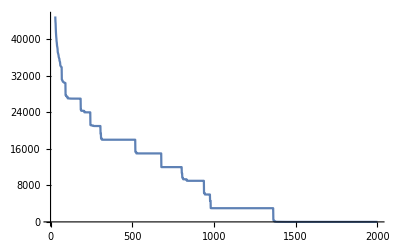

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{355721.,286525.,256380.,234728.,206919.,188260.,162662.,127361.,119626.,116051.,102554.,94548.2,80599.2,78366.,77164.6,63298.7,58825.7,52637.5,44884.6,41645.6,38416.5,36293.4,34246.2,29198.2,28797.1,24026.6,22262.7,20188.8,18163.4,17461.3,17243.4,17115.7,16093.6,14398.7,14319.8,14210.2,13086.1,13086.1,12949.6,12811.1,12734.,12173.8,12145.1,8792.98,8767.23,8675.14,8650.06,8372.14,7722.06,5347.48,4950.03,4577.35,4041.38,4036.12,1905.92,1871.6,1871.25,1731.87,1491.9,1455.14,1357.15,1161.7,1160.07,1147.4,1010.26,965.562,941.457,859.798,858.396,839.619,758.106,640.658,607.859,604.062,578.387,578.31,569.217,566.053,525.763,325.785,325.785,192.175,188.616,188.117,177.696,177.046,156.65,131.671,124.153,89.8631,86.3086,85.9699,85.2077,84.9751,83.2952,81.2501,70.079,70.079,62.545,62.1473,61.4037,51.5271,51.5271,50.6181,31.121,23.8267,19.6959,18.8413,16.196,15.9834,15.9825,15.9786,15.9776,14.5228,14.0819,14.0819,12.9155,12.9143,12.7508,11.5259,10.3068,10.2898,9.79566,8.7914,8.78529,8.41099,8.41099,6.18857,6.10593,5.92087,5.37608,5.02797,4.63002,4.28053,4.01009,3.75864,3.23663,3.13285,2.60885,2.60689,2.54589,2.54589,2.37465,2.36475,2.36429,2.1653,1.95205,1.95205,1.91964,1.50551,1.17304,1.17304,1.16875,1.16875,1.04546,1.0451,0.892702,0.812057,0.805954,0.802874,0.802874,0.42164,0.402034,0.378406,0.378406,0.357492,0.293239,0.204577,0.204577,0.204577,0.204577,0.204441,0.204441,0.201053,0.200321,0.189327,0.118861,0.118861,0.118861,0.097713,0.095533,0.095533,0.093353,0.093353,0.093353,0.093069,0.093069,0.093069,0.085743,0.070659,0.070659,0.0545235,0.0542995,0.041569,0.041569,0.0413345,0.040709,0.035589,0.035589,0.035589,0.0355675,0.0355675,0.032908,0.0315905,0.028404,0.028404,0.028404,0.028404,0.0283495,0.021937,0.0209785,0.0209785,0.0209785,0.0178385,0.015037,0.015037,0.015037,0.0144695,0.0144695,0.0144695,0.0141135,0.0139715,0.0128215,0.0126435,0.0125635,0.011058,0.0110435,0.0110435,0.0109435,0.0109435,0.0109435,0.0109435,0.0108635,0.010841,0.010841,0.010841,0.0107975,0.0107975,0.0107475,0.0107475,0.0107475,0.0107055,0.0107055,0.0106975,0.0097895,0.0079625,0.007952,0.007952,0.007952,0.007864,0.007772,0.007772,0.0036075,0.003425,0.003425,0.0032255,0.0031105,0.0031105,0.0031105,0.0031105,0.0031105,0.0031105,0.0029705,0.0029705,0.0028665,0.0028665,0.0028645,0.0027565,0.0027565,0.0027565,0.0026785,0.0026785,0.002535,0.002535,0.0017875,0.0017875,0.000918,0.000918,0.000918,0.000918,0.000918,0.00091,0.00091,0.000887,0.000887,0.000787,0.000722,0.000551,0.000551,0.000539,0.000539,0.000539,0.0005385,0.0004805,0.0004605,0.0004175,0.000405,0.000371,0.000371,0.000371,0.0003585,0.0003585,0.0003585,0.0003585,0.000346,0.000346,0.000346,0.000317,0.000317,0.000303,0.000303,0.000272,0.00027,0.00027,0.000264,0.000264,0.000264,0.000264,0.000264,0.000264,0.000264,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.00025,0.0002025,0.0002005,0.0001725,0.0001725,0.0001725,0.0001725,0.0001725,0.0001725,0.000168,0.000166,0.000166,0.000166,0.000141,0.000141,0.000141,0.000141,0.0001145,0.0001145,0.0001005,0.0001005,0.0001005,0.0000925,0.0000925,0.000088,0.000088,0.000088,0.0000805,0.0000805,0.0000805,0.0000805,0.0000805,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.0000695,0.0000695,0.0000695,0.0000595,0.0000595,0.000058,0.000058,0.000058,0.0000335,0.0000335,0.000029,0.000023,0.000023,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000205,0.0000165,0.0000165,0.0000165,0.000015,0.000012,0.000012,0.000012,9.5×10^-6,9.5×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,2.5×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{76828.3,66925.6,67669.2,67540.6,72891.5,70649.8,64280.7,65947.4,63275.5,63322.7,60553.6,53187.3,51114.5,52462.6,49796.4,49384.4,49173.9,50725.1,48516.1,48607.,46981.7,47139.9,46875.3,46933.7,46039.6,45297.,45654.,44795.7,45024.9,45019.7,45079.5,44050.9,44132.2,44278.,44282.1,44284.4,44121.3,44050.,43898.,43894.4,43792.6,43797.4,43892.6,43593.4,43627.8,43631.3,43570.8,43629.4,43667.7,43831.4,43846.3,43873.,43895.,43874.7,44109.3,44120.1,44085.6,44095.1,44295.4,43810.5,43834.,43839.6,43827.6,43824.5,43818.7,43816.1,43820.9,43820.5,42677.,42662.3,42672.5,42690.3,42700.5,42821.4,42814.6,42816.4,42832.1,42844.8,42839.9,42903.6,42904.2,42905.1,42912.3,42916.6,42918.4,42920.8,42926.1,42922.9,42927.,42922.9,42925.6,41557.3,41561.2,41562.8,41561.2,41656.6,41681.8,41681.9,41700.4,41706.5,41707.3,41708.1,41727.4,41737.2,41920.8,41921.5,41922.1,41921.3,41922.2,41922.4,41922.8,41922.6,41923.,41933.6,41933.3,41933.1,41935.4,41936.7,41937.1,41937.1,41946.9,41946.8,41946.3,41946.4,41946.3,41945.9,41946.5,41946.9,41946.8,41947.3,41947.4,41947.4,41947.5,41947.6,41947.7,41948.,41948.,41948.1,41948.2,41948.1,41948.2,41948.3,41948.2,41948.2,41948.2,41947.9,41948.,41947.9,41947.9,41947.8,41947.9,41947.9,41947.8,41947.8,41947.7,41947.7,41947.8,41947.8,41947.7,41947.7,41947.8,41947.8,41947.8,41947.8,41947.8,41947.8,41947.8,41947.8,41948.1,41948.1,41948.1,41948.1,41948.1,41948.1,41948.,41948.,41948.1,41948.1,41948.1,41948.1,41948.1,41948.1,41948.2,41948.2,40254.6,40254.6,40254.7,40314.8,40314.8,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40316.3,40325.3,40325.3,40325.6,40325.6,40325.6,40473.4,40473.6,40473.9,40473.9,40474.8,40474.8,40477.5,40477.5,40478.8,40478.8,40478.8,40479.,40479.,40479.,40479.,40479.7,40479.7,40479.7,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,40479.8,38614.2,38614.2,38614.2,38614.2,38614.2,38635.,38635.1,38650.8,38650.8,38652.3,38656.7,38659.8,38659.8,38660.,38660.,38660.2,38660.2,38691.6,38696.3,38706.6,38706.6,38706.6,38715.9,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.1,38716.3,38716.3,38716.3,38716.3,38716.3,38716.3,38716.3,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,38716.4,36665.5,36665.5,36665.6,36491.2,36491.2,36491.2,36525.3,36525.3,36608.4,36608.4,36612.3,36612.3,36612.3,36612.3,36612.6,36612.6,36614.5,36614.6,36614.6,36615.,36615.,36615.,36615.,36615.,36615.,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.1,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,36615.4,34011.5,34011.5,34011.5,34011.5,34011.7,34020.5,34112.5,34112.5,34112.5,34112.5,34112.5,34113.4,34113.4,34113.4,34113.4,34113.4,34113.4,34113.4,34113.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,34114.4,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,31117.1,28398.6,28398.6,28398.6,27483.8,27482.8,27477.5,27477.5,27455.3,27413.,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.2,27409.3,27409.4,27409.4,27455.8,27456.5,27456.5,27456.6,27456.6,27456.6,27456.6,27456.6,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.5,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,27461.6,22816.1,22815.7,22815.7,22815.7,22815.7,22830.4,22830.4,22830.4,22831.3,22831.3,22831.3,22832.6,22833.2,22833.2,22833.2,22833.2,22833.4,22833.4,22833.4,22833.4,22833.4,22833.5,22833.5,22833.5,22833.5,22833.5,22833.5,22833.6,22833.6,22833.6,22833.6,22833.7,22833.7,22833.7,22833.7,22833.7,22833.1,18386.5,18386.5,18386.5,18386.5,16428.7,16428.8,16428.8,16430.2,16430.4,16430.4,16430.4,16430.4,16430.8,16431.,16431.,16431.,16431.3,16431.3,16431.4,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.6,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,3286.34,2117.86,1492.82,1491.39,1460.66,1323.64,584.483,584.483,584.301,578.734,578.734,305.035,286.763,285.32,275.312,275.312,152.076,152.076,152.076,152.034,151.873,131.901,128.015,128.015,128.015,92.4091,92.4091,92.3793,92.3793,92.229,85.8035,85.8035,85.8035,85.8034,78.0992,78.0992,78.0992,78.0992,78.0992,77.5048,77.5048,77.2074,77.2074,76.7744,76.7744,64.6849,63.3694,63.3694,60.3734,58.6533,58.6533,40.7984,40.7984,40.798,37.297,37.297,37.297,37.297,37.297,37.046,37.046,36.9797,36.9634,31.0698,31.0698,31.0698,31.0509,13.8635,13.4572,11.7462,11.7462,10.768,4.06829,4.04678,4.04678,3.99076,3.99076,2.33715,2.33715,2.02215,1.93528,1.9348,1.93169,1.85193,1.85193,1.85193,1.85193,1.64274,1.62299,1.43787,1.37831,1.37831,1.37831,1.37831,1.37831,1.37831,1.37184,1.37184,1.37005,1.37005,1.35968,1.12008,1.12008,1.1156,1.1156,1.1156,1.10299,1.08314,0.291696,0.291696,0.291696,0.291696,0.291414,0.289833,0.289833,0.0835427,0.0835427,0.0835427,0.0835427,0.083393,0.0584979,0.0584979,0.0584979,0.058494,0.058494,0.058494,0.0487081,0.0487081,0.0487081,0.0485584,0.0316191,0.0316191,0.0316191,0.0316191,0.0316191,0.0314782,0.0248128,0.0248128,0.0232645,0.0232645,0.0232645,0.0232645,0.0164874,0.0164874,0.0164874,0.0164874,0.0164691,0.0152459,0.0152459,0.0152459,0.0152459,0.0152459,0.0152459,0.00635086,0.00635086,0.00635086,0.00635086,0.00635086,0.0063326,0.00631507,0.00631507,0.00627344,0.00619749,0.00619749,0.00619749,0.00328361,0.00328361,0.00326535,0.00326535,0.00317699,0.00317699,0.00317114,0.00317114,0.00317114,0.00116356,0.00116356,0.00116356,0.00112632,0.00112632,0.00112632,0.00112632,0.00112632,0.00111171,0.00111171,0.000397669,0.000397669,0.000397669,0.000397669,0.000397669,0.000397669,0.000397669,0.000397669,0.000324641,0.000324641,0.000324641,0.000306384,0.000306384,0.000306384,0.000306384,0.0002947,0.0002947,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.000163257,0.00013113,0.00013113,0.00013113,0.00013113,0.0000603244,0.0000603244,0.0000603244,0.0000603244,0.0000603244,0.0000486546,0.0000486546,0.0000486546,0.0000486546,0.0000404544,0.0000404544,0.0000404544,0.0000404544,0.0000404544,0.0000404544,0.0000375405,0.0000375405,0.000025901,0.000025901,0.000025901,0.000025901,0.000025901,0.000025901,0.000025901,0.000025901,0.0000246305,0.0000246305,0.0000246305,0.0000246305,0.0000246305,0.0000246305,0.0000246305,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000242677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000213677,0.0000211867,0.0000211867,0.0000211867,0.0000211867,0.0000211867,0.0000211867,0.0000211867,0.0000211867,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000182939,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000154119,0.0000146938,0.0000146938,0.0000146938,0.0000146938,0.0000146938,0.0000146938,0.0000146938,0.0000118365,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,3.8835×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74092×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6,2.74616×10^-6}

```mathematica
(*SUM OF DIFFERENT POWERS FUNCTION*)
```

```mathematica
SDP[x_]:=Module[{l=Length@x},Sum[Abs[x[[i]]]^(i+1),{i,l}]]
```

```mathematica
(*SDP 2D*)
```

```mathematica
GA[SDP,2]
```

0.

```mathematica
Solution
```

{18870.7,7272.09,6615.29,6615.29,199.289,199.187,6.25927,6.25927,6.24967,1.14771,0.0100689,0.0100689,0.0100689,0.01,0.000068921,0.000068921,0.000068921,1.×10^-9,1.×10^-9,1.×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

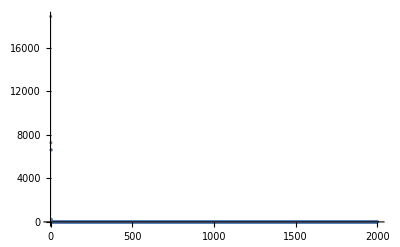

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SDP,2];AppendTo[Solution30,Solution]]
```

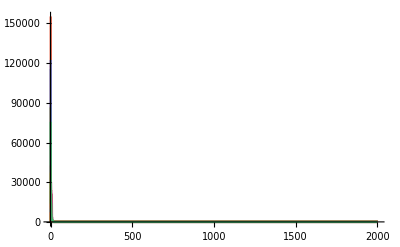

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{258.48,258.48,258.48,13.1922,10.1386,4.77061,3.93701,3.93679,3.18339,3.15491,0.968985,0.953305,0.615385,0.0309773,0.030977,0.030976,0.030976,0.000577,0.000576001,0.000576001,0.000400001,0.000400001,1.×10^-9,1.×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{155310.,22153.6,21218.6,20262.9,4720.23,520.79,484.408,439.264,371.21,227.498,105.09,101.808,36.1762,36.1434,34.8485,34.8468,33.5845,33.5836,33.5832,33.542,11.0563,11.0152,2.89367,2.89367,2.39,0.0767666,0.0113916,0.0110906,0.0110906,0.0110906,0.0110896,0.0110896,0.00993937,0.00993937,0.00993937,0.00536038,0.00536038,0.00449313,0.00449313,0.000858375,0.000858375,0.000858375,0.000858375,0.000637056,0.000098336,1.343×10^-6,1.343×10^-6,1.343×10^-6,1.343×10^-6,3.43×10^-7,3.43×10^-7,1.×10^-9,1.×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{33558.3,7312.02,4752.17,3516.12,2098.8,1341.91,999.91,869.318,305.882,218.23,195.205,82.4279,66.3926,59.1797,26.9412,26.4948,6.8947,6.71527,5.95161,5.50871,4.4218,3.57888,0.628776,0.344212,0.285426,0.0672389,0.0573751,0.0487096,0.00305868,0.00258707,0.0025609,0.00148374,0.00129378,0.00123445,0.000834388,0.000681221,0.000350346,0.000306004,0.000176429,0.0000405751,0.0000312584,0.0000312584,0.0000291272,0.0000217478,3.62343×10^-6,3.90067×10^-7,3.44867×10^-7,3.44867×10^-7,3.44867×10^-7,3.11533×10^-7,3.11533×10^-7,3.00133×10^-7,3.001×10^-7,3.00067×10^-7,3.00067×10^-7,3.00067×10^-7,3.00033×10^-7,3.00033×10^-7,3.00033×10^-7,3.00033×10^-7,3.00033×10^-7,3.00033×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.×10^-7,3.33333×10^-8,3.33333×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

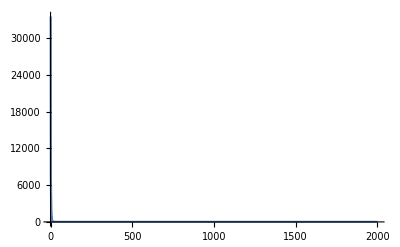

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{17667.8,5113.64,1125.12,467.262,214.451,117.838,109.635,27.7173,16.7299,11.1654,3.11161,2.34139,1.56307,0.921017,0.22913,0.141474,0.0884024,0.0431384,0.0304266,0.0239989,0.0180398,0.0101793,0.00079,0.000544,0.000544,0.000325024,0.0000213245,0.000016,0.000011324,4.4565×10^-6,4.4565×10^-6,3.5985×10^-6,1.4×10^-8,4.5×10^-9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{39591.8,7633.88,7312.12,6072.13,4669.19,3885.66,3735.54,3652.65,801.641,677.178,624.87,253.773,234.453,226.894,112.865,112.804,17.1633,17.0282,16.5862,16.1751,15.1376,12.1601,1.81792,1.00067,0.949148,0.203947,0.200357,0.187185,0.00836486,0.00799033,0.00799264,0.00442654,0.00399806,0.00378657,0.00318528,0.00282319,0.00130522,0.00113825,0.000825681,0.000162698,0.000156657,0.000156657,0.000156631,0.000116228,0.0000179644,1.66103×10^-6,1.65296×10^-6,1.65296×10^-6,1.65296×10^-6,1.64218×10^-6,1.64218×10^-6,1.64314×10^-6,1.64315×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64316×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.82574×10^-7,1.82574×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*SDP 5D*)
```

```mathematica
GA[SDP,5]
```

0.

```mathematica
Solution
```

{3.8596×10^11,1.67677×10^10,1.67677×10^10,2.27501×10^8,2.27325×10^8,1.84509×10^8,1.81339×10^8,1.81339×10^8,9.27033×10^7,8.42303×10^7,7.16875×10^7,6.44068×10^7,2.07147×10^7,2.06388×10^7,1.43597×10^7,9.08585×10^6,7.04814×10^6,2.99844×10^6,2.99398×10^6,2.4285×10^6,2.31916×10^6,2.31829×10^6,2.1441×10^6,265061.,261452.,254583.,249781.,246916.,246916.,216127.,216127.,216127.,212203.,177861.,177861.,177825.,173978.,171027.,76731.9,76603.7,1711.05,1711.05,1710.92,1708.86,327.795,327.596,317.174,317.022,39.2108,39.034,9.97791,9.96986,9.91403,7.34534,7.34534,5.06534,4.23539,1.61013,1.61013,1.34692,0.300472,0.300472,0.170867,0.166963,0.15194,0.15194,0.147555,0.136766,0.136766,0.0677473,0.0658113,0.0658113,0.0658113,0.0658113,0.059235,0.059235,0.0592027,0.00323612,0.0032078,0.0032078,0.0016078,0.0016078,0.0016078,0.0016078,0.0016074,0.0016074,0.0016074,0.00160734,0.00160734,0.00160734,0.00160734,0.00160425,0.0000193181,4.24612×10^-6,4.24612×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,4.18212×10^-6,2.024×10^-12,2.024×10^-12,2.024×10^-12,2.024×10^-12,1.024×10^-12,1.024×10^-12,1.024×10^-12,1.024×10^-12,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

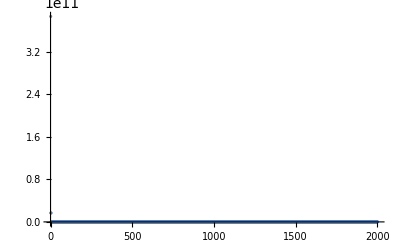

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SDP,5];AppendTo[Solution30,Solution]]
```

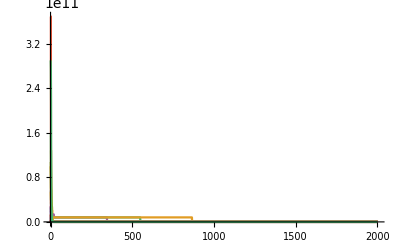

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{1.0457×10^8,1.04529×10^8,4.7434×10^7,4.33343×10^7,4.01353×10^7,4.01353×10^7,3.64491×10^6,3.64476×10^6,3.46214×10^6,3.1772×10^6,2.41286×10^6,2.38116×10^6,2.32955×10^6,2.23097×10^6,2.23097×10^6,2.13083×10^6,2.13051×10^6,1.76963×10^6,585610.,572732.,554740.,98962.2,98473.4,98467.4,93830.1,55578.9,55444.1,55432.,54241.7,1168.35,1168.35,517.382,517.382,512.54,314.94,295.794,282.906,264.296,263.93,53.9697,53.9697,31.3325,31.1614,30.9086,30.9086,28.1157,2.42337,2.16297,1.78544,1.24424,1.24424,0.0241032,0.0240942,0.0240942,0.0240942,0.0136232,0.0136232,0.0136102,0.0136102,0.0125807,0.0125807,0.0047808,0.000124576,0.000124576,0.000124576,0.000121751,0.000121751,1.75066×10^-6,1.75066×10^-6,1.53366×10^-6,1.53366×10^-6,1.02266×10^-6,1.02266×10^-6,5.33661×10^-7,5.33661×10^-7,5.33661×10^-7,2.26602×10^-8,2.26602×10^-8,2.26602×10^-8,2.26602×10^-8,8.3786×10^-9,8.3786×10^-9,8.3786×10^-9,8.3786×10^-9,6.98557×10^-9,6.98557×10^-9,6.58903×10^-9,6.58903×10^-9,2.88957×10^-9,2.88957×10^-9,2.88957×10^-9,2.88957×10^-9,2.88957×10^-9,2.88957×10^-9,1.88957×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.1×10^-9,1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10,1.×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{3.69429×10^11,3.69426×10^11,1.03527×10^8,7.1298×10^7,7.1298×10^7,8.76867×10^6,8.47642×10^6,4.58652×10^6,696263.,535426.,395987.,340940.,84727.8,53555.9,50730.,48524.1,41735.2,37840.,31141.5,11186.2,1633.11,1521.49,1417.19,1417.19,1225.21,1225.21,304.319,159.96,159.945,132.052,132.051,25.6662,22.5497,7.99994,2.16754,1.89257,1.89257,1.89257,1.89257,1.89169,1.81569,1.77961,0.224251,0.18505,0.18505,0.0517933,0.0517933,0.0515485,0.0103485,0.0098188,0.00906232,0.00906232,0.00841871,0.00841871,0.00841871,0.00841736,0.00817389,0.00817389,0.00817389,0.00805329,0.00805329,0.0000532861,0.0000532861,0.0000532861,0.0000480833,0.0000430833,7.02566×10^-6,5.85187×10^-6,1.83077×10^-6,1.83077×10^-6,1.80783×10^-6,1.80783×10^-6,1.80783×10^-6,1.50383×10^-6,6.97832×10^-7,6.97832×10^-7,6.97832×10^-7,3.93825×10^-7,3.93825×10^-7,3.93825×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.97681×10^-7,1.632×10^-7,1.632×10^-7,1.632×10^-7,1.632×10^-7,1.632×10^-7,1.632×10^-7,1.632×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,1.6×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{4.88112×10^10,4.6082×10^10,2.09977×10^10,1.08593×10^10,6.03665×10^9,4.9107×10^9,4.0983×10^9,3.64411×10^9,2.72834×10^9,2.24045×10^9,2.00994×10^9,1.48861×10^9,1.43276×10^9,1.14317×10^9,1.05525×10^9,1.04477×10^9,1.03454×10^9,1.03059×10^9,1.02144×10^9,1.01947×10^9,8.40825×10^8,8.31987×10^8,8.31372×10^8,8.28372×10^8,8.25933×10^8,8.25588×10^8,8.22115×10^8,8.21705×10^8,8.21359×10^8,8.2116×10^8,8.2075×10^8,8.20647×10^8,8.20315×10^8,8.20116×10^8,8.19431×10^8,8.15446×10^8,8.15186×10^8,8.1517×10^8,8.15159×10^8,8.1513×10^8,8.1511×10^8,8.15104×10^8,8.15093×10^8,8.1509×10^8,8.15075×10^8,8.15075×10^8,8.15075×10^8,8.15074×10^8,8.15072×10^8,8.15072×10^8,8.11805×10^8,8.11804×10^8,8.11172×10^8,8.11172×10^8,8.11131×10^8,8.11029×10^8,8.11029×10^8,8.11029×10^8,8.11003×10^8,8.11003×10^8,8.11002×10^8,8.11002×10^8,8.10967×10^8,8.10967×10^8,8.10966×10^8,8.10964×10^8,8.10961×10^8,8.10955×10^8,8.10955×10^8,8.10955×10^8,8.10954×10^8,8.1092×10^8,8.10915×10^8,8.10908×10^8,8.10904×10^8,8.10904×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10903×10^8,8.10037×10^8,8.10037×10^8,8.10036×10^8,8.10021×10^8,8.10021×10^8,8.1002×10^8,8.10005×10^8,8.10005×10^8,8.10005×10^8,8.10004×10^8,8.10004×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,8.10003×10^8,5.43336×10^8,5.43336×10^8,5.43231×10^8,5.42741×10^8,5.4002×10^8,5.40012×10^8,5.40006×10^8,5.40006×10^8,5.40006×10^8,5.40006×10^8,5.40006×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,5.40003×10^8,3.48088×10^8,3.48088×10^8,2.76915×10^8,2.76915×10^8,2.74917×10^8,2.74917×10^8,2.74917×10^8,2.70837×10^8,2.70767×10^8,2.70767×10^8,2.70488×10^8,2.70488×10^8,2.70488×10^8,2.70377×10^8,2.70377×10^8,2.70029×10^8,2.70026×10^8,2.70026×10^8,2.70012×10^8,2.70012×10^8,2.70012×10^8,2.7001×10^8,2.7001×10^8,2.7001×10^8,2.70009×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,2.70003×10^8,3.33637×10^6,3.33637×10^6,3.33637×10^6,3.33531×10^6,3.06757×10^6,434811.,429162.,424037.,114317.,114317.,11287.7,11287.7,11209.3,11209.3,8645.11,3042.03,3042.03,3000.9,3000.89,3000.84,3000.84,3000.84,3000.84,3000.05,3000.05,3000.05,3000.05,3000.05,3000.04,3000.04,3000.04,3000.04,3000.04,3000.04,3000.04,3000.04,3000.04,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,3000.,333.333,333.333,332.8,332.001,6.77333×10^-14,6.77333×10^-14,6.77333×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,6.66667×10^-14,3.33333×10^-14,3.33333×10^-14,3.33333×10^-14,3.33333×10^-14,3.33333×10^-14,3.33333×10^-14,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

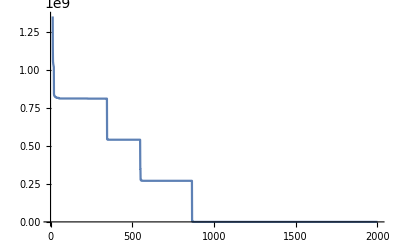

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{1.20871×10^10,8.06262×10^9,1.99511×10^9,1.55932×10^9,9.52702×10^8,7.1474×10^8,3.48368×10^8,2.92211×10^8,2.27285×10^8,1.21841×10^8,8.46619×10^7,5.69746×10^7,3.95031×10^7,1.83831×10^7,9.90288×10^6,8.5001×10^6,3.88906×10^6,2.34993×10^6,2.29399×10^6,2.20988×10^6,1.16718×10^6,749922.,621162.,418454.,290782.,203562.,54665.9,44648.,25732.7,12250.4,11791.4,11162.5,9113.67,7161.58,5806.91,1586.91,1550.97,1373.48,1200.98,936.465,503.088,487.794,399.148,273.404,273.404,251.031,195.859,143.605,106.866,91.8685,44.7071,26.8342,18.8114,9.79912,1.2675,1.26573,1.11972,0.735028,0.314865,0.215378,0.213675,0.175639,0.154302,0.0695408,0.0626749,0.0501149,0.0485631,0.0474541,0.0472715,0.0129622,0.00870081,0.003925,0.00377562,0.0037691,0.00344989,0.00344989,0.00052878,0.000184176,0.000184176,0.000184176,0.000182245,0.0000281565,9.60701×10^-6,8.82169×10^-6,6.89115×10^-6,5.67815×10^-6,5.67815×10^-6,5.67815×10^-6,5.30127×10^-6,5.17815×10^-6,5.17815×10^-6,5.04527×10^-6,3.31275×10^-6,1.784×10^-6,1.0045×10^-6,1.004×10^-6,1.004×10^-6,5.80002×10^-7,5.80001×10^-7,5.80001×10^-7,5.8×10^-7,5.8×10^-7,5.8×10^-7,8.5×10^-8,9.03202×10^-9,8.0325×10^-9,6.101×10^-9,6.101×10^-9,2.6005×10^-9,2.6005×10^-9,2.6005×10^-9,2.6005×10^-9,5.16387×10^-10,8.53533×10^-12,8.53533×10^-12,8.53533×10^-12,5.23328×10^-13,5.23328×10^-13,5.23328×10^-13,3.11405×10^-14,3.11405×10^-14,2.5376×10^-14,2.5376×10^-14,1.×10^-15,1.×10^-15,1.×10^-15,1.×10^-15,1.×10^-15,5.005×10^-16,5.005×10^-16,5.×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{8.76171×10^10,8.6366×10^10,4.5145×10^10,1.78841×10^10,9.27975×10^9,8.47155×10^9,7.35282×10^9,6.90053×10^9,5.88136×10^9,4.73817×10^9,4.62976×10^9,3.38661×10^9,3.37113×10^9,3.16491×10^9,3.164×10^9,3.15706×10^9,3.15699×10^9,3.15016×10^9,3.1325×10^9,3.13131×10^9,2.49442×10^9,2.49231×10^9,2.49221×10^9,2.48354×10^9,2.48435×10^9,2.48357×10^9,2.47367×10^9,2.4725×10^9,2.47152×10^9,2.47103×10^9,2.46984×10^9,2.46968×10^9,2.46874×10^9,2.4688×10^9,2.46897×10^9,2.47015×10^9,2.47006×10^9,2.47001×10^9,2.47002×10^9,2.47×10^9,2.46998×10^9,2.46999×10^9,2.46999×10^9,2.46999×10^9,2.46994×10^9,2.46994×10^9,2.46994×10^9,2.46994×10^9,2.46994×10^9,2.46994×10^9,2.47095×10^9,2.47095×10^9,2.47116×10^9,2.47116×10^9,2.47118×10^9,2.47121×10^9,2.47121×10^9,2.47121×10^9,2.47121×10^9,2.47121×10^9,2.47121×10^9,2.47121×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47122×10^9,2.47123×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47124×10^9,2.47153×10^9,2.47153×10^9,2.47153×10^9,2.47153×10^9,2.47153×10^9,2.47153×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.47154×10^9,2.05421×10^9,2.05421×10^9,2.05423×10^9,2.05435×10^9,2.05503×10^9,2.05503×10^9,2.05503×10^9,2.05503×10^9,2.05503×10^9,2.05503×10^9,2.05503×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,2.05504×10^9,1.52522×10^9,1.52522×10^9,1.47803×10^9,1.47803×10^9,1.47817×10^9,1.47817×10^9,1.47817×10^9,1.4787×10^9,1.47871×10^9,1.47871×10^9,1.47876×10^9,1.47876×10^9,1.47876×10^9,1.47878×10^9,1.47878×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.47885×10^9,1.82571×10^7,1.82571×10^7,1.82571×10^7,1.82512×10^7,1.67848×10^7,2.36462×10^6,2.33368×10^6,2.30561×10^6,609364.,609361.,47740.1,47740.1,47337.2,47337.2,34510.6,16425.3,16425.3,16431.5,16431.5,16431.5,16431.5,16431.5,16431.5,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,16431.7,1825.74,1825.74,1822.82,1818.45,3.70991×10^-13,3.70991×10^-13,3.70991×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,3.65148×10^-13,1.82574×10^-13,1.82574×10^-13,1.82574×10^-13,1.82574×10^-13,1.82574×10^-13,1.82574×10^-13,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*SDP 10D*)
```

```mathematica
GA[SDP,10]
```

0.

```mathematica
Solution
```

{8.46827×10^18,8.46823×10^18,7.6169×10^18,2.20484×10^18,1.37583×10^18,8.77453×10^17,8.77453×10^17,8.76205×10^17,2.6093×10^16,2.6093×10^16,1.45602×10^16,1.4512×10^16,1.45056×10^16,3.08904×10^15,3.04419×10^15,3.03145×10^15,3.02676×10^15,3.02676×10^15,3.02329×10^15,3.02329×10^15,3.01377×10^15,3.01377×10^15,3.01246×10^15,3.01246×10^15,3.01246×10^15,3.01246×10^15,7.61288×10^14,7.61288×10^14,7.60996×10^14,7.60996×10^14,7.60655×10^14,7.60655×10^14,7.60654×10^14,7.60626×10^14,7.6036×10^14,7.6036×10^14,7.60346×10^14,7.60344×10^14,7.60344×10^14,7.60283×10^14,7.60283×10^14,7.60281×10^14,7.60281×10^14,7.60281×10^14,7.60281×10^14,7.6028×10^14,7.60253×10^14,7.60253×10^14,7.60253×10^14,7.60253×10^14,7.60253×10^14,7.60251×10^14,7.60251×10^14,7.60251×10^14,7.6025×10^14,7.6025×10^14,7.6025×10^14,7.6025×10^14,7.6025×10^14,7.3143×10^14,7.29073×10^14,7.29073×10^14,7.29073×10^14,7.29073×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29063×10^14,7.29045×10^14,7.29031×10^14,7.29031×10^14,7.29029×10^14,7.29009×10^14,7.29009×10^14,7.29009×10^14,7.29009×10^14,7.29009×10^14,7.29007×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,7.29×10^14,9.9976×10^11,9.9976×10^11,8.85823×10^11,2.62065×10^11,4.09363×10^9,4.09363×10^9,6.41668×10^7,6.41668×10^7,6.41668×10^7,6.41668×10^7,6.41668×10^7,90000.8,90000.8,90000.8,90000.7,90000.7,90000.5,90000.5,90000.2,90000.2,90000.2,90000.2,90000.2,90000.2,90000.2,90000.2,90000.2,90000.2,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,90000.,10000.,10000.,10000.,3600.,400.,400.,392.04,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.06065×10^-12,3.00805×10^-12,3.00805×10^-12,3.00805×10^-12,3.00805×10^-12,3.00805×10^-12,3.00622×10^-12,3.00622×10^-12,3.00622×10^-12,3.00622×10^-12,3.00622×10^-12,3.00622×10^-12,2.90602×10^-12,2.90602×10^-12,2.90602×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.20696×10^-12,1.19689×10^-12,1.10493×10^-12,1.10493×10^-12,1.10493×10^-12,1.10493×10^-12,1.10493×10^-12,1.10493×10^-12,1.02662×10^-12,1.02662×10^-12,1.02662×10^-12,1.02662×10^-12,1.02662×10^-12,1.02662×10^-12,1.02662×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.01509×10^-12,1.011×10^-12,1.011×10^-12,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,1.60939×10^-14,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,6.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,5.02744×10^-15,4.60801×10^-15,9.31438×10^-16,9.31438×10^-16,9.31438×10^-16,9.31438×10^-16,9.31438×10^-16,9.31438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19438×10^-16,4.19437×10^-16,4.19437×10^-16,4.19437×10^-16,7.561×10^-21,6.561×10^-21,6.561×10^-21,6.561×10^-21,6.561×10^-21,6.561×10^-21,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,1.×10^-24,5.9049×10^-26,5.9049×10^-26,5.9049×10^-26,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,1.×10^-30,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

```mathematica
ListPlot@Solution
```

-Graphics-

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SDP,10];AppendTo[Solution30,Solution]]
```

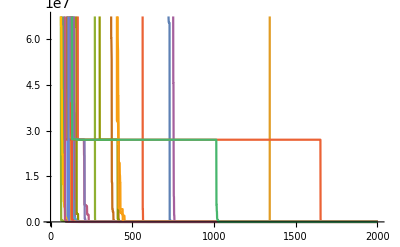

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{3.83472×10^18,3.83472×10^18,2.06603×10^18,2.06602×10^18,1.30924×10^18,1.30437×10^18,1.01444×10^16,9.99284×10^15,8.72104×10^15,4.14701×10^15,3.89684×10^15,8.85824×10^14,6.47773×10^14,6.4712×10^14,6.43245×10^14,1.01153×10^14,9.95978×10^13,9.95978×10^13,2.62261×10^13,1.09038×10^13,1.02721×10^13,5.78427×10^12,5.09676×10^12,5.09676×10^12,1.60089×10^12,1.5963×10^12,1.58421×10^12,1.49487×10^12,1.49487×10^12,1.494×10^12,1.49021×10^12,1.09241×10^12,1.09241×10^12,2.28203×10^11,2.282×10^11,6.55875×10^10,6.48361×10^10,6.44437×10^10,6.42112×10^10,6.41485×10^10,6.41387×10^10,6.41239×10^10,6.41239×10^10,6.41044×10^10,6.41044×10^10,6.29126×10^10,6.29122×10^10,6.29103×10^10,6.29101×10^10,6.29054×10^10,6.28684×10^10,8.50938×10^9,8.50889×10^9,3.45472×10^9,3.4441×10^9,3.4441×10^9,2.74107×10^9,2.61841×10^9,2.61841×10^9,2.61841×10^9,1.88092×10^9,4.98556×10^8,4.98556×10^8,4.98517×10^8,3.62881×10^8,3.50627×10^8,3.02319×10^8,2.44759×10^8,1.84816×10^8,1.59033×10^8,1.59033×10^8,1.48414×10^8,1.48414×10^8,1.48414×10^8,1.37723×10^8,1.37581×10^8,1.37578×10^8,1.27733×10^8,1.27733×10^8,1.27733×10^8,1.27724×10^8,1.27712×10^8,1.25289×10^8,1.25038×10^8,1.25038×10^8,1.25009×10^8,1.17659×10^8,766847.,766847.,765027.,681819.,614039.,614039.,614039.,135980.,121469.,121428.,121428.,93638.1,82228.9,82228.9,72310.5,72310.5,59423.1,57067.5,44524.7,36307.4,36307.4,36289.6,34697.2,34673.9,33138.3,29640.7,27024.7,27004.6,14061.7,14016.3,14016.2,7800.36,7800.36,7800.36,7800.36,7800.36,3576.85,3186.33,3186.33,2969.28,1269.38,1269.38,1269.38,1268.91,1265.65,1265.65,1264.78,1262.28,1262.28,1262.28,76.5749,76.5749,76.5017,71.2311,71.1509,71.1509,71.1052,71.1052,71.1052,71.0771,71.0771,3.02523,2.99715,2.99715,2.99668,2.9361,2.9361,2.93502,2.93502,2.93476,2.93294,2.93247,2.92834,2.90792,2.90792,1.53341,1.53341,1.53129,1.53129,1.53129,1.53129,1.53129,1.53129,1.51727,1.51727,1.51727,1.51727,1.06799,1.06799,1.06799,1.06101,1.06101,1.04406,1.04194,1.04012,1.02404,1.02404,1.02404,0.0200305,0.0200305,0.0200305,0.0181905,0.0127794,0.0127794,0.0103424,0.0103424,0.0103374,0.0103374,0.0103374,0.0100877,0.0100877,0.00955032,0.00955032,0.00955032,0.00955032,0.00955032,0.0095332,0.0095332,0.0095332,0.00952544,0.00886244,0.00886008,0.00886008,0.00885886,0.00885886,0.00885886,0.00836555,0.00836555,0.00836555,0.00836555,0.00823756,0.00823756,0.00823756,0.00823756,0.000244958,0.000244958,0.000244958,0.000244958,0.000244958,0.000244958,0.000244958,0.00023241,0.000196283,0.000196283,0.000196283,0.000196283,0.000194904,0.000194904,0.000194904,0.000191724,0.000191724,0.000191724,0.000191724,0.000191724,0.000112038,0.000111814,0.000111814,0.000107814,0.000106063,0.0000948331,0.0000829302,0.0000829302,0.0000829302,0.0000829302,0.0000829302,0.0000829271,0.0000829271,0.0000828194,0.0000828194,0.0000828194,0.0000661411,0.000065839,0.000065839,0.000065839,0.000065839,0.000065839,0.000065839,0.000065839,0.000065839,0.0000657824,0.0000657824,1.90504×10^-6,1.90504×10^-6,1.90504×10^-6,1.90504×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.90152×10^-6,1.83752×10^-6,1.83752×10^-6,1.83752×10^-6,1.83752×10^-6,1.83752×10^-6,1.83752×10^-6,1.83752×10^-6,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16357×10^-8,2.16356×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,2.04806×10^-8,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,6.18138×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.97976×10^-13,2.72144×10^-13,2.72144×10^-13,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,3.58318×10^-14,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,5.15676×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,2.62474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,1.34474×10^-19,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{1.72025×10^23,1.72025×10^23,1.39984×10^23,1.03758×10^23,3.74774×10^20,3.74768×10^20,3.59562×10^20,2.26134×10^20,2.24787×10^20,1.48637×10^20,1.41217×10^20,1.16557×10^20,8.68453×10^19,8.68453×10^19,8.46886×10^19,8.46886×10^19,8.32702×10^19,8.32702×10^19,6.85837×10^19,6.82212×10^19,6.82211×10^19,6.81742×10^19,6.81471×10^19,6.8147×10^19,6.74269×10^19,6.74269×10^19,6.56557×10^19,6.56557×10^19,6.56505×10^19,6.56502×10^19,6.56198×10^19,6.56152×10^19,6.56151×10^19,6.5614×10^19,6.5614×10^19,6.56114×10^19,6.56114×10^19,6.56101×10^19,6.56101×10^19,6.56101×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,6.561×10^19,1.×10^16,1.×10^16,4.30467×10^15,4.30467×10^15,3.48×10^8,3.428×10^8,2.64074×10^8,2.36995×10^8,1.9363×10^8,1.92453×10^8,1.78691×10^8,1.69849×10^8,1.63814×10^8,1.63795×10^8,1.44376×10^8,1.44376×10^8,1.43453×10^8,1.43086×10^8,1.3318×10^8,1.3277×10^8,1.3265×10^8,1.29045×10^8,1.28952×10^8,1.11034×10^8,1.11034×10^8,1.11034×10^8,1.05228×10^8,6.25068×10^6,5.93962×10^6,4.31872×10^6,4.30888×10^6,4.25651×10^6,4.22743×10^6,4.18781×10^6,3.44685×10^6,3.40555×10^6,3.3968×10^6,3.39663×10^6,382187.,382187.,381324.,252462.,247207.,55191.4,55191.4,51524.7,51524.7,51524.7,50430.,47121.7,47121.7,46643.5,44989.7,44989.7,44165.1,41428.6,41385.9,38958.5,38958.5,38124.3,37989.1,37263.9,37026.6,36178.1,21645.9,21606.2,21606.2,17395.3,17395.3,17395.3,13398.2,13398.2,13398.2,13398.2,13341.7,13260.,13260.,12087.4,2543.99,2542.68,2136.49,2132.14,2132.14,2126.27,940.999,940.999,940.999,346.633,337.929,317.802,172.711,172.711,154.28,154.28,153.236,95.6031,79.748,79.748,79.7362,78.8707,78.8661,10.9612,10.7908,10.7908,10.7908,10.6422,10.6422,10.4305,10.4305,10.4263,10.4263,8.2636,8.2636,7.63432,2.06756,2.06756,2.06756,2.06756,2.06756,1.84875,1.84875,1.84875,1.84875,1.84875,1.84731,1.84731,1.84731,0.0646904,0.0646708,0.0646707,0.0646707,0.0646707,0.0646707,0.06434,0.06434,0.06434,0.06434,0.0643305,0.0643305,0.0643305,0.0643305,0.0643305,0.0158707,0.0158707,0.0158707,0.0158707,0.00884432,0.00884432,0.00884432,0.00884432,0.0086832,0.0086832,0.0086832,0.0086832,0.00866139,0.00866139,0.00866139,0.00117685,0.00117685,0.00117685,0.00117649,0.00117649,0.00111564,0.00111564,0.00111564,0.00111564,0.00111564,0.00111564,0.00111564,0.00111564,0.00110458,0.00110458,0.00110458,0.00103898,0.00103898,0.00103898,0.00103287,0.00103287,0.00103287,0.00102465,0.000110295,0.000110295,0.000110295,0.000103392,0.000103392,0.000103392,0.000103392,0.000103392,0.000103392,0.000102827,0.000102827,0.0000965037,0.0000884591,0.0000884591,0.0000804591,0.0000804591,0.000080295,0.0000786889,0.0000130889,0.0000130889,0.0000130889,0.0000130889,0.0000130889,0.0000130889,0.0000122898,0.0000122898,0.0000122898,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,3.17191×10^-6,2.30479×10^-6,2.26303×10^-6,1.54674×10^-6,1.30938×10^-6,1.26448×10^-6,1.26303×10^-6,1.26303×10^-6,1.15837×10^-6,1.15447×10^-6,1.15447×10^-6,1.15319×10^-6,1.15037×10^-6,1.15037×10^-6,1.15037×10^-6,1.15037×10^-6,1.15037×10^-6,1.15037×10^-6,1.15037×10^-6,1.07699×10^-6,1.07699×10^-6,1.07699×10^-6,1.07699×10^-6,1.07699×10^-6,1.07648×10^-6,1.56909×10^-7,1.56909×10^-7,1.56909×10^-7,1.56909×10^-7,1.56909×10^-7,1.56909×10^-7,1.56909×10^-7,1.56402×10^-7,1.56402×10^-7,1.56402×10^-7,1.56402×10^-7,1.56402×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.51672×10^-7,1.37032×10^-7,1.37032×10^-7,1.35558×10^-7,1.35558×10^-7,1.35558×10^-7,1.35558×10^-7,1.35558×10^-7,1.35558×10^-7,3.31585×10^-8,3.31585×10^-8,3.31585×10^-8,3.31585×10^-8,3.31585×10^-8,3.31585×10^-8,3.31585×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.20107×10^-8,3.18318×10^-8,3.18318×10^-8,3.18318×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03757×10^-8,1.03747×10^-8,1.03747×10^-8,1.03747×10^-8,1.03747×10^-8,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,3.75702×10^-10,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03259×10^-12,2.03251×10^-12,2.03251×10^-12,2.03251×10^-12,2.032×10^-12,2.032×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.03251×10^-12,1.032×10^-12,1.032×10^-12,1.032×10^-12,1.032×10^-12,1.032×10^-12,1.032×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.0001×10^-12,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.00001×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-16,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,2.56×10^-22,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,1.×10^-33,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{1.45004×10^22,1.27854×10^22,1.04392×10^22,8.84294×10^21,5.231×10^21,1.45807×10^21,1.41859×10^21,1.28026×10^21,1.0525×10^21,8.97542×10^20,8.85819×10^20,8.56272×10^20,8.19294×10^20,8.18868×10^20,7.18178×10^20,6.81805×10^20,6.81653×10^20,6.80397×10^20,6.79593×10^20,6.75875×10^20,6.75032×10^20,6.70438×10^20,6.66971×10^20,6.66952×10^20,6.66417×10^20,6.65757×10^20,6.65562×10^20,6.65532×10^20,6.65521×10^20,6.65521×10^20,6.65512×10^20,6.65184×10^20,6.6518×10^20,6.65172×10^20,6.65161×10^20,6.65135×10^20,6.65133×10^20,6.65133×10^20,6.65084×10^20,6.65084×10^20,6.65083×10^20,6.6506×10^20,6.6506×10^20,6.65058×10^20,6.65057×10^20,6.64862×10^20,6.64862×10^20,6.64862×10^20,6.64861×10^20,6.6486×10^20,6.64857×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.6267×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62669×10^20,6.62668×10^20,6.62668×10^20,6.62668×10^20,6.62668×10^20,6.62668×10^20,6.62668×10^20,6.62668×10^20,6.60482×10^20,6.60482×10^20,6.60482×10^20,6.60482×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60481×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,6.60474×10^20,4.73408×10^19,4.73408×10^19,4.19815×10^19,4.19815×10^19,4.19708×10^19,4.1951×10^19,4.37685×10^18,4.37685×10^18,4.37482×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37403×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,4.37402×10^18,2.18736×10^18,2.18736×10^18,2.18736×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18702×10^18,2.18469×10^18,2.18469×10^18,2.17887×10^18,1.25785×10^18,1.46263×10^15,1.46263×10^15,1.46263×10^15,1.4588×10^15,1.4588×10^15,1.4588×10^15,1.4588×10^15,1.4588×10^15,3.58037×10^14,3.58037×10^14,3.58037×10^14,3.58037×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.5777×10^14,3.57663×10^14,3.57663×10^14,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43834×10^13,2.43833×10^13,2.43833×10^13,2.43827×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.43813×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,2.4381×10^13,3.71716×10^12,3.71716×10^12,3.7019×10^12,4.55762×10^11,4.55762×10^11,3.74302×10^11,3.41757×10^11,9.56673×10^10,9.53598×10^10,9.53598×10^10,8.38123×10^10,8.37897×10^10,8.37887×10^10,8.37673×10^10,8.37673×10^10,8.10501×10^10,8.10292×10^10,8.10241×10^10,8.10233×10^10,8.10218×10^10,8.10214×10^10,8.10214×10^10,8.1021×10^10,8.1021×10^10,8.1021×10^10,8.10208×10^10,8.10208×10^10,8.10207×10^10,8.10072×10^10,8.10072×10^10,8.10072×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10018×10^10,8.10011×10^10,8.10011×10^10,8.1001×10^10,8.1001×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,8.10009×10^10,3.34233×10^8,2.58773×10^8,2.58773×10^8,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,900000.,33333.3,7200.,7200.,7200.,2133.33,2133.05,1692.76,1092.27,1008.49,1008.49,1007.71,1007.71,1007.52,1005.58,913.75,667.615,667.615,667.615,667.124,667.124,667.124,667.124,235.231,233.047,233.047,66.9011,66.9011,66.4466,59.4623,59.4623,56.9527,49.2568,9.9001,9.9001,9.9001,9.87861,4.55213,4.51455,4.51455,2.51346,2.40271,2.38127,2.38121,2.2137,2.2137,2.21364,2.21203,2.18863,2.18863,1.90565,1.90565,1.90565,1.90565,1.90565,1.90565,1.84283,1.84283,1.84283,1.84283,1.84283,1.70624,1.70624,1.33392,1.33392,1.33392,1.32392,1.32378,1.24547,1.24547,0.576768,0.576768,0.57676,0.528939,0.528939,0.511083,0.511083,0.465284,0.465284,0.465284,0.465284,0.358957,0.358957,0.358957,0.358957,0.358957,0.358957,0.358957,0.358957,0.357645,0.357645,0.357645,0.357426,0.357426,0.357426,0.338329,0.338329,0.338329,0.338329,0.338325,0.338325,0.338325,0.338325,0.334593,0.334593,0.334593,0.290408,0.281809,0.281809,0.281809,0.281809,0.20805,0.20805,0.20805,0.206703,0.206703,0.206661,0.000211439,0.000211439,0.000211405,0.000211405,0.000209857,0.000168792,0.000168792,0.000163577,0.000163577,0.00014453,0.00014453,0.00014453,0.000144522,0.0000622011,0.0000621579,0.0000621579,0.0000621579,0.0000621579,0.0000621579,0.0000621579,0.0000621579,0.0000365532,0.0000365532,0.0000365532,0.0000365532,0.0000365228,0.0000365228,0.0000365228,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,9.94272×10^-8,5.38399×10^-8,5.38399×10^-8,5.38399×10^-8,5.38399×10^-8,5.22006×10^-8,5.22006×10^-8,5.22006×10^-8,5.22006×10^-8,4.34265×10^-8,4.33966×10^-8,4.33966×10^-8,4.33966×10^-8,4.33966×10^-8,4.33966×10^-8,4.33966×10^-8,4.33966×10^-8,4.33959×10^-8,3.83441×10^-8,3.83441×10^-8,3.83441×10^-8,3.78183×10^-8,3.74774×10^-8,3.42591×10^-8,3.42591×10^-8,3.42591×10^-8,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,9.25741×10^-10,2.92408×10^-10,2.92408×10^-10,2.92408×10^-10,2.92408×10^-10,2.92408×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77813×10^-10,2.77758×10^-10,2.77758×10^-10,2.77758×10^-10,2.77758×10^-10,2.77758×10^-10,2.77758×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.74424×10^-10,2.73644×10^-10,2.73644×10^-10,2.73644×10^-10,2.73644×10^-10,2.66704×10^-10,2.66704×10^-10,2.66704×10^-10,2.66704×10^-10,2.66704×10^-10,2.66704×10^-10,2.66704×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,2.6667×10^-10,3.66918×10^-15,3.66918×10^-15,3.66918×10^-15,3.66918×10^-15,3.66918×10^-15,3.66918×10^-15,3.09452×10^-21,3.09452×10^-21,3.09452×10^-21,3.09452×10^-21,3.09452×10^-21,3.09452×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.22994×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,2.2266×10^-21,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24,8.73813×10^-24}

```mathematica
ListLinePlot@average
```

-Graphics-

```mathematica
median=Median@Solution30
```

{6.7915×10^20,6.7891×10^20,2.62909×10^20,1.55433×10^20,3.1415×10^19,3.07322×10^18,2.3924×10^18,1.6557×10^18,1.56924×10^18,8.17098×10^17,4.87719×10^17,2.09805×10^17,6.78007×10^16,6.41788×10^16,1.68178×10^16,1.67016×10^16,1.57461×10^16,1.57453×10^16,1.56503×10^16,1.56503×10^16,1.11453×10^16,1.10905×10^16,1.09218×10^16,1.0438×10^16,1.79413×10^15,1.78149×10^15,9.94225×10^14,9.1784×10^14,9.10115×10^14,6.87666×10^14,6.87629×10^14,5.77293×10^14,3.7502×10^14,2.01944×10^14,7.56046×10^13,3.97588×10^13,3.75299×10^13,3.08331×10^13,2.52936×10^13,1.60905×10^13,1.41405×10^13,1.15786×10^13,1.06531×10^13,5.45442×10^12,5.45441×10^12,5.45239×10^12,5.13765×10^12,3.39031×10^12,3.3896×10^12,3.36012×10^12,2.66592×10^12,2.20569×10^12,1.97955×10^12,1.66007×10^12,1.56698×10^12,1.10046×10^12,1.05608×10^12,8.7407×10^11,3.92803×10^11,3.76652×10^11,3.64342×10^11,3.64328×10^11,1.60934×10^11,1.6085×10^11,6.45501×10^10,6.26315×10^10,6.26198×10^10,6.26194×10^10,6.26192×10^10,6.25448×10^10,6.25442×10^10,6.25307×10^10,4.7587×10^10,4.71889×10^10,1.07298×10^10,9.01954×10^9,8.15712×10^9,7.74804×10^9,5.97865×10^9,5.97865×10^9,5.97858×10^9,4.4254×10^9,4.42385×10^9,4.41319×10^9,4.37658×10^9,4.36591×10^9,4.36563×10^9,4.35869×10^9,4.1317×10^9,4.13168×10^9,4.1265×10^9,4.12643×10^9,4.12639×10^9,4.11792×10^9,4.11789×10^9,4.11772×10^9,2.41423×10^8,2.38728×10^8,1.95675×10^8,1.8212×10^8,1.60355×10^8,1.59766×10^8,1.52653×10^8,1.48228×10^8,1.44911×10^8,1.4489×10^8,1.35178×10^8,1.35043×10^8,1.34561×10^8,1.34378×10^8,1.29425×10^8,1.29141×10^8,1.29081×10^8,1.27228×10^8,1.27101×10^8,1.25234×10^8,1.25234×10^8,1.2517×10^8,1.2515×10^8,1.25124×10^8,1.25123×10^8,1.25123×10^8,1.2511×10^8,1.25102×10^8,1.25102×10^8,1.25102×10^8,1.25097×10^8,1.25095×10^8,1.18003×10^8,1.05353×10^8,8.08151×10^7,3.3369×10^7,3.3369×10^7,2.7217×10^7,2.70863×10^7,2.70863×10^7,2.70863×10^7,2.70859×10^7,2.70824×10^7,2.70823×10^7,2.70822×10^7,2.70822×10^7,2.70822×10^7,2.70602×10^7,2.70602×10^7,2.70006×10^7,2.70006×10^7,1.45666×10^7,1.45665×10^7,1.43806×10^7,1.40038×10^7,1.39998×10^7,1.39983×10^7,1.39923×10^7,1.37051×10^7,1.36988×10^7,1.36988×10^7,1.36973×10^7,1.36957×10^7,1.50398×10^6,1.43362×10^6,1.43362×10^6,1.43362×10^6,1.43362×10^6,1.42809×10^6,1.35233×10^6,1.35233×10^6,1.35204×10^6,170079.,90068.6,90068.6,90068.6,90068.6,90068.6,90068.,90068.,90068.,90042.3,90008.5,90008.1,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.7,90005.6,90005.6,90005.1,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90001.5,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,90000.1,67401.6,67401.6,67401.6,67394.,67394.,67394.,55413.2,55413.2,55413.2,55413.2,54328.1,54328.1,54327.8,54327.8,54286.2,54285.7,54285.7,49339.5,16372.9,16372.4,16372.4,15410.1,15378.6,15375.8,15355.4,14281.5,11951.3,11951.3,11951.2,3032.24,724.867,638.576,638.576,408.584,331.915,331.915,320.734,320.734,318.242,318.007,181.207,181.201,181.2,181.2,181.2,113.371,109.812,109.811,109.642,105.63,100.076,98.4363,98.4363,96.7631,96.3687,76.7864,76.7568,76.7515,44.6676,44.3436,44.3436,44.3436,44.2717,41.48,41.48,2.78019,2.27919,2.27919,1.2209,1.22089,1.22075,1.19848,1.19848,1.19848,1.19848,1.19848,1.19607,1.19607,1.19607,0.546367,0.546367,0.546367,0.535548,0.535526,0.525515,0.525515,0.525515,0.525515,0.525099,0.521435,0.521435,0.521435,0.521435,0.51981,0.519609,0.519609,0.517928,0.517928,0.0196093,0.0196093,0.0193832,0.0193832,0.0193832,0.0193768,0.0157353,0.0157353,0.0157353,0.0155325,0.0155054,0.0154327,0.00503656,0.00503656,0.00176806,0.00176806,0.00176806,0.00176806,0.000361652,0.000360544,0.000360535,0.000360535,0.0000800783,0.0000800783,0.0000785718,0.0000785718,0.0000778678,0.0000776446,0.0000138185,0.0000138185,0.0000138185,0.00001347,0.00001347,0.0000114707,0.00001147,9.86046×10^-6,1.39612×10^-6,1.39609×10^-6,1.35751×10^-6,1.35751×10^-6,1.35751×10^-6,1.09635×10^-6,1.09635×10^-6,1.09635×10^-6,1.09635×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00889×10^-6,1.00884×10^-6,1.00884×10^-6,1.00884×10^-6,8.94304×10^-7,8.94304×10^-7,8.94304×10^-7,8.94304×10^-7,8.94304×10^-7,8.94304×10^-7,8.94266×10^-7,8.94266×10^-7,8.94266×10^-7,8.94266×10^-7,6.48858×10^-7,6.48858×10^-7,5.91049×10^-7,5.91049×10^-7,5.85313×10^-7,8.53131×10^-8,8.53126×10^-8,8.53126×10^-8,6.05277×10^-8,6.05277×10^-8,5.5655×10^-8,5.5655×10^-8,5.56471×10^-8,5.56471×10^-8,5.54839×10^-8,5.54839×10^-8,5.54839×10^-8,5.54839×10^-8,5.54839×10^-8,5.53559×10^-8,5.53559×10^-8,5.53559×10^-8,5.53559×10^-8,5.53559×10^-8,5.53559×10^-8,5.53559×10^-8,5.52805×10^-8,5.52805×10^-8,5.52805×10^-8,5.52805×10^-8,5.52663×10^-8,4.08054×10^-9,4.08054×10^-9,4.08054×10^-9,4.08054×10^-9,1.16282×10^-10,6.62874×10^-11,6.62874×10^-11,6.62874×10^-11,6.62874×10^-11,6.62874×10^-11,6.62711×10^-11,6.62711×10^-11,6.62711×10^-11,6.62711×10^-11,6.62711×10^-11,6.62711×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,6.62661×10^-11,5.85455×10^-11,5.85455×10^-11,5.85455×10^-11,5.85239×10^-11,5.85238×10^-11,9.01728×10^-12,9.01728×10^-12,8.53686×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.53167×10^-12,8.51821×10^-12,8.51821×10^-12,8.51821×10^-12,8.51821×10^-12,1.45369×10^-12,1.45369×10^-12,9.66446×10^-13,1.55158×10^-14,1.48501×10^-14,1.48501×10^-14,1.48501×10^-14,1.48491×10^-14,1.48491×10^-14,1.48491×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,1.34046×10^-14,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,5.84535×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,1.30558×10^-15,3.07×10^-16,3.07×10^-16,3.07×10^-16,3.07×10^-16,3.07×10^-16,3.07×10^-16,3.07×10^-16,1.01×10^-16,1.01×10^-16,8.3×10^-17,8.3×10^-17,8.3×10^-17,8.3×10^-17,8.3×10^-17,8.3×10^-17,8.3×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,8.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,3.25×10^-17,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,1.×10^-18,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,5.67237×10^-19,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,6.73679×10^-20,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56032×10^-22,2.56×10^-22,2.56×10^-22,1.28524×10^-22,1.28524×10^-22,1.28524×10^-22,5.5591×10^-25,5.26897×10^-25,5.26897×10^-25,5.26897×10^-25,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.7063×10^-27,4.1943×10^-27,4.1943×10^-27,4.1943×10^-27,4.1943×10^-27,2.60915×10^-27,2.60915×10^-27,2.60915×10^-27,2.60915×10^-27,2.60915×10^-27,2.60915×10^-27,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,5.12×10^-28,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{3.96725×10^22,3.82562×10^22,3.32816×10^22,2.87691×10^22,2.23124×10^22,5.65625×10^21,5.60287×10^21,5.29622×10^21,4.2269×10^21,3.92129×10^21,3.916×10^21,3.91835×10^21,3.798×10^21,3.79807×10^21,3.74358×10^21,3.64886×10^21,3.64872×10^21,3.64463×10^21,3.64461×10^21,3.62453×10^21,3.62022×10^21,3.61647×10^21,3.5976×10^21,3.59761×10^21,3.59482×10^21,3.59493×10^21,3.59422×10^21,3.59423×10^21,3.59419×10^21,3.59419×10^21,3.59417×10^21,3.59379×10^21,3.59378×10^21,3.59378×10^21,3.59372×10^21,3.59358×10^21,3.59357×10^21,3.59357×10^21,3.5933×10^21,3.5933×10^21,3.5933×10^21,3.59318×10^21,3.59318×10^21,3.59317×10^21,3.59317×10^21,3.5921×10^21,3.5921×10^21,3.59209×10^21,3.59209×10^21,3.59208×10^21,3.59207×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59247×10^21,3.59246×10^21,3.59246×10^21,3.59246×10^21,3.59246×10^21,3.59246×10^21,3.59246×10^21,3.59246×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59286×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,3.59282×10^21,2.35101×10^20,2.35101×10^20,2.05831×10^20,2.05831×10^20,2.05773×10^20,2.05665×10^20,1.6645×10^19,1.6645×10^19,1.66456×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.66458×10^19,1.19786×10^19,1.19786×10^19,1.19786×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19787×10^19,1.19659×10^19,1.19659×10^19,1.1934×10^19,6.88941×10^18,7.87414×10^15,7.87414×10^15,7.87414×10^15,7.85317×10^15,7.85317×10^15,7.85317×10^15,7.85317×10^15,7.85317×10^15,1.82775×10^15,1.82775×10^15,1.82775×10^15,1.82775×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82629×10^15,1.82571×10^15,1.82571×10^15,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.33082×10^14,1.99057×10^13,1.99057×10^13,1.98221×10^13,2.08504×10^12,2.08504×10^12,2.04824×10^12,1.86998×10^12,5.22095×10^11,5.2215×10^11,5.2215×10^11,4.58902×10^11,4.58906×10^11,4.589×10^11,4.58787×10^11,4.58787×10^11,4.43911×10^11,4.43797×10^11,4.43772×10^11,4.43771×10^11,4.43763×10^11,4.43762×10^11,4.43762×10^11,4.4376×10^11,4.4376×10^11,4.4376×10^11,4.43759×10^11,4.43759×10^11,4.43759×10^11,4.43685×10^11,4.43685×10^11,4.43685×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,4.43655×10^11,1.82558×10^9,1.41227×10^9,1.41227×10^9,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,4.9295×10^6,182574.,39436.,39436.,39436.,11684.7,11683.2,9271.63,5982.59,5523.72,5523.72,5519.47,5519.47,5518.4,5507.78,5004.81,3656.68,3656.68,3656.68,3653.99,3653.99,3653.99,3653.99,1288.41,1276.45,1276.45,366.432,366.432,363.943,325.689,325.689,311.943,269.791,54.2251,54.2251,54.2251,54.1074,24.933,24.7272,24.7272,13.7668,13.1602,13.0427,13.0424,12.1249,12.1249,12.1246,12.1158,11.9876,11.9876,10.4377,10.4377,10.4377,10.4377,10.4377,10.4377,10.0936,10.0936,10.0936,10.0936,10.0936,9.34548,9.34548,7.3062,7.3062,7.3062,7.25139,7.25066,6.82174,6.82174,3.15909,3.15909,3.15905,2.89712,2.89712,2.79932,2.79932,2.54847,2.54846,2.54846,2.54846,1.96609,1.96609,1.96609,1.96609,1.96609,1.96609,1.96609,1.96609,1.9589,1.9589,1.9589,1.9577,1.9577,1.9577,1.8531,1.8531,1.8531,1.8531,1.85308,1.85308,1.85308,1.85308,1.83264,1.83264,1.83264,1.59063,1.54353,1.54353,1.54353,1.54353,1.13954,1.13954,1.13954,1.13216,1.13216,1.13193,0.0011581,0.0011581,0.00115791,0.00115791,0.00114944,0.000924512,0.000924512,0.000895946,0.000895946,0.000791626,0.000791626,0.000791626,0.000791577,0.00034069,0.000340453,0.000340453,0.000340453,0.000340453,0.000340453,0.000340453,0.000340453,0.00020021,0.00020021,0.00020021,0.00020021,0.000200043,0.000200043,0.000200043,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,5.44585×10^-7,2.94893×10^-7,2.94893×10^-7,2.94893×10^-7,2.94893×10^-7,2.85915×10^-7,2.85915×10^-7,2.85915×10^-7,2.85915×10^-7,2.37857×10^-7,2.37693×10^-7,2.37693×10^-7,2.37693×10^-7,2.37693×10^-7,2.37693×10^-7,2.37693×10^-7,2.37693×10^-7,2.37689×10^-7,2.10019×10^-7,2.10019×10^-7,2.10019×10^-7,2.07139×10^-7,2.05272×10^-7,1.87645×10^-7,1.87645×10^-7,1.87645×10^-7,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,5.07049×10^-9,1.60158×10^-9,1.60158×10^-9,1.60158×10^-9,1.60158×10^-9,1.60158×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52165×10^-9,1.52134×10^-9,1.52134×10^-9,1.52134×10^-9,1.52134×10^-9,1.52134×10^-9,1.52134×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.50308×10^-9,1.49881×10^-9,1.49881×10^-9,1.49881×10^-9,1.49881×10^-9,1.4608×10^-9,1.4608×10^-9,1.4608×10^-9,1.4608×10^-9,1.4608×10^-9,1.4608×10^-9,1.4608×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,1.46061×10^-9,2.00969×10^-14,2.00969×10^-14,2.00969×10^-14,2.00969×10^-14,2.00969×10^-14,2.00969×10^-14,1.69494×10^-20,1.69494×10^-20,1.69494×10^-20,1.69494×10^-20,1.69494×10^-20,1.69494×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.22139×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,1.21956×10^-20,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23,4.78607×10^-23}

```mathematica
(*SUM SQUARES FUNCTION*)
```

```mathematica
SS[x_]:=Module[{l=Length@x},Sum[i*(x[[i]]^2),{i,l}]]
```

```mathematica
(*SS 2D*)
```

```mathematica
GA[SS,2]
```

0.

```mathematica
Solution
```

{39955.4,3566.55,2397.86,2388.85,2388.8,2113.92,280.352,42.0022,36.4711,36.4667,36.4593,25.6673,25.3255,0.814278,0.806214,0.805804,0.805804,0.802264,0.802264,0.028204,0.007404,0.007404,0.007064,0.007064,0.000044,0.000024,0.000024,0.000024,8.×10^-6,8.×10^-6,8.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

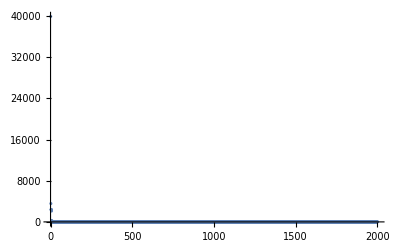

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SS,2];AppendTo[Solution30,Solution]]
```

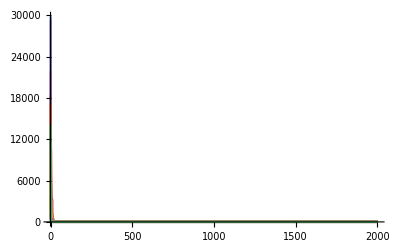

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{261.804,53.3995,29.3275,17.6875,17.6875,13.7595,11.7825,5.09498,2.9979,2.9979,0.392904,0.373384,0.328392,0.297032,0.095072,0.092388,0.086792,0.085452,0.083592,0.082008,0.081112,0.031692,0.018568,0.012312,0.011012,0.009392,0.000432,0.000388,0.000388,0.000388,0.0003,0.000108,0.0001,2.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{29851.,8854.04,2202.75,2056.14,440.912,294.299,13.3789,13.3425,13.3425,13.3243,10.343,10.3268,10.182,10.182,8.30598,8.20806,8.20806,8.07646,8.07646,8.06845,8.06663,8.06663,8.06663,8.06663,0.050633,0.050633,0.050633,0.021033,0.021033,0.020457,0.020457,0.001857,0.001857,0.001857,0.001857,0.001849,0.000537,0.000529,0.000529,0.000529,0.000529,0.000529,0.000225,0.000225,0.000025,0.000025,0.000025,0.000025,0.000025,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,1.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{9649.9,3061.2,1805.43,1166.97,872.372,482.999,363.307,332.035,277.537,239.079,221.742,94.2422,83.5536,37.2146,34.7315,30.1456,19.2308,18.6966,4.75352,3.60542,3.30762,2.1978,0.831724,0.524511,0.0874406,0.0854596,0.0304535,0.0173248,0.0122559,0.0097195,0.008301,0.00456947,0.00424717,0.00234587,0.0023292,0.00223333,0.0012078,0.00118087,0.00103927,0.000595267,0.0002522,0.0000737,0.0000486333,0.0000383667,0.000021,0.0000146,0.0000127333,0.0000121333,2.7×10^-6,2.16667×10^-6,1.36667×10^-6,1.36667×10^-6,1.36667×10^-6,9.66667×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.33333×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,9.×10^-7,6.33333×10^-7,6.33333×10^-7,6.33333×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.×10^-7,6.66667×10^-8,6.66667×10^-8,6.66667×10^-8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

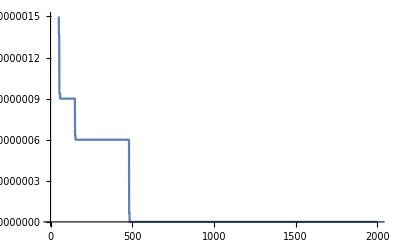

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{8163.18,1682.49,834.722,620.69,464.096,160.287,86.1974,72.111,16.3435,6.22538,2.93439,1.89488,1.73341,0.244069,0.177615,0.103032,0.08431,0.061569,0.053873,0.013161,0.009361,0.002152,0.001529,0.0011965,0.000972,0.0007705,0.0001,0.000043,0.0000305,0.000013,6.×10^-6,3.×10^-6,3.×10^-6,1.5×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{8309.58,3345.96,2400.9,1616.32,1200.26,739.722,662.815,663.603,643.89,632.91,629.791,254.48,238.227,109.703,109.58,95.2227,73.1628,73.1325,11.3562,10.1531,9.58685,7.91923,2.76123,1.65886,0.245954,0.24599,0.0626549,0.0342481,0.0310866,0.0248003,0.0239226,0.0176632,0.0176169,0.00834436,0.00831419,0.00826385,0.00522173,0.00520518,0.00493682,0.00283621,0.000988983,0.000180418,0.000119266,0.0000851111,0.0000618011,0.0000477916,0.0000396988,0.0000375993,7.07667×10^-6,5.83144×10^-6,3.92589×10^-6,3.92589×10^-6,3.92589×10^-6,3.61494×10^-6,3.61923×10^-6,3.61923×10^-6,3.61923×10^-6,3.61923×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.6232×10^-6,3.28511×10^-6,3.28511×10^-6,3.28511×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.28634×10^-6,3.65148×10^-7,3.65148×10^-7,3.65148×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*SS 5D*)
```

```mathematica
GA[SS,5]
```

0.000045

```mathematica
Solution
```

{314022.,178476.,131783.,69598.7,59332.5,51064.1,44649.1,43905.6,43905.6,33563.3,33516.3,29025.7,22987.5,5234.58,5234.46,4661.59,4399.6,4399.6,3541.59,3388.47,2001.35,1692.97,1692.97,1581.59,550.002,375.906,355.189,297.552,229.11,115.294,80.8392,80.8392,62.1432,52.5744,50.5752,37.0809,37.0809,34.5447,31.7337,28.8201,28.8201,27.4153,18.2605,17.8375,17.7897,16.6189,15.6787,9.1389,7.29248,5.59166,4.44008,4.44008,4.34448,4.21608,4.18219,1.68408,0.684535,0.681619,0.681619,0.574135,0.430419,0.430419,0.399139,0.399139,0.346635,0.346635,0.136739,0.136739,0.136739,0.136739,0.091619,0.091619,0.083259,0.071219,0.057819,0.037419,0.035139,0.023339,0.021499,0.016075,0.015303,0.015303,0.011907,0.010067,0.010067,0.009665,0.004147,0.003905,0.003745,0.003745,0.00373,0.003681,0.003681,0.003681,0.003681,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003673,0.003665,0.003649,0.002665,0.002665,0.002657,0.002649,0.002649,0.002649,0.002649,0.002649,0.002649,0.002649,0.001129,0.001129,0.001129,0.000489,0.000129,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000046,0.000046,0.000046,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045}

```mathematica
(*1 Solution plot*)
```

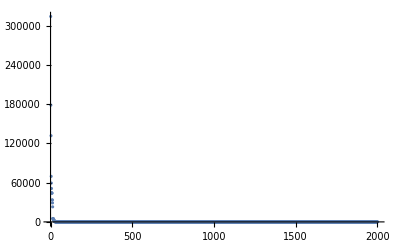

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SS,5];AppendTo[Solution30,Solution]]
```

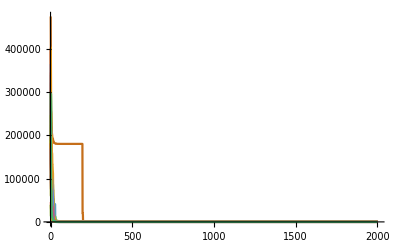

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{39449.6,14519.9,13034.1,12719.8,12272.4,12272.3,11027.3,11025.,6942.19,6486.38,6195.15,5995.8,5771.44,2560.55,1605.98,1585.5,1432.65,1389.9,1389.72,1389.52,1337.68,1319.5,1316.02,1256.43,1256.43,601.236,579.605,569.448,569.31,558.424,556.284,548.922,548.922,56.6018,48.3475,42.61,42.61,41.4523,11.8652,11.8652,7.92155,7.76819,4.67515,4.55204,4.55204,1.91147,1.91132,1.90994,1.90994,0.682519,0.679959,0.640759,0.423359,0.423359,0.422415,0.148779,0.112559,0.112559,0.112559,0.102799,0.092879,0.092879,0.092879,0.092874,0.092463,0.092458,0.092038,0.092038,0.091234,0.091234,0.091234,0.090754,0.090392,0.090392,0.090392,0.090392,0.090392,0.002392,0.002192,0.000592,0.000112,0.000112,0.000112,0.000112,0.000112,0.000052,0.000052,0.000052,0.000052,0.000052,0.000052,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{474091.,388276.,254493.,254086.,220568.,219687.,219210.,203523.,203523.,199318.,193836.,192315.,192290.,192054.,191089.,186697.,186697.,183922.,183922.,183625.,182546.,182074.,182074.,181829.,181802.,181387.,181386.,181334.,181141.,180879.,180879.,180870.,180870.,180274.,180273.,180258.,180235.,180234.,180231.,180225.,180215.,180096.,180096.,180096.,180084.,180084.,180079.,180071.,180070.,180070.,180053.,180050.,180050.,180050.,180049.,180048.,180039.,180032.,180032.,180031.,180031.,180029.,180026.,180024.,180024.,180024.,180022.,180022.,180012.,180010.,180004.,180004.,180004.,180004.,180004.,180004.,180004.,180004.,180002.,180002.,180002.,180002.,180002.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,180000.,20000.,20000.,16928.,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{252394.,194343.,158156.,131397.,111224.,88131.6,75828.1,58064.8,46315.9,42206.4,34100.3,32523.6,28675.8,26310.5,24541.5,21016.4,19251.2,16747.9,14132.2,12557.4,11977.5,10588.9,9950.08,9726.19,9394.81,9193.96,9081.89,8870.53,7300.68,7223.22,6701.35,6615.17,6546.54,6450.38,6361.08,6306.58,6260.35,6228.74,6163.55,6131.17,6126.95,6107.75,6102.07,6099.57,6095.05,6089.91,6078.2,6074.14,6073.07,6060.07,6058.47,6053.3,6029.56,6022.15,6021.5,6020.76,6017.67,6015.87,6014.34,6009.11,6008.97,6004.59,6004.42,6004.13,6004.06,6003.51,6003.3,6003.27,6002.84,6002.45,6002.06,6001.67,6001.64,6001.62,6001.15,6001.15,6001.06,6000.73,6000.65,6000.59,6000.44,6000.43,6000.43,6000.2,6000.19,6000.18,6000.13,6000.12,6000.12,6000.12,6000.1,6000.1,6000.02,6000.02,6000.02,6000.02,6000.02,6000.01,6000.01,6000.01,6000.01,6000.01,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,6000.,666.667,666.667,564.267,1.33333×10^-7,1.33333×10^-7,1.33333×10^-7,1.33333×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

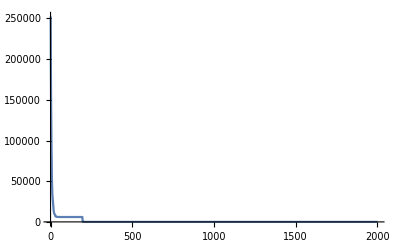

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{254832.,196490.,172269.,115865.,107640.,72906.1,49597.8,41366.5,27118.,22999.5,15887.6,13739.1,10184.,9777.29,7807.66,6646.89,5015.42,4570.16,4091.45,3145.91,2824.83,2331.03,1433.91,1330.5,1266.39,834.369,793.204,604.128,543.715,427.774,231.62,140.168,128.264,103.709,66.391,63.5477,42.2813,36.2548,25.9731,24.7791,15.3521,10.6414,8.83062,5.9965,5.06191,4.48952,4.38629,3.02747,2.68081,2.61712,2.44752,2.44752,1.33221,1.20952,1.03502,0.853499,0.824035,0.764593,0.589964,0.584888,0.309282,0.167204,0.165643,0.129051,0.12902,0.095198,0.078149,0.078149,0.0354155,0.033123,0.028563,0.0270215,0.0268915,0.0268915,0.013502,0.0123315,0.0123315,0.0079855,0.0073655,0.0070895,0.0046325,0.003448,0.002144,0.002144,0.0011805,0.0011785,0.0011785,0.0008905,0.000718,0.0005825,0.0005825,0.0005825,0.0005825,0.0004515,0.00045,0.000366,0.0000965,0.0000885,0.0000885,0.000073,0.0000525,0.0000525,0.0000505,0.000043,0.000043,0.0000245,0.000016,8.×10^-6,4.5×10^-6,4.5×10^-6,4.5×10^-6,4.5×10^-6,3.5×10^-6,3.×10^-6,3.×10^-6,1.5×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{106525.,90767.,72201.,73434.4,63445.7,60384.9,58665.9,51664.3,49496.4,48642.2,44603.4,44165.4,42794.2,42172.9,40926.1,37250.1,36437.8,35119.3,34436.,34169.8,33710.4,33371.,33462.1,33430.7,33453.2,33408.2,33404.3,33435.3,32913.2,32877.4,32913.3,32926.4,32938.7,32842.,32855.6,32859.7,32863.5,32869.1,32880.1,32884.4,32883.5,32863.7,32864.7,32865.1,32863.6,32864.6,32865.2,32864.4,32864.4,32866.3,32863.5,32863.6,32867.4,32868.7,32868.6,32868.6,32867.4,32866.5,32866.8,32867.5,32867.5,32868.,32867.4,32867.1,32867.1,32867.2,32866.8,32866.8,32865.1,32864.8,32863.8,32863.9,32863.9,32863.8,32863.9,32863.9,32863.9,32864.,32863.5,32863.5,32863.6,32863.6,32863.6,32863.4,32863.4,32863.4,32863.4,32863.3,32863.3,32863.3,32863.3,32863.3,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,32863.4,3651.48,3651.48,3090.62,7.30297×10^-7,7.30297×10^-7,7.30297×10^-7,7.30297×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*SS 10D*)
```

```mathematica
GA[SS,10]
```

0.

```mathematica
Solution
```

{1.43002×10^6,1.11791×10^6,1.11467×10^6,616377.,428739.,425644.,366108.,337659.,328269.,325032.,285024.,246196.,240297.,235887.,233532.,232411.,198442.,198442.,196945.,194241.,178937.,166155.,155571.,77969.9,76451.4,64070.7,57518.9,57518.9,41182.4,38182.6,35322.1,33326.3,33273.8,33022.4,32160.5,26342.5,26342.5,25697.9,22637.7,22229.5,21793.7,19673.9,18719.6,17492.1,17184.8,17184.8,15691.8,14473.3,13061.9,9518.6,9518.6,8342.25,8013.4,8013.4,7996.1,7577.77,7577.77,7577.77,7577.77,3273.74,3216.95,2601.68,2373.73,2199.84,1972.02,1915.24,1897.8,1305.46,1305.46,1294.25,1281.04,1280.89,1182.72,1139.78,1139.78,1139.78,1133.06,550.14,549.97,544.713,530.514,486.978,194.449,194.449,164.748,164.748,164.721,163.445,159.748,142.653,133.004,133.004,133.004,133.004,133.004,132.352,132.352,132.352,108.951,108.758,106.281,106.281,105.552,105.552,105.27,103.344,103.206,66.8165,66.8165,66.8138,65.8641,63.9069,63.9069,63.9069,45.4044,45.4044,41.5448,41.5448,41.5448,41.5448,41.5448,40.387,37.7628,37.7628,37.7628,37.7628,37.7291,37.7291,37.7291,37.7283,36.8251,36.8251,36.8251,36.8251,34.9627,34.9627,34.9627,34.9627,34.9627,34.9627,34.9627,34.1171,34.1171,32.9107,31.1087,31.1087,30.7663,27.0287,27.0287,27.0287,27.0287,27.0287,27.0287,27.0287,27.0287,26.868,26.868,26.868,26.8669,26.8484,26.8484,26.8347,26.8347,26.8347,24.9124,24.9124,24.9124,24.9124,24.9108,24.7554,24.7554,24.7554,24.7554,24.7522,24.6616,24.6616,4.00242,3.98319,3.11924,3.11924,1.18644,1.18642,1.18642,1.18618,1.18618,1.18618,1.18578,1.18578,1.18578,1.16218,1.16218,1.16218,1.16218,1.16214,1.16214,1.16178,1.02714,1.02714,1.02714,1.02714,0.154068,0.154068,0.154068,0.154068,0.019144,0.019144,0.019144,0.019144,0.019144,0.019144,0.018176,0.018176,0.018176,0.014344,0.014344,0.014344,0.014344,0.014344,0.014344,0.013246,0.013246,0.013246,0.013246,0.013246,0.013246,0.013246,0.011424,0.011424,0.011424,0.011424,0.011326,0.011326,0.011281,0.011281,0.011281,0.011281,0.011206,0.011206,0.011206,0.011206,0.011206,0.011206,0.011206,0.011206,0.009206,0.009206,0.009206,0.009206,0.009206,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.009038,0.008038,0.008038,0.008038,0.008038,0.007318,0.007318,0.003238,0.003238,0.003238,0.003238,0.003238,0.002598,0.002598,0.002598,0.002598,0.002598,0.002598,0.002598,0.002598,0.002472,0.002472,0.002472,0.002472,0.002438,0.002438,0.002438,0.002438,0.002338,0.001718,0.001718,0.001718,0.001718,0.001718,0.001618,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00127,0.00117,0.00117,0.00117,0.00117,0.00117,0.00117,0.00117,0.00117,0.00117,0.00117,0.001165,0.001165,0.001165,0.001165,0.001038,0.001038,0.001038,0.001033,0.001033,0.001033,0.001033,0.001033,0.001033,0.001033,0.001033,0.001033,0.001033,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000733,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.000617,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.00061,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.0006,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

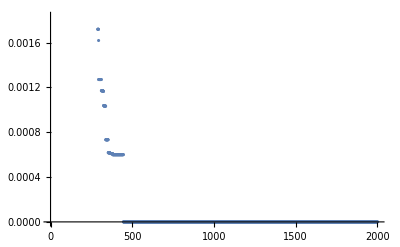

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[SS,10];AppendTo[Solution30,Solution]]
```

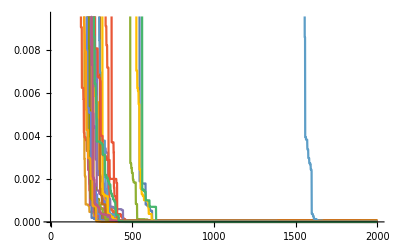

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{889901.,889901.,882276.,789746.,714022.,588843.,562423.,556204.,538582.,502555.,473876.,468030.,467177.,425772.,406073.,354210.,352524.,303222.,292218.,256540.,229053.,229053.,225807.,172917.,171640.,146164.,143999.,140250.,140250.,140041.,138788.,126864.,124462.,110907.,110907.,110512.,110512.,107602.,107602.,107602.,105612.,105612.,102993.,102993.,102592.,102592.,102572.,102392.,102371.,102344.,102344.,102324.,102146.,102112.,102104.,101750.,101691.,101662.,101662.,101325.,101307.,101307.,101307.,101303.,101263.,101263.,101263.,100980.,100980.,100980.,97550.8,96075.4,78952.2,69078.8,65819.,56574.4,1855.41,1855.41,1785.21,1666.69,715.997,715.974,715.974,691.123,636.189,636.189,636.189,629.785,557.178,557.178,557.178,538.134,536.663,477.958,477.958,477.844,468.994,459.939,426.915,426.915,426.573,421.875,413.625,413.383,413.383,413.383,413.383,413.376,413.036,395.162,388.67,388.651,388.58,382.226,382.226,382.226,364.272,56.0345,56.0345,56.0246,38.0256,38.0256,38.0256,37.3618,34.8816,34.8816,34.8816,30.6008,30.6008,28.4178,28.4178,28.4178,28.2154,25.0122,25.0122,6.96079,6.96079,6.91519,3.51071,3.44639,3.10543,3.10543,3.10543,2.97919,2.97919,2.77069,2.77069,2.77069,2.7696,2.68682,2.68682,2.67872,2.67872,2.67872,2.67872,2.60672,2.56562,2.56562,2.56562,2.49237,2.47887,2.47887,2.45697,2.45697,2.45697,2.33336,2.33336,2.3325,2.3325,2.07725,2.07725,2.06264,2.06264,1.98193,1.93673,1.93673,1.93673,1.93673,0.475133,0.475133,0.475133,0.475133,0.475133,0.475133,0.474628,0.474628,0.428733,0.428733,0.358977,0.358977,0.358977,0.358865,0.358865,0.358865,0.358865,0.358865,0.284465,0.249665,0.249665,0.249265,0.249265,0.249265,0.170465,0.170465,0.170465,0.170465,0.170465,0.170465,0.170465,0.161585,0.161585,0.096065,0.096065,0.096065,0.095815,0.095815,0.095815,0.062815,0.062815,0.062815,0.062815,0.061495,0.05861,0.05861,0.038947,0.038947,0.038947,0.038807,0.038807,0.034207,0.034207,0.034207,0.033647,0.033647,0.027487,0.027487,0.027487,0.027487,0.027487,0.026815,0.019087,0.019087,0.019087,0.014236,0.014236,0.014236,0.014236,0.014236,0.012167,0.012167,0.012167,0.012167,0.012167,0.012163,0.010375,0.010375,0.010327,0.010327,0.010327,0.010227,0.010227,0.010207,0.010107,0.010107,0.010107,0.010107,0.010107,0.009867,0.009407,0.009407,0.008059,0.008059,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.008055,0.006735,0.006735,0.006735,0.006735,0.006735,0.006735,0.006735,0.006735,0.006735,0.006685,0.006685,0.006685,0.006685,0.006685,0.006535,0.006535,0.006535,0.006535,0.003997,0.003997,0.003997,0.003997,0.003997,0.003997,0.003997,0.003992,0.003992,0.003992,0.003992,0.003992,0.003108,0.003108,0.003108,0.003108,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.003092,0.002973,0.002973,0.002973,0.002972,0.002972,0.002972,0.002972,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.002876,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001996,0.001804,0.001804,0.001804,0.001804,0.001804,0.000204,0.000204,0.000204,0.000204,0.000204,0.000204,0.000204,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000076,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,0.000024,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,2.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{2.57813×10^6,1.95443×10^6,1.89407×10^6,1.8443×10^6,1.32115×10^6,1.32115×10^6,1.03721×10^6,1.03721×10^6,997469.,898857.,839107.,799181.,788584.,662237.,659215.,609589.,585957.,551080.,541944.,455493.,450185.,403043.,359808.,299164.,297133.,261767.,243792.,190523.,190523.,161396.,156436.,131892.,130863.,128385.,123421.,120220.,120220.,107447.,105085.,67137.7,62678.5,60414.1,56305.9,55939.8,37371.5,29593.3,29375.2,27871.9,27871.9,26225.2,25821.3,25821.3,19698.3,19698.3,14208.1,14208.1,14157.1,14133.6,13917.7,13917.7,12638.1,12638.1,12638.1,12434.,10767.1,10353.2,10347.9,10342.7,6474.28,6474.28,6465.51,6464.73,4152.62,4152.6,4028.54,3595.44,3115.17,3115.17,3091.83,3091.83,3091.83,1853.99,1853.99,1853.99,1853.99,1853.02,1852.63,1851.61,1848.08,1406.78,1038.,519.068,516.738,516.738,353.76,353.758,352.898,323.167,320.461,316.776,160.064,160.064,160.064,154.064,154.064,154.013,154.013,153.794,153.794,153.743,114.121,114.07,107.761,92.3532,92.29,71.0849,71.0849,71.0849,71.0217,34.8957,34.8268,34.8268,34.3301,34.3301,34.3301,34.3301,34.3169,34.1564,16.1632,16.1632,16.1632,15.9865,15.9865,14.5814,14.5814,12.6231,12.5468,12.5468,12.4267,12.4267,12.4267,7.26166,7.26166,7.26166,7.26166,7.26166,7.26166,7.26166,7.20286,7.19549,5.73824,5.73824,5.73824,5.67944,5.30144,5.30144,4.44024,4.44024,4.44024,4.44024,4.44024,4.44024,4.44024,3.92623,3.92623,3.92623,3.92159,3.90718,3.52863,3.52863,3.52863,3.52863,3.52863,2.72801,1.93105,1.93105,1.08705,1.08705,0.947852,0.947852,0.947252,0.920684,0.578252,0.578252,0.578252,0.504092,0.504092,0.504092,0.504092,0.5033,0.499148,0.498972,0.49242,0.489068,0.489068,0.489068,0.489068,0.433588,0.433588,0.433588,0.313876,0.313876,0.112276,0.112276,0.112276,0.109388,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104596,0.104595,0.094333,0.08694,0.08694,0.08694,0.086422,0.086422,0.08595,0.072735,0.072735,0.072735,0.042643,0.042643,0.042643,0.042643,0.042643,0.042643,0.042643,0.042643,0.042643,0.040938,0.033258,0.033258,0.033258,0.033258,0.033258,0.033258,0.019562,0.019562,0.019562,0.019562,0.018794,0.018794,0.018794,0.017906,0.017906,0.017906,0.017906,0.016846,0.016846,0.016846,0.015145,0.015145,0.015145,0.015145,0.015145,0.015145,0.015109,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.014207,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.013007,0.012507,0.012507,0.012507,0.012507,0.012507,0.012507,0.012507,0.012507,0.001307,0.001307,0.001307,0.001307,0.001307,0.001307,0.001307,0.001307,0.001307,0.001235,0.001235,0.001235,0.001235,0.001235,0.001235,0.001235,0.001235,0.001235,0.001235,0.001225,0.001225,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.001191,0.000391,0.000391,0.000391,0.000391,0.000391,0.000391,0.000391,0.000335,0.000335,0.000335,0.000335,0.000335,0.000335,0.000335,0.000335,0.000335,0.000279,0.000276,0.000276,0.000276,0.000276,0.000276,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000225,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000129,0.000126,0.000126,0.000126,0.000126,0.000126,0.000126,0.000126,0.000029,0.000029,0.000029,0.000029,0.000029,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.000026,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{1.82377×10^6,1.64862×10^6,1.49401×10^6,1.28104×10^6,1.16556×10^6,1.01254×10^6,936583.,853336.,778167.,715957.,675839.,625281.,594876.,552565.,520394.,491451.,464628.,450912.,429322.,402957.,388004.,362644.,339844.,323671.,302793.,285669.,270943.,259465.,248067.,240474.,229500.,220529.,216173.,209247.,206089.,201083.,196530.,192901.,189836.,186839.,184758.,182035.,180431.,179312.,175615.,174284.,168667.,167944.,165465.,164787.,163773.,162236.,161214.,160298.,159075.,156602.,154611.,154008.,153650.,153369.,152935.,152506.,150694.,148819.,148624.,148350.,148026.,147360.,133733.,133433.,132961.,128977.,126441.,123414.,122930.,121499.,119529.,117336.,117288.,116536.,116234.,116146.,115899.,115833.,115532.,115459.,115441.,115285.,115237.,115006.,114982.,114926.,114760.,114751.,114638.,114617.,114593.,114447.,114440.,114381.,114313.,114298.,114281.,114272.,114254.,114237.,114217.,114208.,114203.,114186.,114180.,114168.,114164.,114162.,114149.,114145.,114139.,114122.,114114.,114106.,114103.,114094.,114080.,114079.,114072.,114066.,114064.,114062.,114055.,114051.,114049.,114047.,114046.,114045.,113388.,108707.,108704.,108703.,108033.,108022.,108022.,108021.,108019.,108017.,108017.,108016.,108014.,108013.,108012.,108012.,108012.,108012.,108011.,108010.,108010.,108010.,108008.,108008.,108007.,108007.,108007.,108007.,108007.,108007.,108006.,108006.,108005.,108005.,108005.,108005.,108004.,108004.,108004.,108004.,108003.,108003.,108003.,108003.,108003.,108003.,97363.1,97362.9,97362.8,97335.6,97335.6,97100.8,96897.4,96897.4,96897.3,96097.2,96097.2,96097.1,96050.5,96050.5,96050.5,96050.4,96050.,96035.4,85796.3,85777.6,85777.6,85107.3,79783.5,79783.5,71737.3,69905.6,69476.6,69224.6,69223.2,68802.5,68708.1,68073.5,67776.3,67775.4,67719.3,67719.3,67712.9,67419.3,67419.3,66538.3,66538.2,66531.6,66531.5,66487.2,66487.2,66470.6,66470.5,66470.5,66044.1,66044.,66043.9,66043.9,58093.2,58091.4,58011.,58010.8,58010.7,57972.8,57111.7,57111.7,57110.,57110.,57094.4,57079.8,57079.8,57067.,57067.,57066.9,57060.1,57042.3,57007.2,57007.1,57007.1,57006.9,57006.8,57006.8,57006.8,57006.2,57006.2,57006.2,57005.4,57005.,57003.6,57003.6,57003.6,57003.6,57003.5,57003.5,57003.5,57003.4,57003.4,57003.4,57003.4,57003.4,57003.4,57001.7,57001.7,57001.6,57001.3,57001.3,57001.2,57000.9,57000.9,57000.9,57000.9,57000.9,57000.9,57000.9,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.8,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,57000.,43666.7,43666.7,42601.3,42601.3,42601.3,42266.3,42266.3,42025.9,42025.9,42025.9,42025.9,42025.9,42024.3,42024.3,42024.3,42015.8,42015.8,42015.8,42014.2,42014.2,42014.2,42003.,42002.9,42002.9,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.4,42001.3,42001.3,42001.3,42001.3,42001.3,42001.3,42001.2,42001.2,42001.2,42001.2,42001.2,42001.2,31340.6,31336.3,31334.3,31266.5,30204.3,30136.,29210.6,27722.3,27721.9,27721.9,27295.8,27236.1,27166.6,27160.4,27148.7,27125.6,27124.4,27124.4,27124.4,27124.4,27124.4,27124.4,27099.,27075.7,27075.7,27036.3,27036.3,27036.1,27019.7,27019.6,27019.,27019.,27015.3,27015.3,27015.3,27014.5,27014.5,27012.4,27012.4,21678.9,21576.5,21576.5,21332.3,21332.3,21105.5,21105.5,21102.4,21102.4,21102.4,21102.1,21100.7,21023.2,21023.2,21023.2,21023.2,21022.6,21012.9,21011.8,21010.6,21010.6,21010.6,21010.6,21010.3,21010.,21008.9,21008.9,21008.9,21008.9,21008.9,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.6,21008.5,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,21000.,2331.47,2331.05,1974.97,1972.97,880.088,880.088,793.094,793.094,618.812,618.812,618.812,616.691,486.527,486.308,486.308,481.363,481.363,328.349,328.343,272.265,271.716,220.451,220.451,220.422,209.191,139.464,131.97,131.97,127.41,123.355,87.0841,86.8346,79.0621,39.4792,39.4792,39.4792,39.4792,39.4792,39.4792,39.479,38.8254,38.8252,14.2765,14.2765,14.2195,13.9206,13.9206,13.9206,13.8534,13.6521,13.6521,13.6521,13.6521,13.6521,13.3398,13.3339,13.3339,13.3339,13.3336,13.067,13.067,13.067,13.067,0.132575,0.132575,0.079242,0.079242,0.079242,0.079242,0.079242,0.079242,0.079242,0.07889,0.07889,0.07889,0.075242,0.0272053,0.0272053,0.0204717,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0125891,0.0115891,0.0115891,0.0115891,0.0115891,0.00358117,0.00358117,0.00351637,0.00268397,0.00268397,0.00268397,0.00268397,0.00268397,0.00268397,0.00229637,0.00229637,0.00229637,0.00229637,0.00229637,0.00229637,0.00229637,0.00229637,0.00229637,0.00137903,0.00137903,0.0013781,0.0013781,0.0013781,0.000496767,0.000496767,0.000496767,0.000496767,0.000292767,0.000292767,0.000292767,0.0001381,0.0001381,0.0001381,0.0001381,0.0001381,0.0001342,0.0001342,0.0001342,0.0001342,0.0001342,0.0001342,0.0001342,0.0001342,0.000121,0.000118867,0.000118867,0.000118867,0.000118867,0.000118867,0.000105667,0.000105667,0.000105667,0.000105667,0.000105667,0.000105667,0.0000975333,0.0000975333,0.0000975333,0.0000975333,0.0000975333,0.0000975333,0.0000975333,0.0000954,0.0000954,0.0000879333,0.0000879333,0.0000879333,0.0000879333,0.0000879333,0.0000855333,0.0000194,0.0000194,0.0000194,0.0000194,0.0000194,0.0000186,0.0000186,0.0000186,0.0000162,0.0000162,0.0000153,0.0000153,0.0000153,0.0000119333,0.0000114333,0.0000114333,0.0000114333,0.0000114333,0.0000114333,0.0000114333,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000112667,0.0000111333,9.13333×10^-6,9.13333×10^-6,9.13333×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.73333×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,8.2×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,6.9×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.3×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6,5.1×10^-6}

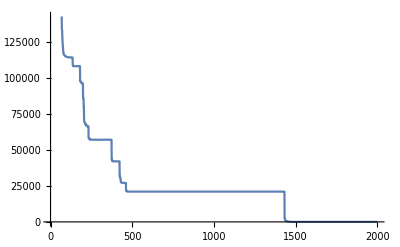

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{1.78527×10^6,1.61019×10^6,1.47179×10^6,1.25011×10^6,1.11925×10^6,962151.,935872.,852452.,745211.,679182.,634247.,612147.,557451.,523336.,500026.,440065.,407383.,400915.,348743.,325569.,299024.,290024.,278832.,271116.,240548.,227473.,203192.,190032.,178650.,162325.,152748.,139604.,136454.,119646.,117164.,115366.,115366.,107524.,106344.,99596.4,98601.5,85955.4,85366.9,84150.9,63707.3,59818.3,59565.4,58668.7,52180.8,51356.4,50302.8,47133.5,43577.,43577.,40745.2,18521.2,17562.,16235.2,16127.3,15077.8,14382.2,12942.5,11073.,8734.32,8592.56,8465.96,8245.69,8245.69,7295.82,6239.14,6234.75,5904.59,4087.4,3829.3,3808.24,2484.74,2355.06,2000.93,1965.79,1563.48,1070.98,1070.94,1064.48,963.59,963.202,847.139,786.669,674.722,637.692,522.785,521.482,502.427,486.73,467.005,365.826,350.364,339.85,330.136,325.086,313.584,298.986,268.905,268.905,237.778,237.301,177.697,162.948,162.839,162.839,149.523,132.686,129.687,126.532,125.303,96.5171,90.1297,90.0269,75.2548,75.0549,61.7561,53.1445,52.7565,39.4909,39.1406,34.6058,34.6058,26.7682,24.9102,17.5706,17.5706,15.4883,15.3999,15.0736,14.371,14.371,10.6959,9.90161,9.87369,6.3927,6.09231,5.62651,4.56881,4.51907,4.51907,4.51907,3.86129,3.46911,3.46911,3.46911,3.46548,3.34141,3.34141,3.33747,3.33747,3.33431,3.0017,2.98115,2.96214,2.96214,2.92552,2.91877,2.91877,2.62036,2.62036,2.62036,2.50387,2.17138,2.17095,2.17095,2.04333,2.0433,2.03599,2.03184,1.71284,1.6874,1.6676,1.1826,1.16521,0.894567,0.64635,0.64635,0.64623,0.528015,0.528015,0.52644,0.48936,0.483955,0.466413,0.431535,0.431139,0.406086,0.319354,0.319354,0.319354,0.319354,0.319354,0.282112,0.264712,0.26471,0.23174,0.23174,0.210392,0.190285,0.179377,0.179117,0.179117,0.149217,0.149217,0.149217,0.144623,0.144623,0.115469,0.115469,0.115469,0.114461,0.114461,0.114461,0.11358,0.11358,0.11358,0.11358,0.11358,0.093841,0.093841,0.0832255,0.081737,0.0803315,0.073724,0.073724,0.073724,0.0721625,0.0721625,0.0459335,0.0459335,0.0459335,0.0459335,0.044822,0.0448215,0.0447485,0.043896,0.0400465,0.040046,0.040046,0.026852,0.026852,0.020029,0.019587,0.019585,0.017526,0.017526,0.017109,0.017109,0.0137955,0.0120025,0.011364,0.011364,0.011364,0.011364,0.010644,0.010644,0.010644,0.010644,0.0101645,0.0101645,0.009438,0.0086895,0.0086495,0.0086495,0.0086495,0.0075495,0.006126,0.006126,0.006126,0.0060655,0.0060655,0.0060655,0.0059765,0.005904,0.005694,0.005081,0.0043725,0.0037735,0.0037735,0.0037735,0.0037735,0.00305,0.00305,0.00305,0.00305,0.0029525,0.0022095,0.0022095,0.002208,0.002208,0.002208,0.002208,0.002208,0.002208,0.002188,0.002188,0.0021875,0.0021875,0.001857,0.0017885,0.0017885,0.0017885,0.0017885,0.0016655,0.0016655,0.0016495,0.0016095,0.0016095,0.0016095,0.0015815,0.001549,0.001549,0.0015185,0.001237,0.001237,0.0011695,0.0011695,0.0011695,0.0011695,0.0011695,0.0011695,0.001077,0.001043,0.001043,0.001043,0.001014,0.0009955,0.0009915,0.000759,0.000759,0.000759,0.000759,0.00064,0.000604,0.000604,0.000604,0.000604,0.000604,0.000487,0.000487,0.000487,0.000487,0.000487,0.000487,0.0004865,0.0004865,0.000362,0.000362,0.0003295,0.0003155,0.0003155,0.0003155,0.0003155,0.0003155,0.0002565,0.0002565,0.0002565,0.0002565,0.0002565,0.000183,0.000173,0.000163,0.000163,0.000163,0.000163,0.000163,0.000163,0.000163,0.000106,0.0001045,0.0001045,0.0001045,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.0000755,0.0000755,0.0000755,0.0000755,0.0000755,0.0000665,0.0000665,0.0000665,0.000051,0.000051,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000049,0.000042,0.000033,0.000033,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000325,0.0000245,0.0000245,0.0000245,0.0000245,0.0000245,0.0000245,0.0000245,0.0000245,0.0000175,0.0000175,0.0000175,0.0000175,0.0000175,0.0000175,0.0000175,0.0000175,0.0000175,0.0000105,9.5×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,9.×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,8.5×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,7.×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,6.5×10^-6,3.5×10^-6,2.5×10^-6,2.5×10^-6,2.5×10^-6,2.5×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{398567.,321088.,295085.,324834.,261549.,277442.,257036.,230580.,221316.,221705.,220667.,230899.,207110.,208502.,193304.,195047.,201054.,205173.,202644.,198504.,204832.,194854.,186548.,186896.,186462.,190217.,182622.,184491.,185251.,186562.,193021.,196141.,194171.,196639.,197947.,199032.,201144.,200645.,202097.,202437.,203233.,204024.,203969.,203913.,206011.,206337.,202898.,203034.,202759.,202747.,202588.,202717.,202678.,202493.,202598.,203524.,204046.,204163.,204126.,204091.,203907.,203656.,203623.,204663.,204685.,204642.,204516.,204411.,196883.,196898.,196896.,195607.,196196.,196668.,196655.,197312.,198211.,198571.,198590.,198832.,198867.,198890.,198976.,198970.,198968.,198978.,198977.,198915.,198930.,198904.,198909.,198934.,198931.,198932.,198971.,198966.,198976.,199058.,199057.,199051.,199079.,199079.,199060.,199061.,199052.,199057.,199052.,199054.,199052.,199059.,199055.,199043.,199043.,199042.,199048.,199047.,199044.,199054.,199057.,199059.,199061.,199065.,199071.,199072.,199067.,199070.,199071.,199067.,199068.,199064.,199065.,199064.,199064.,199064.,198873.,199380.,199373.,199372.,199710.,199715.,199715.,199716.,199715.,199715.,199715.,199715.,199714.,199714.,199714.,199714.,199714.,199714.,199713.,199714.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,199713.,194253.,194253.,194253.,194261.,194261.,194337.,194409.,194409.,194409.,194757.,194757.,194757.,194780.,194780.,194780.,194780.,194780.,194787.,172556.,172529.,172529.,171616.,167067.,167067.,163329.,162832.,162805.,162874.,162874.,163015.,163052.,163141.,163164.,163164.,163188.,163188.,163188.,163227.,163227.,163437.,163437.,163439.,163439.,163454.,163454.,163459.,163459.,163459.,163617.,163617.,163617.,163617.,149548.,149546.,149461.,149461.,149461.,149421.,148595.,148595.,148595.,148595.,148582.,148569.,148569.,148562.,148562.,148562.,148564.,148549.,148518.,148519.,148519.,148518.,148518.,148518.,148518.,148519.,148519.,148519.,148518.,148518.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148516.,148515.,148515.,148515.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148514.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,148513.,128640.,128640.,128718.,128718.,128718.,128797.,128797.,128870.,128870.,128870.,128870.,128870.,128870.,128870.,128870.,128873.,128873.,128873.,128874.,128874.,128874.,128877.,128877.,128877.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,128878.,119015.,119012.,119011.,118971.,118984.,119001.,118604.,118423.,118424.,118424.,118470.,118481.,118494.,118495.,118497.,118502.,118502.,118502.,118502.,118502.,118502.,118502.,118508.,118513.,118513.,118521.,118521.,118521.,118525.,118525.,118525.,118525.,118526.,118526.,118526.,118526.,118526.,118527.,118527.,114951.,114954.,114954.,114972.,114972.,115003.,115003.,115003.,115003.,115003.,115004.,115004.,115017.,115017.,115017.,115017.,115018.,115019.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115020.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,115022.,12770.,12767.7,10817.4,10806.4,4820.44,4820.44,4343.95,4343.95,3389.37,3389.37,3389.37,3377.76,2664.82,2663.62,2663.62,2636.53,2636.53,1798.44,1798.41,1491.25,1488.25,1207.46,1207.46,1207.3,1145.79,763.875,722.828,722.828,697.853,675.642,476.979,475.613,433.041,216.237,216.237,216.237,216.237,216.237,216.237,216.235,212.655,212.654,78.1956,78.1956,77.8832,76.246,76.246,76.246,75.878,74.7755,74.7755,74.7755,74.7755,74.7755,73.0652,73.0329,73.0329,73.0329,73.0313,71.5707,71.5707,71.5707,71.5707,0.726106,0.726106,0.433987,0.433987,0.433987,0.433987,0.433987,0.433987,0.433987,0.432059,0.432059,0.432059,0.412078,0.148971,0.148971,0.112089,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0689141,0.0634368,0.0634368,0.0634368,0.0634368,0.0195758,0.0195758,0.0192208,0.0146616,0.0146616,0.0146616,0.0146616,0.0146616,0.0146616,0.0125386,0.0125386,0.0125386,0.0125386,0.0125386,0.0125386,0.0125386,0.0125386,0.0125386,0.00751421,0.00751421,0.0075091,0.0075091,0.0075091,0.00268189,0.00268189,0.00268189,0.00268189,0.0015646,0.0015646,0.0015646,0.000717626,0.000717626,0.000717626,0.000717626,0.000717626,0.000696274,0.000696274,0.000696274,0.000696274,0.000696274,0.000696274,0.000696274,0.000696274,0.000624013,0.000612335,0.000612335,0.000612335,0.000612335,0.000612335,0.000540085,0.000540085,0.000540085,0.000540085,0.000540085,0.000540085,0.000495575,0.000495575,0.000495575,0.000495575,0.000495575,0.000495575,0.000495575,0.000483901,0.000483901,0.000443048,0.000443048,0.000443048,0.000443048,0.000443048,0.000429918,0.0000704653,0.0000704653,0.0000704653,0.0000704653,0.0000704653,0.0000663021,0.0000663021,0.0000663021,0.0000540207,0.0000540207,0.0000495296,0.0000495296,0.0000495296,0.0000338301,0.0000317508,0.0000317508,0.0000317508,0.0000317508,0.0000317508,0.0000317508,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000310805,0.0000305532,0.0000239594,0.0000239594,0.0000239594,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000236352,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000230426,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000221007,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213348,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000213612,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194212,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446,0.0000194446}

```mathematica
(*TRID FUNCTION*)
```

```mathematica
Trid[x_]:=Module[{l=Length@x},Sum[(x[[i]]-1)^2,{i,l}]-Sum[x[[i]]*x[[i-1]],{i,2,l}]]
```

```mathematica
(*Trid 2D*)
```

```mathematica
GA[Trid,2]
```

-2.

```mathematica
Solution
```

{9929.07,5949.12,5949.12,923.913,923.913,885.019,191.639,22.6618,16.6098,0.323899,-0.253241,-1.71745,-1.71745,-1.71939,-1.75749,-1.79019,-1.86829,-1.86897,-1.98385,-1.98385,-1.98385,-1.9841,-1.99173,-1.99173,-1.99173,-1.99173,-1.99743,-1.99743,-1.99771,-1.99785,-1.99827,-1.99985,-1.99985,-1.9999,-1.9999,-1.9999,-1.99992,-1.99999,-1.99999,-1.99999,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

```mathematica
(*1 Solution plot*)
```

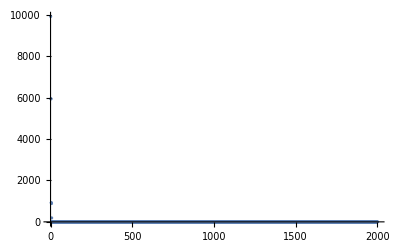

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[Trid,2];AppendTo[Solution30,Solution]]
```

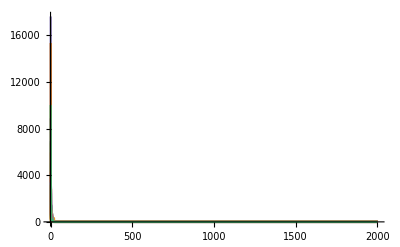

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{105.966,37.2546,37.2546,26.5386,25.7916,6.83459,6.83459,3.76099,3.76099,3.19259,3.01271,2.61113,2.57701,1.59113,1.57301,1.53313,1.496,1.0901,1.0901,1.0878,1.08352,1.0685,1.0501,1.04203,1.0404,1.02722,1.02722,1.02722,1.00122,1.00122,1.00122,1.00122,1.00122,1.00023,1.00023,1.00003,1.00003,1.00003,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,-0.9697,-1.01088,-1.2097,-1.9981,-1.9981,-1.9981,-1.9988,-1.99967,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9997,-1.9999,-1.9999,-1.99992,-1.99994,-1.99994,-1.99994,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{17626.9,3147.86,2882.73,2381.84,815.703,815.703,352.748,287.74,287.74,0.087559,0.087559,-0.646441,-1.05684,-1.8243,-1.93464,-1.9429,-1.98504,-1.9893,-1.99834,-1.9986,-1.99867,-1.99972,-1.99972,-1.99972,-1.99972,-1.99972,-1.99974,-1.99975,-1.99975,-1.99975,-1.99976,-1.99976,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99992,-1.99995,-1.99996,-1.99999,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

```mathematica
average=Mean@Solution30
```

{3992.,1162.67,720.428,525.055,374.693,341.639,261.528,197.597,160.358,124.931,88.1825,60.8069,42.0344,38.2654,29.684,21.3904,18.2598,17.2325,15.8758,14.8329,12.9489,1.81244,0.475159,0.0014312,-0.108544,-0.715067,-0.785389,-0.925509,-1.06151,-1.14429,-1.24983,-1.32005,-1.35617,-1.41534,-1.41939,-1.4207,-1.43345,-1.43643,-1.43918,-1.46312,-1.53125,-1.53126,-1.5647,-1.56488,-1.56491,-1.56527,-1.56616,-1.56623,-1.56624,-1.56627,-1.56657,-1.56658,-1.56658,-1.56659,-1.56659,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.5666,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56667,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.56707,-1.62552,-1.65467,-1.65467,-1.65983,-1.66538,-1.66557,-1.66557,-1.66558,-1.66558,-1.66561,-1.66657,-1.66657,-1.66657,-1.6666,-1.6666,-1.66661,-1.66661,-1.66661,-1.66666,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.66667,-1.72764,-1.73333,-1.73333,-1.73867,-1.73867,-1.74033,-1.74033,-1.74119,-1.74119,-1.74133,-1.74133,-1.76557,-1.76557,-1.76584,-1.76584,-1.76584,-1.76584,-1.76638,-1.76638,-1.76638,-1.76645,-1.76645,-1.76647,-1.76647,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76667,-1.76693,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.79967,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.8,-1.86667,-1.86667,-1.86667,-1.87467,-1.875,-1.87572,-1.87599,-1.87599,-1.87599,-1.87604,-1.89014,-1.89028,-1.89105,-1.89105,-1.89115,-1.89318,-1.89319,-1.89507,-1.89509,-1.96148,-1.96352,-1.97051,-1.99843,-1.99843,-1.99899,-1.99934,-1.99937,-1.99937,-1.99974,-1.99988,-1.99988,-1.99988,-1.99989,-1.9999,-1.9999,-1.99991,-1.99993,-1.99996,-1.99997,-1.99997,-1.99997,-1.99998,-1.99998,-1.99998,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

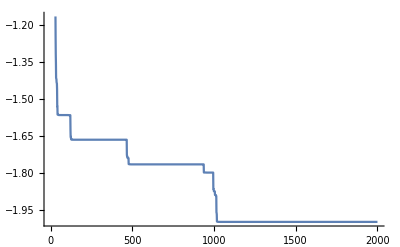

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{2939.33,818.919,505.196,329.147,213.754,213.724,85.8596,60.0114,49.2423,7.99812,6.24211,1.97879,0.904049,0.647038,0.167431,0.100031,-1.22967,-1.29318,-1.60542,-1.63808,-1.75571,-1.84142,-1.8488,-1.89903,-1.92165,-1.94693,-1.96098,-1.96987,-1.97754,-1.98742,-1.99058,-1.99833,-1.99889,-1.99904,-1.99956,-1.99979,-1.9998,-1.9998,-1.99989,-1.99991,-1.99992,-1.99996,-1.99996,-1.99999,-1.99999,-1.99999,-1.99999,-1.99999,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{4267.19,920.661,732.906,548.464,395.791,379.525,349.811,266.72,214.328,184.608,169.107,117.363,88.6566,86.6663,70.8965,61.4243,61.0221,60.8428,60.305,58.8631,58.5219,9.88076,5.15318,4.85359,4.75128,2.95345,2.76846,2.35265,1.95321,1.82693,1.54515,1.36831,1.30775,1.26185,1.26184,1.2621,1.26352,1.2647,1.26578,1.22384,1.13675,1.13675,1.13558,1.13516,1.13518,1.13531,1.13517,1.1352,1.1352,1.13521,1.13533,1.13533,1.13533,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13534,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13512,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.13419,1.03918,1.02641,1.02641,1.02672,1.02793,1.02798,1.02798,1.02799,1.02799,1.02799,1.0283,1.0283,1.0283,1.02831,1.02831,1.02831,1.02831,1.02832,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,1.02833,0.912466,0.907187,0.907187,0.903189,0.903189,0.90213,0.90213,0.901623,0.901623,0.901538,0.901538,0.89736,0.89736,0.897424,0.897424,0.897424,0.897424,0.89756,0.89756,0.89756,0.897576,0.897576,0.897582,0.897582,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.897634,0.896479,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.762394,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.761124,0.571346,0.571346,0.571346,0.560368,0.55998,0.559162,0.558866,0.558866,0.558862,0.558812,0.548521,0.548474,0.548225,0.548225,0.548196,0.547709,0.547706,0.547457,0.547456,0.188705,0.180948,0.144725,0.00824786,0.00824786,0.0051944,0.00341234,0.00341131,0.00341141,0.00134899,0.000605459,0.000605459,0.000605459,0.000527322,0.000477957,0.000477957,0.000414904,0.000331839,0.000181222,0.00013987,0.000139619,0.000128479,0.000119027,0.000117574,0.0000998681,0.0000735774,0.0000735774,0.0000735774,0.0000728471,0.0000385232,0.0000363323,0.0000363323,0.0000319505,0.000030855,0.0000235521,0.0000235521,4.56435×10^-6,4.56435×10^-6,4.56435×10^-6,3.46891×10^-6,3.46891×10^-6,3.46891×10^-6,3.46891×10^-6,3.46891×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6,1.64317×10^-6}

```mathematica
(*Trid 5D*)
```

```mathematica
GA[Trid,5]
```

-30.

```mathematica
Solution
```

{88181.,33687.1,16121.2,15921.8,10812.7,6416.74,6416.74,1039.,1039.,876.946,830.598,514.601,316.306,192.828,118.279,87.4499,69.7103,61.6763,61.6763,59.9012,47.3745,40.3205,40.3205,39.56,32.8755,32.4046,27.1163,27.1042,26.9747,24.6662,24.6662,20.7502,20.1041,20.1041,17.6552,17.4067,15.5671,14.3896,12.8072,11.5641,10.7247,10.3961,9.60117,2.42572,2.42572,1.14972,1.14714,-0.017397,-0.383797,-4.0679,-4.0679,-5.47199,-5.47199,-5.73919,-7.24206,-7.49096,-7.59336,-10.8051,-11.1067,-11.5415,-11.6527,-11.7421,-14.2973,-14.5891,-14.5891,-15.8651,-17.1967,-17.4123,-18.8333,-18.9941,-19.0013,-20.2275,-20.2275,-20.2306,-20.2675,-20.5951,-20.5951,-21.2587,-21.3958,-22.1818,-22.1967,-22.1967,-22.6758,-22.6825,-22.6825,-22.8069,-22.8069,-23.2813,-23.5157,-23.5845,-23.5845,-24.1511,-24.2716,-24.3374,-25.3719,-25.3719,-26.2901,-26.3232,-26.3232,-26.393,-26.393,-26.5426,-26.6034,-26.6885,-26.6885,-26.7393,-26.7393,-26.8246,-26.868,-26.9834,-27.6639,-27.6639,-27.9275,-27.9275,-27.9527,-28.1947,-28.2429,-28.3803,-28.3808,-28.4794,-28.7487,-28.8254,-28.8254,-29.0047,-29.1335,-29.1746,-29.1792,-29.2392,-29.4259,-29.4672,-29.5948,-29.6028,-29.6107,-29.6829,-29.6829,-29.7129,-29.7137,-29.7137,-29.7156,-29.7166,-29.7166,-29.7166,-29.7309,-29.7456,-29.7663,-29.7663,-29.8168,-29.8168,-29.8168,-29.8168,-29.8229,-29.8229,-29.8233,-29.8301,-29.8301,-29.8302,-29.8305,-29.8315,-29.8367,-29.8367,-29.838,-29.8442,-29.8442,-29.8442,-29.8457,-29.8473,-29.8477,-29.8511,-29.8551,-29.8566,-29.857,-29.8573,-29.8577,-29.8608,-29.8613,-29.8613,-29.8613,-29.8628,-29.863,-29.863,-29.8934,-29.8934,-29.9034,-29.9039,-29.9106,-29.9148,-29.9159,-29.9193,-29.9193,-29.9206,-29.9287,-29.9287,-29.9307,-29.9414,-29.9414,-29.9426,-29.9426,-29.9437,-29.9508,-29.9529,-29.9624,-29.9624,-29.9624,-29.9627,-29.9642,-29.9642,-29.9643,-29.9644,-29.9645,-29.9651,-29.9653,-29.9654,-29.9654,-29.9662,-29.9663,-29.9664,-29.9697,-29.9697,-29.9697,-29.9712,-29.9727,-29.9742,-29.9757,-29.9757,-29.9757,-29.9757,-29.9768,-29.9768,-29.9801,-29.9801,-29.9801,-29.9803,-29.9804,-29.9806,-29.9817,-29.9817,-29.9823,-29.9823,-29.9852,-29.9873,-29.9873,-29.9888,-29.9898,-29.9898,-29.9909,-29.9913,-29.9913,-29.9913,-29.9935,-29.9935,-29.9935,-29.9939,-29.9939,-29.9944,-29.9944,-29.9944,-29.9944,-29.9948,-29.9959,-29.9959,-29.9961,-29.9961,-29.9963,-29.9963,-29.9966,-29.9969,-29.997,-29.997,-29.997,-29.997,-29.9972,-29.9972,-29.9972,-29.9977,-29.9979,-29.998,-29.998,-29.998,-29.998,-29.9981,-29.9981,-29.9981,-29.9981,-29.9982,-29.9984,-29.9984,-29.9985,-29.9985,-29.9985,-29.9987,-29.9987,-29.9987,-29.9987,-29.9987,-29.9988,-29.999,-29.999,-29.999,-29.9991,-29.9991,-29.9991,-29.9992,-29.9992,-29.9992,-29.9993,-29.9993,-29.9993,-29.9993,-29.9994,-29.9994,-29.9994,-29.9994,-29.9994,-29.9996,-29.9996,-29.9996,-29.9996,-29.9996,-29.9996,-29.9996,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9997,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9998,-29.9999,-29.9999,-29.9999,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.,-30.}

```mathematica
(*1 Solution plot*)
```

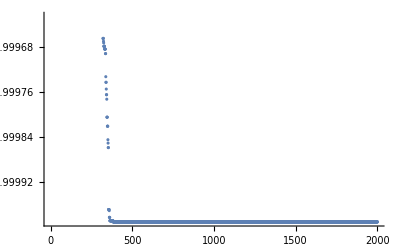

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[Trid,5];AppendTo[Solution30,Solution]]
```

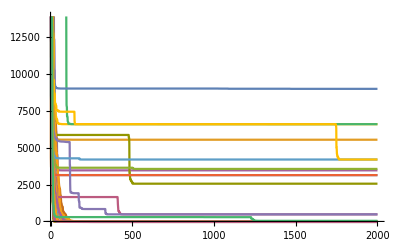

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{19601.5,8565.,8185.84,6161.3,6146.32,6076.31,5573.85,5514.33,5412.76,5266.49,5266.49,5217.6,5162.96,5071.26,4839.03,4701.92,4700.11,4651.43,4647.51,4603.92,4488.33,4442.39,4442.36,4435.14,4413.3,4413.3,4400.28,4399.17,4308.99,4308.98,4308.98,4306.69,4302.5,4302.04,4302.04,4299.03,4298.22,4298.21,4297.02,4296.47,4296.09,4296.08,4296.08,4295.65,4288.89,4288.31,4288.29,4287.94,4287.91,4287.57,4287.55,4287.52,4287.5,4287.49,4287.48,4283.78,4283.77,4283.77,4283.74,4283.74,4283.74,4283.72,4283.72,4283.7,4283.26,4283.24,4283.24,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.23,4283.05,4283.05,4283.05,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4283.,4211.,4211.,4210.53,4209.84,4206.49,4203.44,4203.44,4203.44,4203.44,4203.44,4203.44,4202.64,4202.64,4202.64,4202.64,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.,4202.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{142823.,52716.6,48710.8,32148.6,31498.1,31380.9,30144.2,15063.,13218.1,13213.6,8445.58,4442.63,4081.15,3253.54,3008.98,2044.39,1059.4,1055.8,1009.88,665.276,614.406,536.666,490.926,490.926,430.127,404.72,377.331,375.777,346.925,346.925,333.676,333.046,327.492,326.958,326.958,326.853,326.15,321.948,301.578,301.264,300.97,299.803,299.409,299.171,299.093,298.259,298.259,298.134,297.242,297.165,297.14,296.795,296.646,296.27,296.27,295.861,295.861,295.861,295.847,295.847,295.847,295.693,295.689,295.689,295.688,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.685,295.681,295.681,295.681,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.68,295.672,295.672,295.672,295.388,295.359,295.328,295.328,292.93,292.93,292.93,292.23,292.23,291.946,291.69,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.68,291.04,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,290.68,286.68,188.68,188.68,188.68,188.68,177.14,177.14,172.3,172.3,164.235,164.235,164.235,164.221,145.075,112.637,85.7653,85.7356,85.7356,84.2658,70.5058,70.5058,65.4607,61.3922,61.1914,61.1761,56.8362,56.8362,56.5954,55.9826,48.8626,47.8618,46.8026,46.8026,46.4064,45.6605,45.6605,45.6489,45.3881,45.3653,45.3537,44.0309,44.0045,44.0045,43.8029,43.7773,42.4712,42.4584,42.4584,42.4584,42.445,42.445,42.4188,42.3847,42.3718,42.3523,42.3225,42.3225,42.2865,42.2865,42.2744,42.2744,42.2744,42.1645,42.1645,42.1645,42.159,42.159,42.1586,42.1575,42.1572,42.1448,42.0864,42.0378,42.0378,42.0378,42.0378,42.014,42.0021,42.0021,42.002,42.002,42.002,42.002,42.002,42.002,42.002,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.0001,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.,42.}

```mathematica
average=Mean@Solution30
```

{67876.5,41371.8,34873.9,30011.2,25968.6,23102.8,19436.5,15818.4,13856.8,12785.4,11075.4,9529.54,8636.79,7842.84,7447.24,6969.,6338.18,6085.78,5628.39,5266.67,4895.83,4703.24,4618.87,4419.18,4213.26,4100.47,3945.31,3894.17,3764.73,3707.83,3664.14,3571.63,3542.01,3502.8,3424.5,3356.09,3342.93,3299.87,3269.62,3227.94,3209.08,3158.29,3086.52,3071.42,3021.56,2991.9,2973.04,2948.1,2912.05,2892.3,2870.4,2846.9,2836.56,2809.03,2775.88,2761.53,2741.5,2734.01,2721.71,2702.96,2697.26,2691.05,2664.13,2658.26,2644.27,2634.36,2629.54,2621.28,2609.97,2605.46,2600.33,2597.69,2594.95,2589.07,2585.09,2575.8,2570.46,2566.39,2563.01,2556.72,2555.02,2550.85,2546.72,2544.36,2542.18,2541.39,2539.92,2537.46,2533.73,2531.43,2530.02,2528.57,2527.42,2522.71,2515.66,2514.51,2327.26,2268.74,2262.,2259.64,2237.91,2235.6,2232.34,2231.14,2220.12,2218.92,2217.83,2216.04,2211.94,2210.95,2209.94,2207.75,2207.3,2206.85,2203.69,2202.4,2201.45,2148.44,2147.9,2105.63,2088.68,2087.,2083.79,2083.49,2083.05,2082.23,2081.85,2081.43,2081.18,2080.69,2080.42,2079.43,2079.2,2078.87,2078.58,2078.19,2078.1,2077.91,2077.85,2077.3,2077.12,2076.93,2076.88,2076.7,2076.51,2076.12,2054.94,2051.97,2048.1,2047.9,2047.85,2047.29,2047.15,2046.98,2046.93,2046.83,2046.77,2046.73,2046.68,2046.66,2046.6,2046.49,2046.41,2046.23,2046.18,2046.01,2045.83,2045.72,2045.56,2045.5,2045.38,2045.36,2027.9,2027.29,2026.68,2026.61,2013.31,2009.61,2009.57,2009.52,2009.43,2009.21,2009.09,2009.07,2009.04,2008.99,2008.95,2008.3,2008.23,2008.18,2008.12,2006.27,2006.23,2006.21,2006.,2005.92,2005.91,2005.9,2005.88,2005.88,2005.82,2005.77,2005.7,2005.7,2005.68,2005.67,2005.58,2005.58,2005.57,2005.56,2005.53,2005.52,2005.48,2005.47,2005.46,2005.46,2005.45,2005.45,2005.44,2005.43,2005.43,2005.43,2005.42,2005.41,2005.4,2005.4,2005.39,2005.38,2005.37,2005.37,2005.37,2005.36,2005.36,2005.34,2005.34,2005.33,2005.33,2005.33,2005.32,2005.31,2005.31,2005.3,2005.29,2005.28,2005.28,2005.27,2005.27,2005.27,2005.27,2005.26,2005.26,2005.25,2005.25,2005.24,2005.24,2005.24,2005.24,2005.24,2005.24,2005.23,2005.23,2005.22,2005.22,2005.22,2005.22,2005.22,2005.21,2005.21,2005.21,2005.21,2005.2,2005.2,2005.2,2005.2,2005.2,2005.2,2005.2,2005.2,2005.2,2005.2,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.19,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,2005.18,1995.18,1995.18,1995.,1994.98,1994.41,1994.41,1994.41,1993.48,1993.48,1993.48,1993.21,1993.21,1993.21,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.18,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.17,1993.16,1993.16,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1993.14,1986.93,1977.35,1972.2,1967.29,1961.27,1961.27,1961.27,1961.25,1961.06,1959.18,1959.18,1959.17,1956.29,1956.29,1956.29,1956.29,1956.21,1954.86,1954.8,1954.79,1954.28,1954.28,1954.23,1954.23,1954.23,1954.22,1954.21,1954.18,1954.17,1954.14,1954.13,1954.1,1954.08,1954.08,1954.06,1954.05,1954.04,1954.04,1954.04,1954.04,1954.04,1954.04,1954.04,1954.03,1954.03,1954.03,1954.03,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1954.02,1947.35,1947.35,1947.35,1934.82,1868.95,1868.95,1865.22,1864.15,1854.04,1854.04,1854.04,1854.04,1850.57,1850.57,1850.57,1850.57,1848.58,1848.58,1848.53,1848.53,1846.58,1846.58,1846.58,1843.92,1842.82,1842.82,1842.8,1842.7,1841.45,1841.18,1841.18,1841.18,1841.16,1841.16,1841.13,1841.13,1841.13,1841.13,1841.13,1841.13,1841.13,1841.13,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.12,1841.05,1841.05,1841.05,1841.05,1841.05,1841.04,1841.04,1841.04,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1841.02,1840.97,1840.97,1840.97,1840.97,1840.96,1840.96,1840.96,1840.96,1840.95,1840.95,1840.95,1840.95,1840.95,1840.95,1840.95,1840.95,1840.94,1840.94,1840.94,1840.94,1840.94,1840.94,1840.94,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.93,1840.92,1840.92,1840.92,1840.92,1840.84,1840.84,1840.84,1840.81,1840.81,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.8,1840.77,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.76,1840.66,1840.66,1840.66,1840.66,1840.66,1840.66,1840.66,1840.66,1840.66,1840.63,1840.63,1840.63,1840.63,1840.63,1840.63,1840.63,1840.63,1840.63,1840.63,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.6,1840.33,1840.33,1840.33,1840.33,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.3,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.26,1840.13,1836.86,1836.86,1836.86,1836.86,1836.48,1836.48,1836.32,1836.32,1836.05,1836.05,1836.05,1836.05,1835.41,1834.33,1833.43,1833.43,1833.43,1833.38,1832.92,1832.92,1832.75,1832.62,1832.61,1832.61,1832.47,1832.47,1832.46,1832.44,1832.2,1832.17,1832.13,1832.13,1832.12,1832.09,1832.09,1832.09,1832.09,1832.09,1832.08,1832.04,1832.04,1832.04,1832.03,1832.03,1831.99,1831.99,1831.99,1831.99,1831.99,1831.99,1831.99,1831.99,1831.99,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.98,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.97,1831.93,1831.93,1831.93,1831.93,1831.92,1831.92,1831.92,1831.9,1831.9,1831.9,1831.9,1831.9,1831.9,1831.88,1831.88,1831.88,1831.88,1831.88,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.87,1831.81,1831.77,1831.77,1831.73,1831.71,1831.71,1831.65,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.64,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1831.63,1828.47,1828.47,1822.27,1779.13,1779.13,1774.26,1764.24,1764.24,1760.31,1758.64,1758.63,1758.63,1756.08,1756.06,1756.06,1756.06,1755.,1752.96,1752.96,1751.75,1751.75,1751.75,1751.75,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.74,1751.73,1751.72,1751.72,1751.72,1751.72,1751.72,1751.71,1751.71,1751.71,1751.71,1751.71,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7,1751.7}

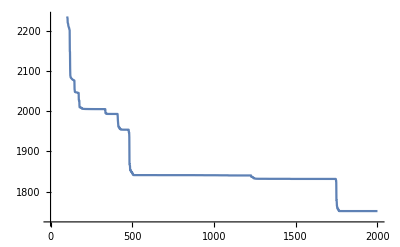

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{57620.2,41814.3,32856.2,25191.6,22434.1,17131.2,14661.6,13380.3,11007.3,10766.5,8536.12,7858.12,7423.68,6645.6,6122.88,5826.62,5171.02,4790.39,4561.52,4269.4,4258.01,4025.2,4024.07,3627.22,3316.32,3240.12,3229.89,3197.8,3133.15,3124.01,3089.59,3081.25,3064.55,3043.59,3011.65,2827.1,2789.39,2789.39,2774.56,2774.55,2596.7,2596.52,2502.69,2393.55,2316.2,2307.56,2218.16,2116.46,2061.99,2044.11,1925.9,1831.73,1827.07,1617.95,1494.85,1493.46,1311.8,1238.17,1235.28,1137.17,1127.08,1087.71,923.306,911.922,851.441,787.77,785.129,705.432,627.319,627.319,603.981,595.397,566.322,541.954,518.305,513.827,506.308,474.977,472.074,429.512,421.355,394.342,374.266,368.395,359.195,357.234,351.064,342.867,318.199,318.199,318.153,312.983,311.335,306.604,257.661,257.661,254.302,247.376,235.613,230.221,228.955,206.539,205.392,205.093,188.201,183.911,183.144,179.318,175.391,169.104,160.515,131.09,130.376,126.449,84.105,76.1052,70.5372,66.5979,59.5606,53.9773,52.5745,47.198,46.17,45.6131,45.0907,39.5511,38.9529,36.9686,36.8297,35.9844,35.3308,34.1351,32.3752,29.6667,29.5839,28.181,27.3201,25.1717,25.0811,23.6597,22.4163,20.4028,20.0011,19.6992,18.0129,13.2274,12.4027,11.966,11.4951,9.37431,9.19994,6.16428,5.94569,3.84727,3.61917,2.53077,1.80917,1.48277,1.1547,1.04875,0.678692,-0.912599,-1.73267,-3.39906,-3.4345,-5.04293,-7.60664,-8.38058,-10.5855,-10.5855,-11.6641,-11.8653,-14.0344,-17.5685,-18.3806,-18.958,-19.318,-19.4721,-19.7183,-20.1155,-20.1401,-20.2184,-20.3177,-20.4509,-20.6079,-20.867,-21.2069,-21.3693,-21.7801,-22.3885,-22.8316,-23.1116,-23.2855,-23.4444,-23.4471,-24.6468,-24.6565,-24.7101,-24.7749,-24.7837,-25.6297,-25.6297,-25.8671,-25.8689,-26.0638,-26.1721,-26.6305,-26.6394,-26.6936,-26.8509,-27.04,-27.0982,-27.564,-27.6644,-27.7083,-27.7417,-27.7924,-27.8614,-27.8947,-27.9204,-27.9341,-27.9647,-27.9919,-28.1781,-28.1895,-28.2149,-28.2565,-28.2958,-28.3726,-28.4136,-28.4259,-28.4571,-28.4856,-28.6682,-28.6957,-28.7329,-28.7329,-28.7335,-28.7563,-28.7651,-28.773,-28.8946,-28.9714,-29.0097,-29.018,-29.018,-29.0208,-29.0275,-29.0275,-29.0421,-29.0585,-29.1819,-29.2165,-29.2382,-29.2395,-29.2504,-29.256,-29.256,-29.266,-29.2717,-29.2717,-29.4009,-29.4009,-29.4249,-29.4249,-29.4249,-29.485,-29.485,-29.5104,-29.511,-29.593,-29.6107,-29.6107,-29.613,-29.6146,-29.6153,-29.6169,-29.6169,-29.6169,-29.6176,-29.6407,-29.6414,-29.6414,-29.6418,-29.6418,-29.6436,-29.6436,-29.644,-29.6815,-29.6832,-29.694,-29.7015,-29.7016,-29.7016,-29.7016,-29.7018,-29.7061,-29.7062,-29.7062,-29.7062,-29.7109,-29.7128,-29.7135,-29.7135,-29.7138,-29.7152,-29.7152,-29.7152,-29.7167,-29.7172,-29.7175,-29.7176,-29.7182,-29.7188,-29.7196,-29.7196,-29.7196,-29.7235,-29.7235,-29.7258,-29.7259,-29.7263,-29.7265,-29.7265,-29.727,-29.7275,-29.7282,-29.7282,-29.7283,-29.7292,-29.7292,-29.731,-29.731,-29.7317,-29.7317,-29.7317,-29.7317,-29.7319,-29.7326,-29.7334,-29.7334,-29.7337,-29.7337,-29.7341,-29.7342,-29.7349,-29.735,-29.7353,-29.7355,-29.7357,-29.7358,-29.7358,-29.736,-29.736,-29.736,-29.7363,-29.7363,-29.7364,-29.7365,-29.7365,-29.7365,-29.7365,-29.7365,-29.7366,-29.7366,-29.7371,-29.7371,-29.7371,-29.7373,-29.7373,-29.7375,-29.7375,-29.7375,-29.7375,-29.7375,-29.7376,-29.7376,-29.7376,-29.7376,-29.7377,-29.7377,-29.7378,-29.7378,-29.7379,-29.7379,-29.7381,-29.7383,-29.7383,-29.7383,-29.7386,-29.7386,-29.7387,-29.7387,-29.7388,-29.7388,-29.7389,-29.7389,-29.7389,-29.7389,-29.7389,-29.7389,-29.739,-29.739,-29.739,-29.739,-29.739,-29.739,-29.7391,-29.7391,-29.7391,-29.7392,-29.7392,-29.7392,-29.7392,-29.7392,-29.7392,-29.7393,-29.7393,-29.7393,-29.7393,-29.7394,-29.7394,-29.7394,-29.7394,-29.7394,-29.7395,-29.7395,-29.7395,-29.7395,-29.7395,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7396,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7397,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7398,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.7399,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.74,-29.7409,-29.7409,-29.7409,-29.7409,-29.7449,-29.7449,-29.7449,-29.7449,-29.7449,-29.7449,-29.745,-29.745,-29.745,-29.745,-29.745,-29.745,-29.7746,-29.7746,-29.7794,-29.7794,-29.7794,-29.7961,-29.7961,-29.8146,-29.8146,-29.8146,-29.8154,-29.8154,-29.8183,-29.8183,-29.8184,-29.8184,-29.8184,-29.8184,-29.8188,-29.8188,-29.8188,-29.8188,-29.8188,-29.8195,-29.8195,-29.8195,-29.8195,-29.8199,-29.8199,-29.8199,-29.8199,-29.8199,-29.8199,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82,-29.82}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{30677.7,21398.4,22384.,21188.8,16018.5,15852.,14058.3,10736.4,9237.16,8160.07,8151.81,6448.82,6113.17,5697.6,5361.23,5379.63,4876.07,4887.49,4420.1,4276.51,3869.4,3856.62,3839.06,3798.07,3726.74,3686.92,3552.53,3542.63,3491.88,3489.74,3493.42,3468.51,3472.07,3468.47,3435.77,3429.78,3427.04,3437.22,3438.32,3423.88,3426.47,3421.91,3414.61,3420.65,3428.46,3437.49,3441.94,3451.52,3458.57,3460.42,3469.8,3477.47,3480.94,3489.23,3501.06,3509.37,3519.26,3522.53,3527.75,3536.71,3539.23,3542.57,3555.45,3559.04,3565.23,3570.88,3573.87,3578.04,3584.09,3586.66,3589.68,3591.23,3592.87,3596.48,3598.91,3603.59,3607.09,3609.59,3611.81,3615.39,3616.3,3618.95,3621.65,3623.23,3624.49,3625.,3625.89,3627.35,3629.78,3631.23,3632.15,3632.97,3633.74,3622.98,3626.85,3627.59,3053.24,2930.32,2926.52,2925.01,2887.03,2888.73,2888.29,2887.92,2872.67,2871.73,2870.8,2869.35,2864.98,2865.71,2866.42,2868.03,2868.36,2868.7,2871.03,2872.02,2872.36,2826.85,2827.27,2811.25,2810.19,2810.24,2810.57,2810.58,2810.54,2811.12,2811.37,2811.51,2811.68,2811.93,2812.1,2812.38,2812.52,2812.76,2812.97,2813.17,2813.23,2813.36,2813.41,2813.58,2813.71,2813.79,2813.83,2813.96,2814.1,2814.4,2775.01,2769.87,2763.52,2763.66,2763.66,2763.39,2763.48,2763.61,2763.65,2763.72,2763.77,2763.8,2763.84,2763.85,2763.9,2763.99,2764.04,2764.19,2764.23,2764.36,2764.49,2764.58,2764.7,2764.74,2764.84,2764.86,2767.44,2767.73,2767.91,2767.96,2772.2,2770.72,2770.75,2770.76,2770.78,2770.74,2770.67,2770.68,2770.7,2770.74,2770.76,2771.03,2771.05,2771.08,2771.12,2771.91,2771.9,2771.92,2772.01,2772.08,2772.08,2772.09,2772.1,2772.1,2772.15,2772.17,2772.21,2772.21,2772.23,2772.24,2772.28,2772.29,2772.29,2772.3,2772.32,2772.33,2772.36,2772.37,2772.37,2772.37,2772.38,2772.38,2772.39,2772.39,2772.4,2772.4,2772.41,2772.42,2772.42,2772.42,2772.43,2772.43,2772.44,2772.45,2772.45,2772.45,2772.45,2772.46,2772.47,2772.47,2772.47,2772.48,2772.48,2772.49,2772.49,2772.5,2772.5,2772.51,2772.51,2772.52,2772.52,2772.52,2772.52,2772.53,2772.53,2772.53,2772.54,2772.54,2772.54,2772.54,2772.54,2772.54,2772.55,2772.55,2772.55,2772.56,2772.56,2772.56,2772.56,2772.56,2772.56,2772.56,2772.56,2772.57,2772.57,2772.57,2772.57,2772.57,2772.57,2772.57,2772.57,2772.57,2772.57,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.58,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2772.59,2777.46,2777.46,2777.56,2777.57,2777.88,2777.88,2777.88,2778.4,2778.4,2778.4,2778.55,2778.55,2778.55,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.57,2778.58,2778.58,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2778.59,2779.58,2781.91,2783.58,2785.43,2788.06,2788.06,2788.06,2788.07,2788.16,2789.06,2789.06,2789.07,2790.52,2790.52,2790.52,2790.52,2790.57,2791.28,2791.31,2791.31,2791.59,2791.59,2791.62,2791.62,2791.62,2791.62,2791.63,2791.65,2791.65,2791.67,2791.67,2791.69,2791.7,2791.7,2791.71,2791.72,2791.72,2791.72,2791.72,2791.72,2791.72,2791.72,2791.72,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2791.73,2782.29,2782.29,2782.29,2765.75,2705.92,2705.92,2703.93,2703.39,2698.9,2698.9,2698.9,2698.9,2697.61,2697.61,2697.61,2697.61,2696.94,2696.94,2696.92,2696.92,2696.3,2696.3,2696.3,2695.53,2694.79,2694.79,2694.78,2694.71,2693.88,2693.7,2693.7,2693.7,2693.7,2693.7,2693.68,2693.68,2693.68,2693.68,2693.68,2693.68,2693.68,2693.68,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.67,2693.55,2693.55,2693.55,2693.55,2693.55,2693.53,2693.53,2693.53,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.49,2693.47,2693.47,2693.47,2693.47,2693.46,2693.46,2693.46,2693.46,2693.46,2693.46,2693.46,2693.46,2693.46,2693.46,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.45,2693.5,2693.5,2693.5,2693.51,2693.51,2693.52,2693.52,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.53,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.54,2693.27,2693.27,2693.27,2693.27,2693.27,2693.27,2693.27,2693.27,2693.27,2693.18,2693.18,2693.18,2693.18,2693.18,2693.18,2693.18,2693.18,2693.18,2693.18,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2693.09,2692.35,2692.35,2692.35,2692.35,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.26,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.2,2692.28,2694.29,2694.29,2694.29,2694.29,2694.53,2694.53,2694.63,2694.63,2694.81,2694.81,2694.81,2694.81,2695.22,2695.93,2696.52,2696.52,2696.52,2696.56,2696.86,2696.86,2696.98,2697.07,2697.08,2697.08,2697.17,2697.17,2697.18,2697.19,2697.36,2697.38,2697.4,2697.4,2697.41,2697.43,2697.43,2697.43,2697.43,2697.44,2697.44,2697.47,2697.47,2697.47,2697.47,2697.47,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.5,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.51,2697.44,2697.44,2697.44,2697.43,2697.41,2697.41,2697.41,2697.38,2697.38,2697.38,2697.38,2697.38,2697.38,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.33,2697.17,2697.05,2697.05,2696.94,2696.87,2696.87,2696.71,2696.7,2696.7,2696.7,2696.7,2696.7,2696.7,2696.7,2696.7,2696.7,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2696.69,2690.95,2690.95,2680.01,2614.74,2614.74,2608.62,2596.83,2596.83,2592.51,2590.72,2590.72,2590.72,2588.05,2588.03,2588.03,2588.03,2586.95,2584.89,2584.89,2583.7,2583.7,2583.7,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.69,2583.68,2583.68,2583.68,2583.67,2583.67,2583.66,2583.66,2583.66,2583.66,2583.66,2583.66,2583.66,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65,2583.65}

```mathematica
(*Trid 10D*)
```

```mathematica
GA[Trid,10]
```

1132.29

```mathematica
Solution
```

{248435.,60669.4,60669.4,47892.6,47310.,46081.5,33371.6,27728.,25966.7,21889.2,21512.6,17228.4,17133.7,15961.8,15373.,14134.7,11370.9,10334.2,10334.2,6856.02,6618.26,6528.03,6261.46,6258.44,6066.73,6066.73,6066.68,5908.38,5908.38,5906.47,5572.88,5571.62,5541.39,5293.09,3147.32,3147.32,3119.59,2932.26,2918.6,2716.46,2716.46,2683.75,2656.78,2656.78,2554.19,2426.88,2412.82,2412.59,2383.16,2383.04,2314.96,2314.96,2241.13,2241.13,2239.22,2223.12,2222.74,2194.13,2193.39,2189.77,2185.98,2103.07,2103.07,2100.66,1943.84,1943.84,1935.22,1935.22,1881.96,1881.96,1881.59,1853.99,1845.06,1844.65,1794.26,1776.61,1776.61,1744.16,1744.16,1707.94,1707.94,1707.94,1707.94,1695.21,1639.38,1639.38,1632.32,1632.3,1575.95,1572.03,1518.97,1518.93,1517.49,1516.28,1506.76,1504.32,1491.32,1491.32,1491.31,1491.31,1491.29,1446.03,1446.03,1446.03,1425.66,1395.62,1393.11,1390.73,1363.04,1356.87,1356.87,1337.87,1337.87,1331.38,1331.38,1310.61,1310.61,1310.61,1301.34,1301.34,1300.3,1300.3,1298.82,1289.46,1286.5,1286.5,1276.59,1276.16,1276.16,1272.87,1272.87,1272.6,1268.27,1268.27,1267.26,1265.95,1265.95,1265.67,1257.87,1257.87,1257.81,1250.72,1250.43,1236.14,1236.14,1236.14,1236.14,1236.14,1236.03,1235.93,1233.68,1233.68,1233.68,1233.38,1230.58,1230.58,1230.58,1225.75,1224.48,1224.36,1224.36,1223.18,1223.18,1222.49,1222.43,1222.28,1216.91,1216.44,1211.87,1211.65,1211.65,1210.6,1208.57,1208.57,1207.83,1207.66,1207.66,1193.69,1193.69,1193.67,1189.49,1185.83,1185.83,1185.67,1185.67,1185.66,1185.66,1182.97,1182.77,1182.28,1181.23,1180.95,1180.95,1179.48,1179.48,1177.34,1176.5,1176.5,1175.5,1175.5,1174.73,1174.59,1174.41,1173.59,1165.87,1165.87,1164.02,1164.02,1163.85,1163.45,1163.45,1163.45,1163.45,1163.45,1163.44,1162.47,1157.78,1157.77,1157.7,1157.59,1157.59,1156.01,1155.72,1154.88,1154.7,1153.35,1153.35,1153.07,1152.91,1152.78,1150.06,1149.86,1148.79,1148.77,1148.77,1148.13,1148.13,1148.13,1148.13,1148.02,1148.02,1148.02,1147.04,1147.04,1147.04,1146.86,1146.86,1146.04,1146.04,1146.04,1146.04,1145.56,1145.56,1145.56,1144.6,1144.6,1144.6,1144.49,1144.4,1144.34,1144.34,1144.34,1144.34,1144.34,1144.31,1144.2,1144.,1144.,1143.84,1143.83,1143.82,1143.81,1143.81,1143.21,1143.21,1143.21,1143.21,1143.21,1143.18,1143.18,1143.17,1143.17,1143.17,1142.89,1142.89,1142.73,1142.73,1141.65,1141.65,1141.65,1141.65,1141.52,1140.45,1140.43,1140.27,1140.27,1140.,1139.87,1139.82,1139.82,1139.82,1139.82,1139.79,1139.79,1139.32,1139.32,1139.32,1139.32,1139.26,1139.24,1139.22,1138.88,1138.88,1138.85,1138.85,1138.85,1138.85,1138.85,1138.84,1138.84,1138.77,1138.43,1138.43,1138.43,1138.41,1138.41,1138.41,1138.4,1138.35,1138.32,1138.32,1138.32,1138.29,1137.98,1137.98,1137.98,1137.98,1137.98,1137.98,1137.97,1137.26,1137.26,1137.15,1137.15,1137.15,1136.81,1136.8,1136.8,1136.77,1136.77,1136.74,1136.72,1136.72,1136.65,1136.35,1136.35,1136.35,1136.34,1136.24,1136.24,1135.81,1135.81,1135.81,1135.81,1135.77,1135.76,1135.76,1135.74,1135.48,1135.48,1135.47,1135.47,1135.22,1135.22,1135.17,1135.15,1135.15,1135.14,1134.89,1134.84,1134.84,1134.84,1134.84,1134.7,1134.65,1134.65,1134.57,1134.53,1134.53,1134.46,1134.46,1134.46,1134.46,1134.46,1134.44,1134.44,1134.44,1134.41,1134.41,1134.41,1134.41,1134.4,1134.39,1134.35,1134.35,1134.27,1134.27,1134.27,1134.27,1134.27,1134.24,1134.24,1134.24,1134.24,1134.24,1134.23,1134.23,1134.08,1134.08,1134.08,1133.87,1133.87,1133.87,1133.87,1133.82,1133.82,1133.82,1133.82,1133.82,1133.82,1133.78,1133.78,1133.78,1133.77,1133.48,1133.48,1133.48,1133.48,1133.48,1133.44,1133.44,1133.44,1133.43,1133.42,1133.41,1133.41,1133.41,1133.41,1133.41,1133.41,1133.3,1133.3,1133.3,1133.3,1133.3,1133.22,1133.22,1133.22,1133.2,1133.19,1133.19,1133.15,1133.15,1133.15,1133.15,1133.15,1133.15,1133.08,1133.08,1133.08,1133.08,1133.08,1133.07,1133.07,1133.05,1133.05,1133.05,1133.03,1133.03,1133.03,1133.03,1133.03,1133.03,1133.03,1133.03,1132.99,1132.99,1132.99,1132.99,1132.99,1132.99,1132.97,1132.97,1132.97,1132.97,1132.97,1132.97,1132.96,1132.96,1132.96,1132.95,1132.95,1132.93,1132.93,1132.93,1132.92,1132.92,1132.91,1132.91,1132.91,1132.91,1132.91,1132.84,1132.84,1132.84,1132.84,1132.84,1132.84,1132.84,1132.84,1132.84,1132.84,1132.83,1132.83,1132.83,1132.83,1132.83,1132.83,1132.83,1132.83,1132.77,1132.77,1132.77,1132.77,1132.77,1132.77,1132.71,1132.71,1132.71,1132.71,1132.71,1132.71,1132.71,1132.71,1132.71,1132.71,1132.7,1132.7,1132.7,1132.7,1132.69,1132.69,1132.69,1132.69,1132.68,1132.68,1132.68,1132.68,1132.68,1132.68,1132.67,1132.67,1132.67,1132.67,1132.67,1132.67,1132.67,1132.67,1132.67,1132.65,1132.65,1132.65,1132.65,1132.65,1132.65,1132.65,1132.65,1132.65,1132.65,1132.64,1132.64,1132.64,1132.64,1132.64,1132.63,1132.63,1132.63,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.59,1132.58,1132.58,1132.58,1132.58,1132.58,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.57,1132.56,1132.56,1132.56,1132.56,1132.54,1132.54,1132.54,1132.54,1132.54,1132.53,1132.53,1132.53,1132.53,1132.53,1132.53,1132.53,1132.53,1132.51,1132.51,1132.51,1132.51,1132.51,1132.5,1132.5,1132.5,1132.5,1132.5,1132.5,1132.5,1132.5,1132.5,1132.48,1132.48,1132.48,1132.48,1132.48,1132.48,1132.48,1132.48,1132.48,1132.48,1132.47,1132.47,1132.47,1132.47,1132.47,1132.47,1132.47,1132.47,1132.47,1132.47,1132.46,1132.46,1132.43,1132.43,1132.42,1132.41,1132.41,1132.41,1132.41,1132.4,1132.4,1132.4,1132.39,1132.39,1132.39,1132.38,1132.38,1132.38,1132.38,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.37,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.36,1132.35,1132.35,1132.35,1132.35,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.34,1132.33,1132.33,1132.33,1132.33,1132.33,1132.33,1132.33,1132.33,1132.33,1132.33,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.32,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.31,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.3,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29,1132.29}

```mathematica
(*1 Solution plot*)
```

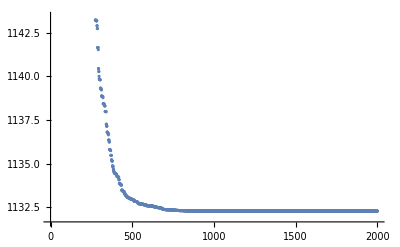

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[Trid,10];AppendTo[Solution30,Solution]]
```

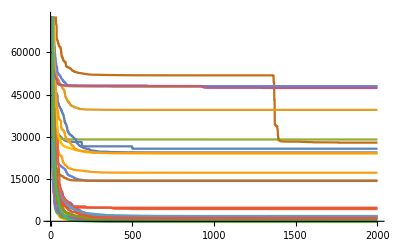

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{103275.,103202.,102966.,70574.6,70574.6,58801.6,40117.4,40097.1,30784.2,30315.7,29970.6,26437.5,25320.7,17691.3,17691.3,15286.4,15286.1,14887.5,14717.8,13965.6,13965.6,13743.2,13536.4,12281.6,12281.6,11721.8,10422.1,10422.1,9669.64,9380.37,8629.13,8324.21,8324.21,7928.76,7226.55,7226.55,6894.05,6857.83,6224.86,6224.86,6165.99,6165.99,6042.86,5402.3,5270.57,4717.07,4716.61,4716.02,4149.97,3823.34,2825.83,2825.09,2777.98,2777.98,2471.69,2241.24,2130.92,1983.26,1983.26,1893.54,1893.54,1678.04,1670.12,1634.16,1634.16,1627.77,1613.57,1613.57,1468.83,1451.03,1451.03,1380.89,1380.89,1380.89,1380.89,1380.43,1372.76,1371.4,1371.4,1308.44,1303.,1303.,1278.24,1277.72,1277.72,1139.47,1139.47,1130.44,1129.48,1126.05,1089.8,1089.8,1073.86,1073.7,1046.65,962.728,962.728,962.711,961.891,950.367,950.367,950.367,925.323,925.323,925.323,924.876,917.885,917.449,917.449,914.139,914.139,912.417,911.495,911.495,904.215,899.802,897.135,897.135,895.994,895.742,895.742,895.407,895.101,895.101,894.648,894.648,893.838,893.797,893.439,889.08,882.727,882.689,879.874,879.777,879.646,875.504,875.241,869.919,869.919,868.323,868.249,866.432,866.432,866.432,865.887,864.265,860.962,859.902,859.724,857.767,855.197,855.197,852.715,852.715,851.357,845.105,844.823,841.555,841.555,841.337,839.022,836.872,836.872,836.501,834.851,834.851,832.606,832.606,832.372,831.447,828.646,828.646,828.646,826.668,826.601,826.002,821.6,821.6,820.814,820.557,819.423,819.423,819.423,816.081,815.328,810.285,810.285,810.285,810.074,807.249,804.513,804.513,803.926,803.393,803.393,798.41,798.41,798.41,796.697,795.587,795.587,795.195,794.84,794.495,794.308,792.529,792.529,792.06,792.031,792.031,790.237,788.915,788.915,788.915,788.915,788.915,786.189,784.558,784.558,784.558,784.558,784.558,784.558,784.558,782.889,782.889,782.788,782.788,782.787,782.777,782.777,781.366,781.366,781.179,779.369,779.369,778.447,778.281,778.272,777.241,777.224,777.224,776.505,776.505,776.284,776.155,776.155,776.155,775.953,775.953,775.43,775.43,775.43,775.43,775.42,775.399,775.399,775.388,775.235,774.901,774.901,774.859,774.859,774.768,774.556,774.556,774.508,774.508,774.467,774.396,773.87,773.866,773.775,773.17,773.17,772.872,772.79,772.79,772.628,772.628,772.628,772.428,772.428,772.427,772.36,772.36,772.36,772.36,772.356,772.356,772.114,772.114,772.114,771.971,771.971,771.956,771.956,771.822,771.822,771.687,771.651,771.647,771.647,771.59,771.59,771.588,771.583,771.58,771.58,771.573,771.569,771.564,771.564,771.526,771.461,771.461,771.436,771.421,771.389,771.389,771.389,771.389,771.389,771.379,771.366,771.366,771.366,771.322,771.322,771.216,771.216,771.216,771.216,771.214,771.214,771.213,771.163,771.11,771.11,771.11,771.11,771.11,771.107,771.078,771.078,771.078,771.078,771.021,771.021,771.021,771.014,771.014,770.869,770.869,770.868,770.868,770.864,770.864,770.864,770.863,770.84,770.84,770.84,770.84,770.83,770.83,770.784,770.784,770.784,770.784,770.713,770.713,770.713,770.704,770.701,770.663,770.663,770.663,770.648,770.645,770.625,770.625,770.618,770.618,770.563,770.563,770.562,770.53,770.53,770.501,770.501,770.418,770.345,770.345,770.345,770.345,770.345,770.345,770.345,770.328,770.233,770.22,770.22,770.22,770.214,770.197,770.197,770.197,770.197,770.175,770.175,770.175,770.171,770.171,770.169,770.169,770.167,770.167,770.167,770.165,770.162,770.157,770.157,770.143,770.143,770.125,770.125,770.123,770.123,770.115,770.114,770.112,770.112,770.112,770.099,770.099,770.098,770.098,770.086,770.086,770.086,770.086,770.086,770.083,770.083,770.077,770.077,770.077,770.076,770.076,770.075,770.074,770.074,770.071,770.071,770.071,770.071,770.071,770.071,770.071,770.068,770.068,770.064,770.064,770.064,770.064,770.064,770.064,770.064,770.05,770.05,770.05,770.05,770.05,770.05,770.05,770.05,770.049,770.049,770.049,770.049,770.043,770.043,770.042,770.042,770.041,770.041,770.041,770.041,770.04,770.04,770.04,770.038,770.038,770.038,770.038,770.038,770.038,770.038,770.038,770.038,770.036,770.036,770.036,770.036,770.036,770.036,770.035,770.032,770.032,770.032,770.032,770.032,770.032,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.028,770.027,770.027,770.027,770.027,770.027,770.019,770.019,770.019,770.019,770.019,770.019,770.019,770.019,770.019,770.019,770.019,770.017,770.017,770.016,770.016,770.016,770.016,770.016,770.016,770.015,770.014,770.014,770.014,770.014,770.014,770.014,770.014,770.012,770.012,770.012,770.012,770.012,770.012,770.012,770.012,770.012,770.012,770.012,770.011,770.011,770.011,770.011,770.011,770.011,770.011,770.01,770.01,770.01,770.01,770.01,770.01,770.01,770.009,770.009,770.009,770.009,770.008,770.008,770.008,770.008,770.008,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.006,770.005,770.005,770.005,770.005,770.004,770.004,770.004,770.004,770.004,770.004,770.004,770.004,770.004,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.003,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.002,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.001,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.,770.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{371392.,250298.,227215.,224644.,128657.,115648.,115376.,51150.8,51145.9,47903.2,46242.6,20611.6,20609.2,20471.8,15458.,15458.,15458.,13088.1,13088.1,11365.4,11364.1,6767.88,6727.57,6457.09,6296.88,5002.98,5002.98,4988.32,4986.88,4898.,4593.02,4197.39,4093.93,3996.94,3812.38,3644.55,3521.3,3365.27,3280.49,3110.04,3058.,2756.31,2738.95,2738.95,2512.53,2487.09,2361.38,2307.8,2229.73,2189.32,1877.46,1877.46,1720.09,1554.78,1540.42,1525.15,1510.68,1495.18,1477.54,1393.47,1390.84,1260.45,1202.86,1202.86,1202.35,1146.71,1133.1,1121.57,1118.1,1074.86,1072.74,1037.32,1037.32,1021.54,1005.42,968.67,968.67,948.674,948.674,935.16,916.657,845.381,845.381,802.778,802.778,802.778,756.209,756.209,756.209,673.703,673.703,673.703,665.417,665.417,665.381,657.664,653.68,650.06,641.506,641.506,641.369,641.369,635.352,635.352,631.295,631.295,631.199,626.537,576.32,549.997,549.997,549.214,521.016,521.016,520.969,513.067,496.502,456.107,456.107,456.023,429.307,428.279,427.946,426.809,413.373,406.031,379.31,379.31,379.31,375.873,359.599,359.599,346.786,333.831,333.794,330.023,315.783,315.112,315.101,307.334,307.298,305.576,304.54,261.975,245.317,243.312,239.238,239.238,236.233,232.825,232.825,227.779,226.225,226.059,226.059,218.306,216.669,216.59,211.738,211.738,210.015,210.015,207.854,205.06,202.822,191.702,191.702,191.701,191.701,191.648,181.239,181.239,177.54,177.54,177.54,177.54,176.593,176.593,175.561,175.561,175.341,175.341,172.869,172.425,172.425,171.693,171.618,171.181,168.046,167.384,167.22,167.22,166.926,161.511,161.511,161.511,161.511,161.478,158.61,157.242,157.242,151.871,144.994,140.432,140.432,138.301,134.363,134.172,127.424,127.424,120.311,114.157,114.107,114.107,114.107,112.973,112.973,103.653,103.653,103.242,102.581,101.797,99.305,99.305,95.9777,95.9777,94.9746,87.2947,87.2947,87.2947,87.2947,86.0319,86.0319,84.9975,84.9975,82.9031,80.8227,80.8227,79.0221,76.8633,75.8301,74.7567,73.9943,70.5271,70.2922,70.2922,69.9005,67.1946,67.1946,65.9905,65.3834,64.4853,62.7964,61.965,57.0523,56.9949,56.8126,56.0559,52.8027,52.7959,52.2382,50.0517,49.9772,49.9627,48.5819,47.8267,46.4049,39.6854,39.6854,36.0754,36.0754,36.0754,35.8759,33.3491,31.8217,31.0361,31.0361,27.9782,27.9782,26.4743,25.7511,23.9867,21.972,21.8407,19.5929,19.5929,19.2196,19.2196,17.9177,17.8891,17.8768,15.9837,15.517,15.517,15.2631,12.709,12.709,12.337,11.4098,11.4098,11.4098,11.3384,11.2013,10.4015,10.4015,9.39489,9.00119,9.00119,9.00119,8.43595,8.43325,6.08155,6.08155,5.53275,5.53228,3.08451,3.01683,0.434903,0.434903,-4.4107,-4.41917,-4.88754,-5.94804,-5.94804,-7.55421,-8.60254,-8.60433,-8.80732,-9.74143,-23.4123,-23.4123,-24.4783,-25.4239,-28.799,-28.799,-29.8038,-31.6431,-31.6431,-31.6431,-31.6646,-31.6869,-37.5373,-37.5373,-37.5955,-37.5955,-39.1913,-39.1913,-39.5738,-41.0162,-41.0162,-41.0162,-41.8512,-42.1482,-42.1482,-43.0516,-43.0516,-43.0516,-43.0969,-43.0972,-44.2937,-46.7406,-47.0194,-47.0194,-47.8966,-48.6864,-50.1352,-50.6504,-50.6991,-50.7255,-52.4001,-52.4001,-52.4001,-53.0502,-53.0508,-53.1611,-53.1611,-54.32,-54.32,-54.32,-54.6626,-54.9232,-55.0404,-55.0639,-55.0639,-55.5363,-55.5363,-56.3571,-56.6272,-56.9421,-56.9421,-56.9421,-56.9781,-56.9781,-58.9375,-58.9554,-58.9554,-60.5555,-61.622,-61.622,-66.1597,-66.1597,-67.2697,-67.8491,-69.9135,-70.1402,-76.7432,-76.7432,-76.8666,-77.3014,-83.49,-83.999,-85.6039,-87.6019,-90.1199,-90.1199,-90.2065,-90.2096,-91.6788,-93.6152,-93.6996,-93.9656,-93.9886,-94.4866,-94.4966,-94.546,-94.7729,-94.8106,-94.8106,-95.0299,-95.1023,-95.2941,-95.7073,-95.7592,-95.7592,-99.6273,-101.669,-101.669,-101.669,-101.97,-102.875,-104.223,-105.146,-105.146,-105.514,-105.674,-105.674,-105.674,-105.897,-106.139,-106.139,-106.227,-106.725,-108.959,-109.072,-109.119,-109.607,-110.071,-110.071,-110.071,-110.102,-110.103,-111.248,-111.248,-111.809,-111.809,-113.766,-113.796,-113.811,-114.429,-115.496,-115.496,-115.5,-118.179,-118.179,-118.203,-118.203,-118.203,-118.387,-118.458,-120.022,-120.022,-120.628,-121.508,-121.979,-121.979,-122.096,-122.99,-123.005,-123.085,-123.865,-124.044,-124.172,-124.487,-124.499,-124.753,-125.901,-125.901,-125.982,-125.982,-126.512,-126.532,-128.095,-128.221,-128.247,-130.733,-130.964,-131.094,-131.145,-131.331,-131.331,-131.331,-131.958,-132.136,-132.25,-132.774,-133.577,-135.048,-136.638,-136.638,-136.868,-137.558,-138.551,-139.965,-141.162,-141.699,-141.699,-141.9,-141.9,-142.141,-142.525,-144.434,-144.434,-144.527,-145.189,-148.732,-148.732,-148.732,-149.379,-149.379,-149.38,-150.436,-153.016,-153.145,-153.741,-153.741,-154.318,-154.318,-154.378,-155.17,-155.738,-155.738,-155.742,-155.742,-155.995,-155.995,-156.089,-156.089,-156.089,-157.648,-157.669,-157.669,-157.669,-157.683,-157.937,-157.944,-158.182,-160.128,-162.196,-162.196,-162.251,-162.383,-165.874,-165.874,-167.321,-167.64,-167.64,-167.944,-167.944,-167.944,-172.067,-172.067,-172.264,-172.264,-172.266,-172.891,-172.913,-173.459,-173.459,-173.471,-174.117,-174.119,-174.149,-174.168,-174.168,-174.216,-174.217,-174.239,-174.479,-174.485,-174.529,-174.748,-174.994,-174.994,-175.147,-175.171,-175.182,-175.186,-175.571,-175.571,-176.166,-176.166,-176.719,-176.737,-176.737,-176.889,-176.889,-176.89,-177.008,-177.008,-177.012,-177.012,-177.575,-177.575,-177.578,-177.578,-177.667,-177.772,-177.772,-177.847,-177.847,-177.998,-177.998,-178.158,-178.186,-178.186,-178.883,-178.907,-178.907,-178.909,-179.022,-179.022,-179.616,-179.616,-179.616,-179.621,-179.708,-179.825,-179.896,-179.896,-179.929,-179.929,-180.282,-180.282,-180.282,-181.086,-182.211,-182.212,-182.381,-183.41,-183.41,-184.375,-184.454,-184.724,-184.724,-185.548,-185.548,-185.79,-185.79,-185.79,-186.003,-186.003,-186.042,-186.157,-186.157,-187.098,-187.098,-187.102,-187.111,-187.155,-187.55,-187.811,-187.811,-187.972,-187.972,-188.248,-188.248,-188.248,-188.248,-188.954,-189.067,-189.089,-189.093,-189.099,-189.203,-189.415,-189.672,-189.904,-189.908,-189.914,-189.914,-190.064,-190.389,-190.389,-190.408,-190.408,-190.556,-190.556,-190.556,-190.556,-190.556,-190.575,-190.604,-190.64,-190.64,-190.733,-190.764,-190.777,-190.786,-191.563,-191.563,-191.632,-192.026,-192.026,-192.026,-192.026,-192.026,-192.182,-192.214,-192.577,-192.577,-192.577,-193.228,-193.257,-193.257,-193.257,-193.257,-193.258,-193.261,-193.503,-193.503,-193.503,-193.702,-193.784,-193.794,-193.814,-193.98,-193.98,-193.98,-193.988,-194.344,-194.344,-194.344,-194.344,-194.925,-194.982,-194.982,-194.982,-195.044,-195.063,-195.067,-195.114,-195.173,-195.211,-195.645,-195.645,-195.645,-195.697,-195.697,-195.697,-195.957,-195.957,-195.957,-195.957,-196.675,-196.675,-196.853,-196.853,-196.854,-196.944,-197.355,-197.428,-197.758,-198.175,-198.175,-198.314,-198.483,-198.498,-198.503,-198.739,-198.739,-198.748,-198.872,-198.885,-198.885,-198.885,-198.903,-199.41,-199.41,-199.41,-199.51,-199.51,-199.51,-199.533,-199.533,-199.596,-199.621,-199.666,-199.67,-199.784,-199.871,-199.871,-199.871,-199.933,-199.933,-199.933,-200.119,-200.119,-200.119,-200.121,-200.123,-200.129,-200.129,-200.423,-200.423,-200.423,-200.423,-200.424,-200.44,-200.44,-200.493,-200.538,-200.548,-200.648,-200.648,-200.648,-200.719,-200.72,-200.728,-200.786,-200.786,-200.786,-200.786,-200.786,-200.802,-200.951,-200.952,-201.074,-201.124,-201.124,-201.127,-201.127,-201.127,-201.129,-201.129,-201.203,-201.203,-201.203,-201.203,-201.229,-201.274,-201.274,-201.274,-201.336,-201.336,-201.418,-201.418,-201.418,-201.432,-201.457,-201.502,-201.513,-201.635,-201.635,-201.635,-201.659,-201.747,-201.747,-201.749,-201.749,-201.751,-201.771,-201.773,-201.876,-201.879,-201.88,-201.881,-201.881,-201.937,-201.937,-201.958,-201.958,-201.958,-202.039,-202.075,-202.075,-202.075,-202.075,-202.09,-202.092,-202.092,-202.092,-202.138,-202.147,-202.147,-202.148,-202.148,-202.213,-202.268,-202.268,-202.432,-202.432,-202.441,-202.441,-202.526,-202.547,-202.547,-202.556,-202.556,-202.557,-202.592,-202.678,-202.678,-202.81,-202.81,-202.81,-203.002,-203.002,-203.014,-203.026,-203.054,-203.248,-203.248,-203.248,-203.347,-203.366,-203.367,-203.367,-203.372,-203.646,-203.769,-203.789,-203.81,-203.81,-203.865,-203.865,-203.866,-203.897,-203.907,-203.907,-204.071,-204.08,-204.08,-204.344,-204.344,-204.959,-204.959,-204.959,-204.959,-205.032,-205.032,-205.456,-205.456,-205.456,-205.456,-205.456,-205.456,-205.473,-205.473,-205.476,-205.476,-205.516,-205.582,-205.582,-205.582,-205.582,-205.599,-205.599,-205.675,-205.675,-205.675,-205.682,-205.694,-205.695,-205.695,-205.695,-205.697,-205.722,-205.796,-205.798,-205.835,-205.835,-205.835,-205.835,-205.835,-205.835,-205.838,-205.838,-205.838,-205.852,-205.852,-205.852,-205.855,-205.9,-205.909,-205.909,-205.909,-205.91,-205.91,-205.914,-205.914,-205.946,-205.946,-205.946,-205.946,-205.946,-205.946,-205.991,-205.991,-206.007,-206.007,-206.007,-206.007,-206.007,-206.007,-206.007,-206.016,-206.052,-206.052,-206.06,-206.06,-206.064,-206.064,-206.094,-206.103,-206.104,-206.121,-206.121,-206.121,-206.121,-206.212,-206.214,-206.229,-206.229,-206.229,-206.233,-206.234,-206.24,-206.48,-206.48,-206.48,-206.48,-206.526,-206.526,-206.526,-206.526,-206.526,-206.526,-206.527,-206.527,-206.56,-206.56,-206.595,-206.595,-206.595,-206.625,-206.625,-206.625,-206.625,-206.628,-206.646,-206.674,-206.674,-206.674,-206.674,-206.674,-206.687,-206.687,-206.687,-206.694,-206.694,-206.722,-206.779,-206.779,-206.779,-206.789,-206.79,-206.793,-206.814,-206.814,-206.834,-206.837,-206.837,-206.837,-206.882,-206.882,-207.011,-207.011,-207.011,-207.011,-207.011,-207.011,-207.048,-207.048,-207.048,-207.048,-207.052,-207.065,-207.065,-207.083,-207.086,-207.104,-207.153,-207.153,-207.153,-207.153,-207.153,-207.153,-207.17,-207.173,-207.186,-207.186,-207.203,-207.203,-207.234,-207.234,-207.234,-207.237,-207.259,-207.259,-207.305,-207.305,-207.369,-207.369,-207.369,-207.369,-207.371,-207.376,-207.376,-207.376,-207.404,-207.404,-207.404,-207.405,-207.421,-207.421,-207.422,-207.43,-207.433,-207.456,-207.46,-207.46,-207.46,-207.46,-207.463,-207.463,-207.477,-207.477,-207.483,-207.496,-207.496,-207.496,-207.496,-207.496,-207.496,-207.511,-207.511,-207.511,-207.54,-207.54,-207.54,-207.544,-207.545,-207.552,-207.556,-207.559,-207.565,-207.574,-207.574,-207.579,-207.579,-207.579,-207.579,-207.591,-207.599,-207.599,-207.6,-207.6,-207.6,-207.605,-207.635,-207.635,-207.641,-207.641,-207.643,-207.648,-207.648,-207.675,-207.675,-207.675,-207.686,-207.686,-207.687,-207.743,-207.743,-207.747,-207.747,-207.747,-207.751,-207.755,-207.764,-207.764,-207.784,-207.784,-207.784,-207.784,-207.785,-207.794,-207.794,-207.795,-207.797,-207.801,-207.829,-207.831,-207.831,-207.831,-207.831,-207.837,-207.837,-207.84,-207.844,-207.926,-207.985,-207.985,-208.025,-208.032,-208.135,-208.135,-208.135,-208.157,-208.157,-208.159,-208.166,-208.166,-208.166,-208.176,-208.176,-208.176,-208.27,-208.27,-208.27,-208.27,-208.27,-208.27,-208.27,-208.27,-208.27,-208.285,-208.285,-208.285,-208.307,-208.307,-208.322,-208.322,-208.322,-208.335,-208.341,-208.342,-208.342,-208.386,-208.386,-208.386,-208.386,-208.386,-208.387,-208.426,-208.426,-208.428,-208.428,-208.433,-208.433,-208.444,-208.444,-208.458,-208.458,-208.458,-208.458,-208.464,-208.464,-208.475,-208.48,-208.481,-208.481,-208.481,-208.501,-208.501,-208.502,-208.502,-208.506,-208.506,-208.512,-208.512,-208.512,-208.516,-208.516,-208.516,-208.532,-208.532,-208.532,-208.538,-208.556,-208.556,-208.556,-208.558,-208.558,-208.578,-208.578,-208.578,-208.578,-208.578,-208.595,-208.595,-208.595,-208.595,-208.595,-208.596,-208.596,-208.6,-208.6,-208.6,-208.6,-208.603,-208.603,-208.612,-208.612,-208.612,-208.612,-208.612,-208.612,-208.614,-208.614,-208.614,-208.614,-208.616,-208.617,-208.618,-208.619,-208.619,-208.619,-208.619,-208.619,-208.619,-208.63,-208.63,-208.63,-208.631,-208.633,-208.633,-208.639,-208.677,-208.677,-208.677,-208.678,-208.679,-208.682,-208.682,-208.695,-208.695,-208.695,-208.695,-208.734,-208.734,-208.734,-208.736,-208.746,-208.746,-208.754,-208.755,-208.762,-208.764,-208.774,-208.774,-208.774,-208.788,-208.788,-208.788,-208.788,-208.788,-208.809,-208.817,-208.817,-208.824,-208.826,-208.826,-208.826,-208.858,-208.858,-208.858,-208.858,-208.858,-208.863,-208.863,-208.863,-208.874,-208.874,-208.927,-208.941,-208.941,-208.941,-208.941,-208.941,-208.942,-208.952,-208.952,-208.953,-208.953,-208.953,-208.953,-208.958,-208.959,-208.975,-208.985,-208.988,-208.989,-208.989,-208.992,-208.994,-208.995,-208.995,-209.001,-209.001,-209.001,-209.002,-209.006,-209.006,-209.016,-209.016,-209.016,-209.02,-209.059,-209.059,-209.059,-209.063,-209.063,-209.063,-209.063,-209.064,-209.09,-209.09,-209.09,-209.118,-209.118,-209.128,-209.132,-209.16,-209.16,-209.16,-209.16,-209.16,-209.16,-209.16,-209.16,-209.163,-209.163,-209.164,-209.164,-209.168,-209.172,-209.179,-209.179,-209.195,-209.2,-209.2,-209.22,-209.22,-209.22,-209.22,-209.22,-209.22,-209.232,-209.245,-209.252,-209.266,-209.266,-209.278,-209.278,-209.281,-209.281,-209.295,-209.295,-209.342,-209.342,-209.347,-209.347,-209.347,-209.348,-209.351,-209.351,-209.352,-209.374,-209.374,-209.376,-209.388,-209.388,-209.399,-209.399,-209.4,-209.401,-209.401,-209.419,-209.419,-209.419,-209.42,-209.42,-209.422,-209.422,-209.423,-209.423,-209.431,-209.447,-209.447,-209.447,-209.448,-209.448,-209.448,-209.448,-209.448,-209.448,-209.453,-209.461,-209.461,-209.469,-209.471,-209.471,-209.471,-209.474,-209.474,-209.474,-209.477,-209.499,-209.499,-209.504,-209.504,-209.507,-209.507,-209.507,-209.523,-209.523,-209.523,-209.523,-209.523,-209.526,-209.533,-209.533,-209.536,-209.539,-209.539,-209.544,-209.56,-209.56,-209.56,-209.56,-209.56,-209.566,-209.566,-209.566,-209.566,-209.567,-209.567,-209.568,-209.574,-209.575,-209.575,-209.575,-209.575,-209.577,-209.577,-209.582,-209.582,-209.582,-209.582,-209.582,-209.59,-209.592,-209.592,-209.592,-209.595,-209.606,-209.606,-209.606,-209.606,-209.606,-209.608,-209.61,-209.61,-209.61,-209.61,-209.61,-209.618,-209.618,-209.618,-209.618,-209.618,-209.628,-209.629,-209.635,-209.635,-209.635,-209.638,-209.638,-209.638,-209.638,-209.639,-209.641,-209.641,-209.653,-209.653,-209.653,-209.663,-209.663,-209.663,-209.663,-209.663,-209.663,-209.664,-209.664,-209.671,-209.672,-209.672,-209.672,-209.672,-209.673,-209.674,-209.678,-209.678,-209.678,-209.678,-209.678,-209.678,-209.679,-209.679,-209.682,-209.682,-209.682,-209.682,-209.682,-209.684,-209.684,-209.684,-209.685,-209.685,-209.685,-209.685,-209.685,-209.685,-209.685,-209.685,-209.685,-209.687,-209.687,-209.687,-209.687,-209.687,-209.687,-209.688,-209.688,-209.688,-209.688,-209.688,-209.689,-209.689,-209.689,-209.689,-209.689,-209.689,-209.689,-209.697,-209.699,-209.699,-209.699,-209.699,-209.699,-209.7,-209.704,-209.704,-209.704,-209.709,-209.709,-209.709,-209.71,-209.71,-209.71,-209.71,-209.71,-209.71,-209.71,-209.711,-209.711,-209.711,-209.711,-209.714,-209.714,-209.714,-209.714,-209.714,-209.714,-209.714,-209.719,-209.72,-209.72,-209.72,-209.726,-209.726,-209.726,-209.726,-209.727,-209.727,-209.727,-209.728,-209.728,-209.728,-209.728,-209.728,-209.728,-209.728,-209.728,-209.729,-209.729,-209.729,-209.729,-209.735,-209.735,-209.735,-209.736,-209.736,-209.741,-209.741,-209.748,-209.748,-209.75,-209.753,-209.754,-209.754,-209.754,-209.76,-209.76,-209.76,-209.76,-209.76,-209.766,-209.766,-209.768,-209.768,-209.768,-209.768,-209.769,-209.778,-209.778,-209.778,-209.778,-209.782,-209.782,-209.782,-209.782,-209.782,-209.782,-209.784,-209.788,-209.788,-209.788,-209.788,-209.788,-209.79,-209.79,-209.791,-209.791,-209.791,-209.791,-209.793,-209.793,-209.793,-209.793,-209.796,-209.796,-209.796,-209.796,-209.796,-209.796,-209.796,-209.796,-209.798,-209.798,-209.798,-209.798,-209.798,-209.798,-209.798,-209.8,-209.8,-209.804,-209.804,-209.804,-209.806,-209.806,-209.808,-209.811,-209.811,-209.812,-209.812,-209.812,-209.812,-209.815,-209.815,-209.815,-209.815,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.823,-209.826,-209.826,-209.829,-209.829,-209.829,-209.829,-209.829,-209.829,-209.829,-209.829,-209.831,-209.832,-209.832,-209.832,-209.833,-209.833,-209.833,-209.833,-209.833,-209.833,-209.834,-209.834,-209.834,-209.834,-209.834,-209.834,-209.834,-209.834,-209.835,-209.835,-209.835,-209.835,-209.835,-209.835,-209.835,-209.841,-209.841,-209.841,-209.848,-209.848,-209.848,-209.848,-209.848,-209.848,-209.855,-209.855,-209.855,-209.855,-209.855,-209.855,-209.855,-209.855,-209.857,-209.857,-209.858,-209.858,-209.858,-209.859,-209.859,-209.859,-209.859,-209.86,-209.86,-209.86,-209.86,-209.86,-209.86,-209.86,-209.86,-209.86,-209.86,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.861,-209.863,-209.865,-209.865,-209.865,-209.865,-209.865,-209.865,-209.865,-209.865,-209.866,-209.866,-209.866,-209.866,-209.867,-209.867,-209.867,-209.868,-209.868,-209.868,-209.873,-209.873,-209.873,-209.873,-209.873,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.875,-209.876,-209.876,-209.876,-209.877,-209.877,-209.877,-209.877,-209.877,-209.877,-209.877,-209.877,-209.877,-209.877,-209.88,-209.88,-209.88,-209.88,-209.884,-209.884,-209.884,-209.884,-209.884,-209.884,-209.885,-209.885,-209.885,-209.885,-209.885,-209.885,-209.885,-209.885,-209.885,-209.886,-209.886,-209.886,-209.886,-209.886,-209.886,-209.89,-209.89,-209.89,-209.89,-209.89,-209.89,-209.891,-209.891,-209.891,-209.894,-209.894,-209.894,-209.894,-209.894,-209.894}

```mathematica
average=Mean@Solution30
```

{240532.,210824.,171675.,140443.,121397.,109612.,96762.4,84050.8,74121.8,70500.9,64380.5,59404.6,57146.8,53094.6,50860.6,48151.2,45484.2,44408.3,41422.3,39478.9,37604.7,35730.8,34048.5,32888.9,31952.6,30791.4,29751.7,29128.9,28652.5,27675.4,27029.6,26513.6,25932.8,25432.8,25159.7,24684.,24291.2,23711.9,23400.3,23105.9,22807.5,22468.3,22108.3,21864.6,21415.7,21253.1,21034.9,20928.,20671.6,20540.2,20298.8,20144.1,20033.8,19955.8,19780.,19687.,19632.9,19532.4,19380.4,19308.6,19186.3,19096.5,19014.5,18967.9,18788.4,18695.9,18634.,18506.7,18461.,18412.8,18342.3,18269.5,18176.2,18122.,18068.6,17970.,17922.9,17860.8,17771.8,17722.5,17677.8,17609.4,17535.4,17510.2,17413.4,17363.8,17284.7,17248.3,17210.7,17102.1,17054.8,17025.9,16971.4,16920.1,16863.,16820.,16787.2,16707.8,16684.8,16635.5,16617.3,16570.1,16498.1,16477.9,16432.1,16420.,16398.6,16382.7,16352.7,16324.1,16292.3,16265.7,16244.2,16221.,16200.3,16186.2,16157.3,16132.4,16112.7,16086.4,16070.,16052.7,16020.2,15998.7,15980.8,15950.,15942.1,15928.8,15899.5,15885.5,15860.4,15833.9,15806.9,15779.9,15772.1,15745.6,15721.6,15716.9,15683.7,15666.4,15653.9,15631.2,15610.6,15582.7,15558.9,15545.,15532.4,15526.6,15521.2,15502.1,15497.3,15487.7,15475.8,15456.9,15448.1,15424.7,15410.1,15363.7,15354.8,15344.5,15326.5,15317.3,15304.4,15292.9,15278.7,15264.2,15250.4,15240.5,15222.,15212.3,15199.4,15184.3,15174.4,15163.4,15155.9,15147.9,15143.2,15134.2,15125.1,15116.2,15101.8,15091.3,15080.3,15069.6,15062.5,15054.1,15044.7,15035.9,15029.9,15024.6,14992.6,14986.7,14954.7,14950.2,14940.2,14931.,14920.4,14911.8,14904.,14901.4,14896.2,14884.8,14879.,14871.7,14863.,14858.2,14853.6,14843.8,14832.4,14826.9,14815.1,14809.6,14803.6,14789.3,14779.,14770.6,14761.5,14758.1,14754.,14744.4,14737.4,14732.5,14724.4,14720.3,14716.2,14708.1,14705.3,14701.9,14695.7,14687.2,14685.,14683.7,14674.6,14673.5,14671.2,14668.1,14661.1,14652.9,14647.2,14635.,14632.5,14629.,14621.8,14618.,14616.4,14613.1,14608.1,14605.,14603.9,14597.5,14592.,14588.5,14586.4,14582.1,14580.,14577.4,14574.9,14572.3,14568.6,14566.8,14564.3,14562.1,14559.6,14557.5,14555.1,14553.4,14551.7,14548.8,14547.4,14544.4,14543.2,14540.4,14538.5,14537.5,14533.5,14532.5,14531.,14530.2,14529.,14526.9,14526.1,14523.4,14519.4,14518.,14515.2,14513.7,14511.1,14508.9,14507.1,14505.3,14503.7,14501.3,14499.8,14498.6,14496.2,14494.6,14493.6,14492.,14491.3,14490.2,14488.4,14486.1,14485.2,14484.5,14483.6,14482.3,14480.5,14479.5,14478.2,14477.9,14476.7,14475.2,14473.9,14472.4,14470.5,14468.6,14468.1,14466.3,14465.6,14463.1,14462.3,14461.8,14460.3,14459.2,14458.2,14456.9,14456.5,14454.9,14453.9,14452.5,14449.7,14448.6,14447.6,14445.7,14445.1,14444.2,14442.8,14441.9,14439.,14438.8,14437.4,14436.5,14435.6,14434.8,14433.6,14431.8,14431.2,14430.4,14429.5,14428.9,14427.7,14427.,14425.3,14424.8,14424.,14423.7,14423.2,14422.7,14422.,14421.2,14420.3,14419.6,14418.7,14417.3,14416.8,14416.,14415.5,14414.8,14414.3,14411.8,14410.,14408.3,14407.3,14405.2,14403.2,14402.8,14401.7,14401.1,14399.4,14395.8,14395.6,14392.6,14391.8,14391.1,14390.4,14388.,14387.6,14387.1,14386.8,14385.8,14385.,14384.7,14384.4,14382.8,14382.5,14382.,14381.4,14381.1,14380.6,14380.,14379.6,14379.3,14378.6,14378.3,14377.8,14377.2,14376.9,14376.7,14376.4,14376.,14375.6,14375.3,14375.,14374.6,14374.2,14374.,14373.2,14372.4,14372.1,14371.8,14371.6,14371.3,14371.,14370.7,14370.3,14369.8,14369.7,14369.5,14369.4,14369.,14368.8,14368.3,14367.9,14367.4,14366.4,14366.,14365.7,14365.6,14365.,14364.1,14363.9,14363.5,14363.,14362.7,14362.4,14362.2,14361.6,14361.5,14361.2,14360.8,14360.6,14359.9,14359.3,14359.,14358.4,14358.3,14357.7,14357.6,14357.3,14357.3,14356.9,14356.6,14356.5,14356.3,14355.3,14354.8,14354.5,14354.4,14354.,14353.7,14353.3,14352.6,14352.,14351.7,14351.6,14351.4,14351.2,14350.8,14350.3,14350.,14349.9,14349.4,14349.3,14348.8,14348.4,14348.2,14347.6,14347.3,14347.,14346.6,14346.5,14345.5,14345.3,14345.1,14344.8,14344.5,14344.3,14344.1,14340.7,14317.7,14317.3,14316.9,14316.8,14316.5,14313.4,14313.2,14312.9,14312.7,14312.1,14311.8,14311.7,14311.3,14311.1,14310.8,14310.4,14310.2,14310.,14309.8,14309.6,14309.4,14309.1,14308.8,14308.6,14308.4,14308.2,14308.2,14308.1,14307.8,14307.6,14307.4,14307.1,14306.9,14306.8,14306.4,14306.2,14306.,14305.8,14305.6,14305.4,14305.3,14305.1,14304.8,14304.6,14304.5,14304.3,14304.2,14304.1,14304.,14303.9,14303.6,14303.5,14303.5,14303.3,14303.1,14302.9,14302.7,14302.5,14302.4,14302.2,14302.1,14301.9,14301.8,14301.7,14301.5,14301.4,14301.4,14301.,14300.7,14300.6,14300.4,14300.2,14300.,14299.9,14299.7,14299.6,14299.6,14299.3,14299.2,14299.1,14298.7,14298.6,14298.4,14298.3,14298.3,14298.1,14297.8,14296.3,14296.2,14296.1,14295.8,14295.8,14295.7,14293.,14293.,14292.7,14292.6,14292.4,14292.4,14292.3,14291.7,14291.6,14291.5,14291.4,14291.3,14291.2,14291.,14290.8,14290.7,14290.6,14290.5,14290.3,14290.2,14290.1,14289.9,14289.8,14289.7,14289.7,14289.6,14289.4,14289.3,14289.3,14289.1,14289.,14289.,14288.9,14288.7,14288.6,14288.4,14288.3,14288.2,14288.1,14288.1,14287.9,14287.8,14287.8,14287.7,14287.7,14287.6,14287.6,14287.5,14287.5,14287.4,14287.3,14287.2,14287.2,14287.,14287.,14286.9,14286.9,14286.8,14286.6,14286.6,14286.6,14286.5,14286.4,14286.3,14286.2,14286.1,14286.,14286.,14285.8,14285.7,14285.6,14285.5,14285.5,14285.4,14285.3,14285.2,14285.2,14285.,14285.,14284.7,14284.6,14284.5,14284.4,14284.4,14284.3,14284.2,14284.2,14284.1,14284.1,14284.,14283.9,14283.9,14283.9,14283.8,14283.7,14283.7,14283.6,14283.6,14283.2,14283.2,14283.1,14283.,14282.9,14282.9,14282.8,14282.8,14282.7,14282.7,14282.6,14282.5,14282.4,14282.3,14282.3,14282.3,14282.3,14282.2,14282.1,14282.1,14282.,14282.,14281.9,14281.9,14281.9,14281.8,14281.8,14281.7,14281.7,14281.6,14281.5,14281.5,14281.5,14281.4,14281.3,14281.3,14281.3,14281.3,14281.2,14281.1,14281.1,14281.,14281.,14280.9,14280.9,14280.9,14280.8,14280.8,14280.7,14280.7,14280.7,14280.6,14280.6,14280.5,14280.5,14280.4,14280.4,14280.4,14280.4,14280.3,14280.3,14280.3,14280.2,14280.1,14280.1,14280.,14280.,14280.,14279.9,14279.9,14279.8,14279.8,14279.7,14279.7,14279.7,14279.6,14279.6,14279.5,14279.5,14279.5,14279.4,14279.4,14279.4,14279.3,14279.3,14279.3,14279.3,14279.2,14279.2,14279.2,14279.1,14279.1,14279.1,14279.,14279.,14279.,14279.,14279.,14278.9,14278.9,14278.9,14278.7,14278.7,14278.7,14278.7,14278.6,14278.6,14278.5,14278.5,14278.4,14278.4,14278.4,14278.4,14278.4,14278.4,14278.3,14278.3,14278.2,14278.2,14278.2,14278.1,14278.1,14278.1,14278.1,14278.,14278.,14278.,14277.9,14277.9,14277.9,14277.9,14277.8,14277.7,14277.7,14277.7,14277.6,14277.4,14277.4,14277.3,14277.3,14277.1,14277.1,14277.1,14277.,14277.,14277.,14276.9,14276.9,14276.9,14276.8,14276.8,14276.8,14276.8,14276.8,14276.8,14276.8,14276.8,14276.7,14276.7,14276.7,14276.7,14276.6,14276.6,14276.6,14276.6,14276.6,14276.5,14276.5,14276.5,14276.5,14276.5,14276.4,14276.4,14276.4,14276.4,14276.4,14276.4,14276.3,14276.3,14276.3,14276.3,14276.3,14276.2,14276.2,14276.1,14276.1,14276.1,14276.1,14276.1,14276.1,14276.1,14276.1,14276.,14276.,14276.,14276.,14276.,14276.,14275.9,14275.9,14275.9,14275.9,14275.9,14275.9,14275.8,14275.8,14275.8,14275.8,14275.8,14275.8,14275.7,14275.7,14275.7,14275.7,14275.7,14275.7,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.6,14275.5,14275.5,14275.5,14275.5,14275.5,14275.5,14275.5,14275.5,14271.4,14271.3,14271.3,14265.2,14265.,14264.9,14264.9,14264.9,14264.7,14258.2,14258.2,14258.1,14258.1,14258.1,14257.7,14257.6,14257.6,14257.6,14257.6,14257.6,14255.3,14254.5,14254.5,14254.5,14254.5,14254.4,14254.4,14254.,14254.,14253.9,14253.9,14253.9,14253.7,14253.7,14253.6,14253.6,14253.6,14253.5,14253.4,14253.4,14253.4,14253.4,14253.4,14253.4,14253.4,14253.3,14253.3,14253.2,14253.2,14253.2,14253.1,14253.1,14253.,14253.,14253.,14252.9,14252.9,14252.9,14252.9,14252.9,14252.9,14252.9,14252.9,14252.9,14252.8,14252.8,14252.8,14252.8,14252.8,14252.7,14252.7,14252.7,14252.7,14252.7,14252.7,14252.7,14252.7,14252.6,14252.6,14252.6,14252.6,14252.6,14252.6,14252.6,14252.6,14252.6,14252.6,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.5,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.4,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.3,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.2,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.1,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14252.,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.9,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.8,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.7,14251.3,14251.3,14251.3,14251.3,14251.2,14251.2,14251.2,14251.2,14251.1,14251.1,14251.1,14251.1,14251.1,14251.1,14250.2,14250.2,14250.2,14250.2,14250.2,14250.,14250.,14249.8,14249.8,14249.8,14249.8,14249.7,14249.7,14249.6,14249.6,14249.6,14249.6,14249.6,14249.6,14249.6,14249.5,14249.5,14249.5,14249.5,14249.5,14249.5,14249.5,14249.5,14249.5,14249.1,14249.1,14249.1,14249.1,14249.,14249.,14249.,14249.,14249.,14249.,14249.,14249.,14249.,14249.,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.9,14248.8,14248.8,14248.6,14166.1,14166.1,14166.1,14165.6,13962.,13961.8,13914.8,13668.3,13668.3,13667.4,13665.7,13659.7,13659.7,13649.5,13649.5,13649.5,13649.5,13649.5,13649.,13649.,13648.7,13648.7,13648.7,13614.4,13611.9,13585.4,13533.1,13533.1,13509.8,13509.8,13480.5,13480.5,13479.3,13477.9,13477.1,13476.7,13475.5,13475.3,13473.9,13472.,13472.,13472.,13470.7,13470.7,13468.3,13467.6,13466.4,13466.3,13466.3,13465.9,13465.9,13465.9,13465.9,13465.9,13465.6,13465.5,13465.5,13465.5,13465.5,13465.5,13465.5,13465.5,13465.5,13465.4,13465.2,13465.2,13465.2,13465.2,13465.1,13465.1,13465.1,13465.1,13465.1,13465.1,13465.1,13465.,13465.,13465.,13465.,13465.,13464.4,13464.4,13464.4,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.2,13464.1,13464.1,13464.1,13464.1,13464.1,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13464.,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13463.9,13462.9,13462.9,13462.9,13462.5,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.3,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13461.2,13460.9,13459.4,13459.4,13459.4,13459.4,13458.9,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13458.6,13456.8,13456.8,13456.8,13456.8,13456.8,13456.8,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.1,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13456.,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.8,13455.6,13455.6,13455.6,13455.6,13455.5,13455.5,13455.5,13455.4,13455.4,13455.4,13455.4,13455.3,13455.3,13455.3,13455.3,13455.3,13455.3,13455.3,13455.3,13455.3,13455.3,13455.,13455.,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.9,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13454.8,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.2,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1,13452.1}

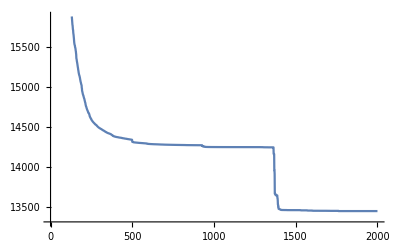

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{248094.,218488.,170779.,138086.,114133.,107574.,92148.5,85198.,77826.1,76489.2,64702.6,61949.6,59166.8,56744.4,56017.9,50591.2,46964.7,46168.9,43070.5,35679.8,33666.1,31805.6,28995.8,27863.8,27649.,25829.3,22478.2,21298.,20286.5,19801.3,18729.9,17816.6,17475.7,17475.7,16871.4,16652.6,16330.2,15553.9,15534.3,15223.6,14917.3,14839.4,13417.6,13404.2,12786.5,12786.5,12523.9,12238.8,12144.9,11966.1,11964.2,11759.4,11604.8,11604.8,11187.9,11050.1,10899.9,10892.6,10305.7,10280.3,9698.94,9698.94,9562.35,9551.71,8961.3,8866.56,8866.48,8565.34,8565.06,8531.32,8507.52,8443.52,8344.13,8185.89,8182.31,8002.33,7920.91,7819.61,7624.08,7588.27,7481.85,7481.85,7372.99,7303.48,7231.37,7062.86,6993.44,6993.44,6991.08,6903.54,6867.09,6862.69,6759.24,6672.91,6667.19,6640.45,6535.68,6462.36,6441.9,6437.11,6431.43,6424.92,6346.59,6265.99,6192.05,6192.05,6135.98,6095.42,6032.73,5965.66,5862.77,5839.3,5792.47,5712.99,5697.8,5650.5,5604.55,5552.92,5512.45,5451.64,5446.07,5376.54,5372.13,5370.07,5363.8,5304.48,5298.53,5286.93,5257.04,5231.06,5219.15,5196.35,5148.65,5145.71,5145.37,5139.15,5138.95,5138.05,5138.05,5021.68,5021.68,4903.48,4902.72,4866.44,4857.51,4857.51,4855.73,4828.03,4827.31,4788.8,4787.95,4787.95,4776.17,4772.45,4732.29,4732.08,4726.3,4684.16,4684.16,4683.94,4678.52,4678.52,4674.88,4642.42,4634.16,4617.16,4593.11,4538.42,4523.62,4523.62,4522.53,4454.77,4453.83,4441.64,4441.26,4391.85,4386.7,4384.62,4326.33,4326.21,4324.71,4322.63,4306.42,4304.56,4293.28,4239.22,4237.31,4201.78,4184.22,4161.08,4133.23,4132.13,4131.74,4125.23,4087.28,4081.37,4055.98,4055.98,4049.09,4048.93,4045.77,4041.61,4031.03,3996.34,3991.89,3987.99,3987.74,3961.97,3961.97,3941.95,3924.01,3923.29,3917.,3916.44,3915.01,3901.45,3892.62,3891.18,3885.65,3885.65,3884.24,3878.96,3877.71,3876.88,3873.87,3871.81,3871.74,3840.51,3839.04,3837.73,3837.73,3835.81,3835.65,3835.21,3835.01,3828.55,3827.3,3823.26,3823.26,3819.38,3819.38,3797.09,3796.92,3796.16,3789.21,3789.17,3789.17,3785.61,3784.78,3784.03,3783.37,3779.78,3779.23,3779.13,3779.09,3771.57,3758.89,3757.48,3757.48,3753.48,3752.76,3752.76,3752.45,3737.66,3735.08,3733.51,3730.24,3728.48,3722.78,3722.67,3722.63,3721.2,3707.75,3707.36,3706.36,3706.36,3699.49,3698.84,3689.32,3685.97,3685.94,3674.54,3674.53,3673.78,3671.13,3671.13,3670.32,3668.53,3668.37,3667.54,3667.53,3661.31,3648.83,3645.39,3644.92,3642.86,3642.86,3642.6,3641.58,3640.54,3640.46,3640.46,3637.55,3634.35,3632.32,3631.65,3631.31,3627.25,3623.81,3623.8,3623.78,3613.52,3613.49,3609.52,3607.63,3607.5,3607.42,3601.34,3601.29,3597.25,3597.25,3594.2,3594.2,3593.86,3593.86,3580.84,3580.83,3568.71,3568.4,3564.25,3553.62,3552.3,3552.29,3532.69,3530.69,3530.57,3526.74,3526.11,3525.67,3525.14,3516.25,3516.23,3516.21,3515.97,3513.43,3504.74,3504.74,3504.64,3501.99,3501.91,3501.,3500.98,3490.82,3490.77,3490.38,3490.38,3488.82,3488.76,3488.2,3488.2,3484.53,3484.53,3484.53,3484.52,3484.52,3479.02,3479.02,3478.53,3476.29,3471.84,3471.81,3458.74,3449.86,3439.94,3415.76,3415.76,3408.55,3408.55,3408.19,3359.65,3359.65,3318.44,3316.88,3316.03,3310.33,3286.34,3286.09,3286.05,3284.98,3283.96,3282.39,3282.34,3281.2,3269.1,3267.34,3265.32,3265.1,3265.09,3262.71,3259.57,3259.55,3259.52,3258.61,3256.78,3255.62,3255.21,3255.21,3255.2,3253.45,3253.45,3253.44,3253.38,3253.13,3253.07,3252.48,3251.84,3249.65,3242.67,3242.67,3242.61,3240.97,3240.97,3240.35,3240.26,3240.07,3237.44,3237.32,3237.28,3236.87,3236.85,3236.85,3236.34,3235.46,3232.65,3232.2,3231.23,3229.69,3229.67,3229.5,3229.46,3228.83,3228.22,3225.26,3225.26,3225.2,3225.08,3224.97,3224.29,3224.23,3224.21,3223.86,3223.81,3223.65,3223.33,3222.36,3222.08,3221.47,3221.47,3220.93,3220.88,3219.68,3219.68,3219.66,3219.58,3208.07,3208.07,3207.23,3207.09,3205.17,3205.17,3205.1,3196.68,3196.68,3196.68,3195.5,3195.5,3195.37,3191.28,3191.28,3191.28,3191.28,3191.22,3191.13,3187.92,3187.92,3187.91,3182.36,3178.78,3178.16,3178.16,3178.16,3165.33,3165.33,3165.23,3165.23,3163.86,3163.7,3163.43,3153.06,3153.06,3150.16,3150.16,3150.13,3150.12,3146.21,3146.09,3145.7,3144.74,3144.74,3142.57,3142.4,3139.69,3139.17,3136.5,3133.61,3133.61,3133.61,3133.5,3132.79,3132.11,3132.06,3130.72,3130.35,3130.29,3130.1,3130.1,3129.78,3129.75,3129.44,3129.06,3128.98,3128.86,3128.81,3128.41,3127.91,3127.84,3126.82,3126.82,3126.24,3126.23,3126.23,3126.05,3125.85,3125.48,3125.33,3124.71,3124.54,3124.5,3124.5,3123.93,3123.84,3123.73,3122.53,3122.53,3122.42,3121.83,3121.83,3121.69,3121.27,3120.78,3120.65,3120.65,3120.65,3120.53,3120.53,3120.43,3120.14,3120.14,3120.14,3119.48,3119.48,3119.45,3119.45,3119.45,3119.38,3119.37,3118.77,3118.44,3118.44,3118.44,3118.44,3118.35,3117.99,3117.95,3117.95,3117.4,3117.38,3117.17,3116.91,3116.69,3116.54,3116.52,3116.52,3116.49,3116.33,3116.29,3116.27,3116.27,3116.24,3116.24,3115.97,3115.87,3115.69,3115.3,3115.3,3115.29,3115.29,3115.06,3115.03,3114.93,3114.93,3114.92,3114.82,3113.59,3113.59,3113.59,3113.45,3113.45,3113.44,3113.3,3113.3,3113.3,3113.17,3112.94,3112.84,3112.81,3112.81,3111.92,3111.92,3111.74,3111.39,3111.39,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.72,3110.71,3110.71,3110.71,3110.71,3110.71,3110.68,3110.68,3110.68,3110.68,3110.68,3110.68,3110.68,3110.68,3110.68,3110.68,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.67,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.66,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3110.65,3107.67,3107.67,3107.67,3107.67,3107.67,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.29,3107.27,3107.27,3107.27,3107.27,3107.27,3107.27,3107.27,3107.27,3107.27,3107.27,3106.79,3106.79,3106.79,3106.79,3106.79,3106.79,3106.78,3106.78,3106.78,3106.78,3106.78,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.77,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.66,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.65,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3106.64,3100.76,3100.76,3100.57,3100.57,3099.4,3099.4,3099.08,3099.08,3099.08,3099.08,3099.06,3099.05,3099.05,3099.04,3098.79,3098.79,3098.79,3098.79,3098.79,3098.78,3098.78,3098.78,3098.78,3098.7,3098.7,3098.7,3098.7,3098.7,3098.7,3098.7,3098.7,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.69,3098.68,3098.68,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.67,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.65,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64,3098.64}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{55944.1,53885.2,47776.,39171.,32737.8,33813.,34065.9,30481.8,24757.6,22823.,22599.2,22832.,22820.,22755.7,22478.8,22918.3,22044.8,21831.1,21722.7,21156.,20917.5,20090.6,20124.3,20152.5,19933.7,19762.,19511.4,19602.9,19436.5,19224.5,19303.6,19229.2,19095.,18917.9,19046.3,18966.1,18779.5,18304.4,18251.,18253.9,18207.6,18141.6,18244.,18153.3,18162.6,18150.,18132.5,18162.5,18118.2,18130.8,18189.4,18169.7,18207.3,18216.7,18262.3,18270.,18299.6,18345.2,18326.9,18361.7,18370.1,18391.8,18333.6,18323.4,18263.4,18175.5,18175.2,18088.9,18101.8,18096.3,18063.3,18097.3,18095.2,18072.4,18059.7,18047.6,18068.6,18054.9,18019.,18038.,18055.8,18028.7,18024.8,18029.2,17964.1,17964.5,17914.8,17918.3,17935.5,17850.2,17841.9,17817.5,17785.9,17758.1,17717.9,17719.,17716.6,17661.4,17666.9,17654.4,17662.7,17641.2,17605.1,17606.1,17599.1,17595.7,17602.3,17604.,17600.1,17596.9,17600.,17592.3,17582.3,17585.9,17576.3,17581.5,17579.1,17561.7,17559.4,17551.7,17544.4,17545.4,17547.3,17538.5,17533.5,17527.9,17528.1,17523.7,17521.,17526.7,17522.8,17511.7,17512.3,17527.8,17526.5,17529.,17531.,17529.9,17533.6,17539.4,17536.7,17536.7,17534.9,17523.3,17522.9,17516.7,17517.8,17518.7,17511.2,17514.9,17513.8,17520.3,17518.5,17530.6,17530.7,17522.5,17524.,17504.6,17508.1,17505.2,17504.6,17508.6,17511.7,17514.6,17511.3,17517.9,17520.1,17520.,17522.,17518.4,17511.8,17516.6,17516.6,17509.9,17514.2,17515.6,17516.7,17519.9,17526.4,17526.3,17528.1,17533.6,17538.8,17542.4,17540.,17545.3,17544.8,17545.,17547.5,17547.5,17535.7,17535.4,17513.6,17516.6,17521.3,17521.8,17524.8,17524.7,17524.7,17523.9,17523.2,17527.2,17526.9,17530.5,17531.7,17532.3,17533.2,17537.3,17540.7,17541.9,17549.4,17549.8,17552.,17553.5,17557.5,17560.7,17562.6,17563.9,17565.3,17570.,17574.6,17575.2,17580.7,17582.1,17581.1,17580.9,17581.7,17583.4,17586.6,17589.4,17587.6,17587.9,17590.7,17590.1,17591.1,17593.1,17596.6,17599.3,17603.,17598.1,17599.3,17599.6,17597.8,17599.6,17599.9,17599.5,17600.3,17601.4,17601.4,17604.7,17607.9,17606.9,17607.8,17609.6,17610.2,17611.9,17612.8,17612.9,17614.2,17615.1,17616.,17615.7,17617.3,17618.8,17619.8,17620.2,17621.1,17621.6,17622.1,17622.1,17622.8,17624.3,17625.3,17625.9,17625.7,17626.2,17626.7,17627.,17627.4,17628.4,17628.7,17630.4,17632.3,17632.5,17633.1,17633.5,17633.6,17635.2,17636.,17636.4,17636.1,17635.9,17636.7,17637.4,17638.,17638.4,17638.5,17638.6,17638.7,17639.3,17639.8,17641.1,17641.1,17641.6,17641.8,17642.1,17643.3,17643.5,17644.,17644.1,17644.5,17645.4,17645.3,17645.9,17646.9,17648.2,17648.4,17649.1,17648.9,17650.5,17650.8,17650.8,17651.4,17652.1,17652.3,17653.,17653.1,17653.9,17654.5,17655.3,17657.2,17657.7,17658.,17659.3,17659.6,17660.,17661.,17660.7,17661.5,17661.5,17661.8,17662.2,17662.1,17662.6,17662.8,17663.2,17663.5,17663.8,17663.4,17663.8,17664.3,17664.7,17665.7,17666.,17666.3,17666.4,17666.6,17666.7,17666.5,17666.5,17667.1,17667.,17666.7,17667.7,17667.8,17667.9,17668.1,17668.3,17668.6,17669.9,17668.4,17668.8,17669.5,17669.1,17670.,17670.,17670.3,17669.7,17670.7,17672.6,17672.7,17674.3,17674.2,17674.7,17675.1,17676.3,17676.5,17676.4,17676.6,17677.2,17677.6,17677.7,17677.8,17678.5,17678.7,17678.9,17679.1,17679.3,17679.4,17679.7,17680.,17679.9,17679.8,17680.,17680.3,17680.6,17680.8,17680.6,17680.7,17681.1,17681.3,17681.3,17681.4,17681.7,17681.6,17681.7,17681.5,17682.1,17682.3,17682.2,17682.4,17682.5,17682.6,17682.9,17683.,17683.1,17683.1,17683.1,17683.2,17683.2,17683.3,17683.6,17683.9,17684.,17684.8,17684.8,17685.1,17685.1,17685.,17685.7,17685.8,17686.,17686.4,17686.6,17686.5,17686.6,17686.7,17686.8,17686.9,17687.,17687.1,17687.6,17687.9,17688.,17688.3,17688.4,17688.8,17688.9,17688.9,17688.9,17688.9,17689.,17689.,17689.1,17689.9,17690.1,17690.2,17690.1,17690.4,17690.5,17690.5,17691.1,17691.5,17691.7,17691.8,17691.8,17691.8,17692.1,17692.2,17692.2,17692.3,17692.6,17692.6,17692.8,17693.1,17693.1,17693.4,17693.6,17693.8,17693.8,17693.8,17694.4,17694.5,17694.6,17694.6,17694.8,17694.8,17695.,17693.5,17678.,17678.2,17678.5,17678.5,17678.6,17677.1,17677.1,17677.1,17677.1,17677.6,17677.7,17677.8,17678.,17678.1,17678.3,17678.6,17678.6,17678.7,17678.7,17678.9,17679.,17679.2,17679.3,17679.4,17679.5,17679.5,17679.6,17679.6,17679.8,17679.8,17679.8,17680.,17680.2,17680.2,17680.4,17680.5,17680.6,17680.6,17680.7,17680.9,17680.9,17681.,17681.2,17681.4,17681.4,17681.5,17681.6,17681.6,17681.6,17681.7,17681.8,17681.8,17681.9,17681.9,17682.,17682.1,17682.2,17682.2,17682.3,17682.4,17682.5,17682.5,17682.5,17682.6,17682.7,17682.8,17682.8,17683.1,17683.3,17683.3,17683.4,17683.5,17683.5,17683.6,17683.7,17683.8,17683.8,17683.9,17684.,17684.,17684.3,17684.4,17684.5,17684.5,17684.6,17684.7,17684.8,17682.3,17682.3,17682.4,17682.1,17682.1,17682.1,17677.5,17677.5,17677.5,17677.7,17677.7,17677.8,17677.8,17676.9,17676.9,17676.9,17677.,17677.1,17677.2,17677.2,17676.9,17676.8,17676.9,17676.9,17676.9,17676.9,17677.1,17677.1,17677.,17677.1,17677.1,17677.1,17677.3,17677.3,17677.3,17677.3,17677.4,17677.5,17677.5,17677.7,17677.7,17677.8,17677.8,17677.9,17677.9,17677.9,17678.,17678.1,17678.1,17678.1,17678.1,17678.2,17678.2,17678.2,17678.2,17678.3,17678.3,17678.3,17678.3,17678.5,17678.5,17678.5,17678.6,17678.6,17678.7,17678.7,17678.7,17678.8,17678.8,17678.9,17678.9,17679.,17679.1,17679.1,17679.2,17679.3,17679.4,17679.4,17679.4,17679.5,17679.5,17679.6,17679.6,17679.8,17679.8,17680.,17680.1,17680.1,17680.2,17680.2,17680.2,17680.3,17680.3,17680.3,17680.3,17680.4,17680.5,17680.5,17680.5,17680.5,17680.6,17680.6,17680.6,17680.6,17680.,17680.,17680.1,17680.1,17680.1,17680.2,17680.2,17680.3,17680.3,17680.3,17680.3,17680.4,17680.5,17680.5,17680.5,17680.6,17680.6,17680.6,17680.7,17680.7,17680.8,17680.8,17680.8,17680.8,17680.8,17680.9,17680.9,17680.9,17681.,17681.,17681.1,17681.1,17681.1,17681.2,17681.2,17681.2,17681.2,17681.2,17681.3,17681.3,17681.3,17681.4,17681.4,17681.4,17681.5,17681.5,17681.5,17681.5,17681.6,17681.6,17681.6,17681.6,17681.7,17681.7,17681.8,17681.8,17681.8,17681.8,17681.8,17681.9,17681.9,17681.9,17681.9,17682.,17682.,17682.1,17682.1,17682.1,17682.2,17682.1,17682.1,17682.2,17682.2,17682.2,17682.2,17682.3,17682.3,17682.4,17682.4,17682.4,17682.4,17682.4,17682.4,17682.5,17682.5,17682.5,17682.5,17682.5,17682.6,17682.6,17682.6,17682.6,17682.7,17682.7,17682.7,17682.7,17682.7,17682.7,17682.8,17682.8,17682.8,17682.9,17682.9,17682.9,17683.,17683.,17683.,17683.1,17683.1,17683.1,17683.1,17683.1,17683.1,17683.2,17683.2,17683.2,17683.2,17683.3,17683.3,17683.3,17683.3,17683.4,17683.4,17683.4,17683.4,17683.5,17683.5,17683.5,17683.5,17683.5,17683.5,17683.6,17683.6,17683.6,17683.6,17683.7,17683.2,17683.2,17683.,17683.,17682.8,17682.9,17682.9,17682.8,17682.8,17682.8,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17682.9,17683.,17683.,17683.,17683.,17683.,17683.,17683.,17683.,17683.,17683.1,17683.1,17683.1,17683.1,17683.1,17683.1,17683.1,17683.1,17683.2,17683.2,17683.2,17683.2,17683.2,17683.2,17683.2,17683.3,17683.3,17683.3,17683.3,17683.4,17683.4,17683.4,17683.4,17683.4,17683.4,17683.4,17683.4,17683.4,17683.4,17683.5,17683.5,17683.5,17683.5,17683.5,17683.5,17683.5,17683.5,17683.5,17683.6,17683.6,17683.6,17683.6,17683.6,17683.6,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.7,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.8,17683.9,17683.9,17675.8,17675.9,17675.9,17663.8,17664.,17664.,17664.,17664.,17663.5,17651.,17651.1,17651.,17651.,17651.,17650.2,17650.2,17650.2,17650.2,17650.2,17650.2,17646.2,17644.7,17644.7,17644.7,17644.7,17644.7,17644.6,17643.9,17643.9,17643.9,17643.7,17643.7,17643.5,17643.5,17643.4,17643.4,17643.4,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.1,17643.1,17643.,17643.,17643.,17643.,17643.,17642.7,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.7,17642.7,17642.7,17642.8,17642.8,17642.7,17642.7,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.6,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.7,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.8,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17642.9,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.1,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17643.2,17642.5,17642.5,17642.5,17642.5,17642.4,17642.4,17642.3,17642.3,17642.3,17642.3,17642.3,17642.3,17642.2,17642.2,17640.4,17640.4,17640.4,17640.4,17640.4,17640.1,17640.,17639.7,17639.7,17639.6,17639.6,17639.6,17639.6,17639.3,17639.3,17639.3,17639.3,17639.3,17639.3,17639.3,17639.2,17639.2,17639.2,17639.2,17639.2,17639.2,17639.2,17639.2,17639.2,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.4,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.5,17639.3,17639.3,17638.9,17462.,17462.,17462.,17461.,17068.1,17067.9,16986.3,16617.3,16617.3,16616.2,16614.1,16606.3,16606.3,16593.4,16593.5,16593.5,16593.5,16593.4,16592.9,16592.8,16592.4,16592.4,16592.4,16550.3,16547.4,16516.3,16458.6,16458.6,16434.5,16434.5,16405.6,16405.6,16404.3,16403.,16402.2,16401.9,16400.7,16400.6,16399.2,16397.4,16397.4,16397.4,16396.2,16396.2,16393.9,16393.2,16392.1,16392.1,16392.,16391.7,16391.7,16391.7,16391.7,16391.6,16391.4,16391.3,16391.3,16391.3,16391.3,16391.3,16391.3,16391.3,16391.2,16391.2,16391.,16391.,16391.,16391.,16391.,16391.,16391.,16390.9,16390.9,16390.9,16390.9,16390.9,16390.9,16390.9,16390.9,16390.9,16390.3,16390.3,16390.3,16390.1,16390.1,16390.1,16390.1,16390.1,16390.1,16390.1,16390.1,16390.1,16390.,16390.,16390.,16390.,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.9,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.8,16389.,16389.,16389.,16388.6,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.4,16387.1,16385.7,16385.7,16385.7,16385.7,16385.3,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16385.,16383.3,16383.3,16383.3,16383.3,16383.3,16383.3,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.7,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.5,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.4,16382.2,16382.2,16382.2,16382.2,16382.2,16382.2,16382.2,16382.1,16382.1,16382.1,16382.1,16382.,16382.,16382.,16382.,16382.,16382.,16382.,16382.,16382.,16382.,16381.8,16381.8,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16381.6,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.1,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2,16379.2}

```mathematica
(*ROTATED HYPER-ELLIPSOID FUNCTION*)
```

```mathematica
RHE[x_]:=Module[{l=Length@x},Sum[Sum[x[[j]]^2,{j,i}],{i,l}]]
```

```mathematica
(*RHE 2D*)
```

```mathematica
GA[RHE,2]
```

0.

```mathematica
Solution
```

{13034.6,822.938,822.938,822.582,787.621,689.811,591.245,493.435,264.795,39.9754,15.1554,4.11939,3.43357,3.18397,2.76997,1.47993,1.47993,1.43317,1.43317,1.25413,0.115169,0.106889,0.025289,0.014169,0.014169,0.014161,0.012329,0.012329,0.012321,0.012321,0.0121,0.0121,0.0121,0.0121,0.0121,0.0121,0.0121,0.0121,0.0121,0.0121,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

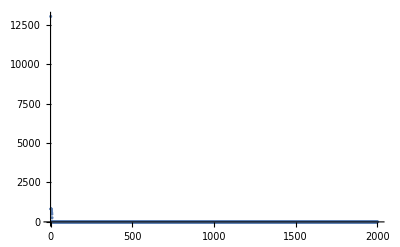

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[RHE,2];AppendTo[Solution30,Solution]]
```

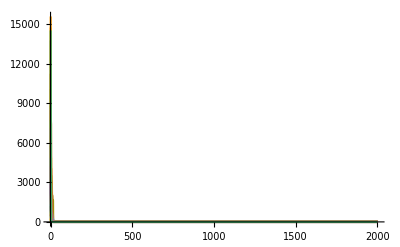

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{131.744,72.6801,72.6801,21.7681,11.5362,3.80413,3.79111,0.796132,0.783108,0.779872,0.658272,0.658272,0.653152,0.653152,0.000352,0.000352,0.000352,0.000288,0.000288,0.000072,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,8.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{15603.7,4877.39,4840.18,1327.39,449.891,404.827,404.827,164.587,9.58657,7.56257,6.50257,6.50257,6.00257,6.00257,0.202572,0.202532,0.202532,0.202532,0.202532,0.002532,0.002532,0.000132,0.000132,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{4993.86,1988.05,1414.09,929.28,699.637,538.931,499.248,431.597,363.19,322.584,204.671,152.93,126.074,98.7639,76.7733,9.90326,7.13588,6.24532,3.97763,3.86185,0.314111,0.0296847,0.0209586,0.0177668,0.0162594,0.003497,0.00322063,0.00195347,0.0017642,0.000947333,0.0003014,0.0001955,0.000146533,0.0000750667,0.0000683,0.0000625667,0.0000330333,0.0000325,0.0000155667,0.0000155,3.5×10^-6,3.5×10^-6,3.46667×10^-6,1.2×10^-6,1.06667×10^-6,1.06667×10^-6,1.06667×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

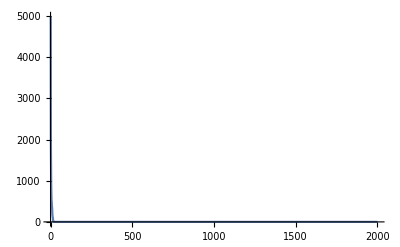

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{2893.95,1234.24,711.209,490.358,278.064,153.56,96.5747,51.4576,28.0471,27.1857,18.912,11.8458,3.49678,3.06509,0.397447,0.250873,0.181891,0.0310525,0.0304435,0.017802,0.0115,0.006993,0.0022965,0.0008885,0.000247,0.0001325,0.0001175,0.000107,0.000065,0.000016,8.5×10^-6,5.×10^-7,5.×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{5055.54,2139.34,1702.71,1047.63,864.872,807.833,805.326,752.954,615.537,576.623,394.446,333.064,328.062,320.989,300.017,25.8452,21.7738,21.925,18.6276,18.6192,1.54555,0.0657647,0.0647923,0.0644797,0.0646333,0.00697747,0.00658462,0.00467677,0.00460165,0.00374286,0.000681644,0.000522145,0.000398824,0.000225136,0.000225609,0.000224994,0.000134528,0.00013463,0.0000664902,0.0000665052,0.0000128459,0.0000128459,0.0000128539,5.8628×10^-6,5.84237×10^-6,5.84237×10^-6,5.84237×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*RHE 5D*)
```

```mathematica
GA[RHE,5]
```

0.

```mathematica
Solution
```

{306170.,237024.,109415.,99549.,99549.,62919.4,61022.9,47118.6,40642.4,39852.2,10423.,9831.03,9472.38,7352.2,6810.8,6002.87,3383.25,2580.15,2363.88,2105.25,2097.31,1473.65,1472.4,951.84,653.538,588.842,423.688,358.927,320.863,77.5993,17.4767,17.4278,13.3238,13.3224,4.71716,4.71716,4.68299,4.65883,4.30046,4.30046,4.29927,4.29927,3.75566,2.87215,2.87215,2.81603,2.81027,2.64703,2.56237,0.086674,0.086674,0.086674,0.077494,0.072534,0.072534,0.019282,0.019282,0.013734,0.013734,0.013734,0.011854,0.011854,0.011854,0.011854,0.005134,0.004334,0.004334,0.004294,0.004294,0.003934,0.003894,0.003894,0.000774,0.000374,0.000374,0.000349,0.000254,0.000254,0.000254,0.00023,0.00023,0.00023,0.00023,0.00023,0.000054,0.000054,0.000054,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,9.×10^-6,9.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

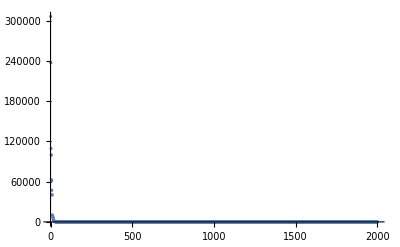

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[RHE,5];AppendTo[Solution30,Solution]]
```

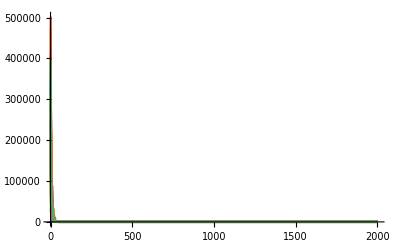

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{28864.5,25595.4,25531.8,18513.2,12320.2,11325.1,11325.1,10945.,5786.52,5786.52,5775.97,4068.5,4061.07,3539.16,3530.19,1820.38,1819.98,1448.4,1085.66,1058.61,798.539,732.466,533.531,348.139,321.087,234.811,97.2726,95.0651,95.0356,94.047,80.2413,80.2413,78.8333,78.8057,45.3613,45.3613,43.2417,43.2415,43.2194,42.8702,42.8702,42.3351,41.4839,41.4839,23.4908,23.4908,23.4908,19.7812,7.77077,1.32521,1.31759,0.46959,0.46959,0.434456,0.428572,0.404796,0.352696,0.352696,0.328254,0.328254,0.298072,0.298072,0.298072,0.298072,0.297556,0.253272,0.225624,0.225624,0.223608,0.069633,0.025944,0.017624,0.003224,0.003224,0.000824,0.000824,0.000824,0.000824,0.000824,0.000824,0.000824,0.000824,0.000824,0.000684,0.000684,0.000684,0.000684,0.000604,0.000604,0.000604,0.000604,0.000604,0.000604,0.000384,0.000384,0.000304,0.000304,0.000304,0.000304,0.000304,0.000304,0.000304,0.000304,0.000268,0.000268,0.000268,0.000268,0.000268,0.000268,0.000268,0.000268,0.000068,0.000068,0.000068,0.000068,0.000068,0.000064,0.000064,0.000064,0.000064,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,4.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{502839.,323253.,222796.,219177.,174574.,174506.,101397.,96759.5,80612.4,53766.4,49601.9,49153.9,48117.,48117.,20979.3,18053.4,6659.29,6653.69,5031.65,5031.65,5024.83,4898.5,3110.86,3097.68,3083.81,1888.83,1888.83,1356.45,1356.45,1336.19,1336.19,166.647,166.647,166.565,111.923,102.78,101.608,50.4684,50.4684,50.4684,15.5467,15.4556,15.4556,15.375,14.5692,13.1046,9.76744,9.76744,9.76744,9.76744,7.59304,6.70181,6.61112,6.61112,4.57568,4.57568,4.10682,4.1065,4.1065,0.002497,0.002497,0.002497,0.001457,0.001457,0.001457,0.000977,0.000977,0.000977,0.000337,0.000337,0.000337,0.000337,0.000317,0.000301,0.000301,0.000301,0.000293,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000021,0.000021,0.000021,0.000021,0.000021,0.000018,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,5.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{262631.,169813.,127393.,97827.7,72713.8,63334.8,53457.4,41956.,31072.9,25783.3,20800.,16684.8,15859.9,12018.,10054.7,9209.8,6563.98,5578.81,4944.25,4330.25,3710.5,2303.99,1916.44,1751.36,1480.56,1316.43,1106.75,982.586,577.,476.499,426.234,295.364,271.866,193.487,136.762,114.33,108.014,92.9841,69.377,65.8353,48.4208,44.2266,36.6162,32.6964,21.8956,20.1987,17.9034,14.0204,12.2176,11.261,10.7701,10.3119,10.0779,9.41056,4.71368,4.45697,4.19372,3.75294,1.66253,1.24209,1.16973,1.09271,1.03397,0.790932,0.728101,0.680142,0.577008,0.458804,0.450497,0.314023,0.307969,0.139662,0.125051,0.124278,0.115571,0.10327,0.0552677,0.0545839,0.0517189,0.0450319,0.0442668,0.0386367,0.0369806,0.0351928,0.0351488,0.0335854,0.033563,0.030515,0.00743813,0.00715077,0.00714547,0.00651233,0.00644073,0.0061351,0.0013839,0.00137413,0.00132927,0.0011466,0.00111487,0.00108247,0.0010611,0.00105957,0.00102483,0.000974433,0.000884233,0.000879867,0.000875867,0.000867467,0.000867133,0.0008578,0.000695367,0.000200167,0.000197433,0.000197267,0.000196433,0.0001943,0.000194033,0.000193833,0.000175033,0.000175033,0.000173033,0.000173033,0.0000254333,0.0000121,0.0000121,0.0000118333,0.0000117333,0.0000117333,0.0000112,0.0000111,4.43333×10^-6,4.3×10^-6,4.3×10^-6,3.76667×10^-6,3.76667×10^-6,3.63333×10^-6,3.63333×10^-6,3.23333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.13333×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.1×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.66667×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.5×10^-6,1.66667×10^-7,1.66667×10^-7,1.66667×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

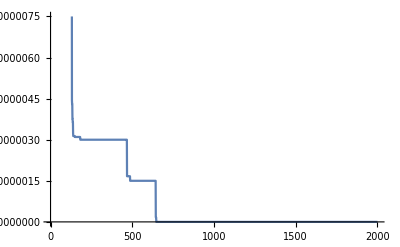

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{256560.,154277.,122213.,98675.8,58115.7,52950.2,46477.8,39396.1,24621.2,19335.2,15999.4,11178.9,10315.2,7778.67,7242.14,6024.28,5377.42,3333.94,2878.47,2626.9,2365.08,1395.24,1274.59,1223.66,840.896,621.648,586.021,381.407,269.807,159.381,143.619,124.686,105.11,74.4685,54.7064,48.0257,42.19,37.7001,32.8445,27.928,19.2959,19.0199,16.7675,13.2243,11.5,9.45986,4.64401,4.42665,3.0734,2.72136,2.13914,1.57671,0.942465,0.812305,0.791317,0.577402,0.415505,0.308236,0.256652,0.188179,0.164748,0.12323,0.086618,0.043156,0.0305155,0.0305155,0.029248,0.026714,0.0161955,0.01235,0.0113445,0.011015,0.007688,0.007108,0.0055055,0.0055055,0.0047255,0.002717,0.001489,0.001312,0.0012785,0.001,0.0008545,0.0006135,0.0004785,0.000468,0.0004495,0.0004055,0.000292,0.000204,0.000164,0.0001275,0.0001275,0.000089,0.000089,0.000089,0.000048,0.000044,0.0000415,0.0000415,0.00002,0.00002,0.00002,0.000017,0.000012,0.0000105,0.0000105,0.00001,0.00001,0.00001,6.5×10^-6,5.×10^-6,3.5×10^-6,3.5×10^-6,3.×10^-6,2.×10^-6,5.×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{112923.,78676.7,65559.3,61950.9,52059.1,47192.2,40764.7,32514.2,25218.6,21968.1,20050.3,15126.7,14871.2,12839.1,10242.7,9953.98,6954.22,6857.55,6528.28,5891.8,5561.13,2939.33,2364.05,2309.38,1990.78,1858.17,1821.33,1791.94,693.293,627.818,577.054,444.523,417.055,286.577,209.397,176.017,174.252,169.852,141.621,138.161,117.778,116.074,93.4575,93.3364,48.3791,48.3423,48.3047,31.5387,31.4556,30.5862,30.0471,30.0987,30.0885,29.0497,10.0478,10.0622,10.0857,9.82558,3.42367,3.24,2.98037,2.9588,2.82884,2.28486,2.28229,2.23248,1.87205,1.43621,1.42355,1.17674,1.17303,0.3736,0.339921,0.340042,0.319019,0.291712,0.154403,0.154542,0.151091,0.14404,0.144093,0.129071,0.128444,0.12493,0.124942,0.125068,0.125068,0.120323,0.0336904,0.0337368,0.0337279,0.031623,0.0316242,0.0316536,0.00566368,0.00566554,0.00567212,0.00490109,0.00490097,0.00490335,0.00490706,0.00490493,0.00490366,0.00490377,0.00453035,0.0045311,0.00453182,0.00453271,0.00453277,0.00452938,0.00365358,0.000981562,0.000982058,0.00098209,0.000982256,0.000982576,0.00098262,0.000982661,0.000880549,0.000880549,0.000880878,0.000880878,0.0000842687,0.0000381308,0.0000381308,0.0000381884,0.0000382135,0.0000382135,0.0000380321,0.0000380583,0.0000116136,0.0000116416,0.0000116416,0.0000114521,0.0000114521,0.0000114726,0.0000114726,0.0000113796,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000113949,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114028,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,0.0000114169,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.23505×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,8.21584×10^-6,9.12871×10^-7,9.12871×10^-7,9.12871×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*RHE 10D*)
```

```mathematica
GA[RHE,10]
```

0.

```mathematica
Solution
```

{1.66369×10^6,1.32617×10^6,1.22704×10^6,1.02275×10^6,939856.,936544.,674317.,674317.,461810.,457324.,453688.,440615.,436037.,401731.,381275.,340697.,244752.,235316.,171536.,171430.,157975.,129752.,119840.,110617.,75821.2,75821.1,57867.,55490.5,40682.4,40207.6,24427.2,24427.2,24426.8,23999.8,23410.3,22850.5,16740.4,14975.5,13693.9,12004.9,12004.4,10427.4,8526.45,8526.45,8151.23,7554.48,7550.29,6916.75,6909.46,6905.92,6775.58,6775.58,4679.76,4377.43,3560.18,3398.36,3357.36,2892.68,2892.68,2822.14,2803.01,2733.42,2446.37,2446.37,2439.34,2350.39,2349.27,1951.95,1951.86,1835.94,1591.4,1591.4,1590.18,1501.93,1496.77,1467.89,1457.46,1427.31,1427.31,1399.78,1399.78,1381.71,1365.79,1362.34,1362.34,1346.42,1342.58,1297.58,1297.58,1066.19,1066.16,931.421,931.421,740.879,740.879,530.972,246.74,224.467,224.467,224.467,214.318,214.318,180.098,180.098,132.361,128.924,122.363,122.363,120.496,118.065,116.153,72.961,72.9034,72.9034,69.2979,69.1795,67.2679,67.2679,67.1196,65.8016,65.7848,65.7848,63.614,63.4956,56.612,56.612,37.8803,37.8716,37.235,24.786,24.786,24.779,19.0939,18.9899,18.9899,18.9393,12.8513,9.18534,9.18534,9.18534,8.31498,8.31498,6.89984,6.89984,6.7696,6.7696,6.7696,6.73902,3.67341,3.67341,2.9296,2.9296,2.92,2.36941,2.36941,2.36941,2.36293,2.36293,2.32633,1.77977,1.75777,1.63541,1.41453,1.41453,1.41453,1.22675,1.22675,1.22675,1.22675,1.22675,1.15655,0.93245,0.93245,0.93245,0.93245,0.66457,0.66457,0.664058,0.664058,0.664058,0.512278,0.512278,0.512278,0.509758,0.509758,0.455078,0.455078,0.455078,0.455078,0.369478,0.369478,0.369478,0.369478,0.369478,0.354358,0.354358,0.354358,0.352518,0.306438,0.306438,0.224358,0.224358,0.224358,0.224298,0.224298,0.224298,0.224298,0.224298,0.224052,0.224052,0.204298,0.117866,0.117138,0.116938,0.116938,0.116938,0.116938,0.116938,0.116938,0.116938,0.116938,0.114538,0.114538,0.114538,0.102422,0.087622,0.07927,0.06511,0.06511,0.06511,0.06511,0.06511,0.064946,0.063558,0.063558,0.063558,0.063558,0.062386,0.062386,0.062386,0.025322,0.025322,0.025322,0.025322,0.024266,0.023722,0.023722,0.023722,0.023722,0.023722,0.023722,0.023722,0.023722,0.023722,0.023722,0.022938,0.022938,0.022938,0.022938,0.022938,0.022903,0.019175,0.019175,0.019175,0.019175,0.019175,0.019175,0.019175,0.018815,0.018815,0.018815,0.018815,0.018815,0.018815,0.018815,0.018815,0.01879,0.018655,0.018655,0.018655,0.018655,0.018566,0.017666,0.017666,0.017666,0.017666,0.017506,0.017506,0.015286,0.015286,0.015286,0.015286,0.015286,0.015258,0.002486,0.002486,0.002486,0.002486,0.002486,0.002486,0.002486,0.002486,0.002326,0.002326,0.002282,0.002282,0.002282,0.002282,0.002282,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000838,0.000788,0.000788,0.000788,0.000788,0.000788,0.000628,0.000628,0.000628,0.000628,0.000628,0.000628,0.000628,0.000608,0.000568,0.000568,0.000568,0.000568,0.000568,0.000568,0.000568,0.000568,0.000568,0.00052,0.00052,0.00052,0.00052,0.000472,0.000472,0.000472,0.000472,0.000472,0.000472,0.000472,0.000472,0.00046,0.000372,0.000372,0.000372,0.000372,0.000372,0.000372,0.000372,0.000372,0.000372,0.000362,0.000362,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000092,0.000084,0.000084,0.000084,0.000084,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.00006,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000036,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.000016,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*1 Solution plot*)
```

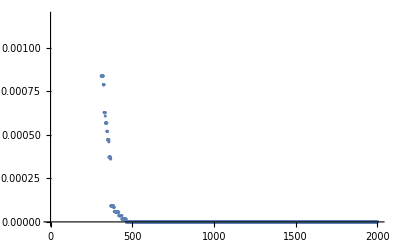

```mathematica
ListPlot@Solution
```

```mathematica
(*30x solutions plot*)
```

```mathematica
Solution30={}
```

{}

```mathematica
For[b=1,b<=30,b++,GA[RHE,10];AppendTo[Solution30,Solution]]
```

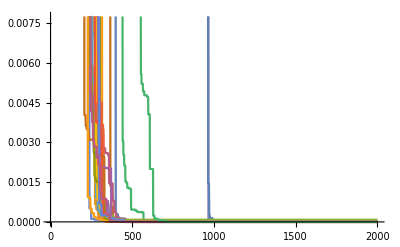

```mathematica
ListLinePlot@Solution30
```

```mathematica
best=Solution30[[First@Ordering[Solution30,1]]]
```

{592920.,539307.,539220.,538512.,458501.,457056.,452702.,426567.,392130.,289031.,283791.,236631.,236631.,227735.,226705.,199573.,198552.,189906.,184833.,184833.,152636.,152497.,139306.,119098.,119098.,119040.,108813.,104807.,104807.,66728.,60759.5,59287.7,56796.6,55059.5,34721.9,34720.6,32412.2,32375.8,30173.7,30173.4,28779.5,27648.1,25675.5,23638.8,23366.5,21381.3,20584.7,20584.7,18498.9,18246.7,17652.7,17028.4,16964.8,14281.3,14209.5,14180.,12731.8,12709.8,12000.3,10791.6,9768.21,9766.83,8676.42,8640.46,8631.71,8617.6,4861.03,4220.25,3310.98,3246.15,3107.49,2511.68,2457.33,2258.53,2258.53,2134.55,2134.55,2024.29,2024.29,1758.6,1750.59,1729.28,1729.28,1729.28,1712.11,1062.38,1062.38,755.689,755.689,753.772,744.021,740.484,740.484,471.73,436.862,436.862,432.392,414.811,414.043,413.051,399.907,399.907,397.556,295.986,246.157,246.157,226.314,226.314,226.314,158.545,158.545,158.508,157.376,157.376,155.828,155.828,146.353,133.579,112.54,111.772,102.635,102.635,98.0367,98.0367,98.0367,92.8826,84.0807,61.545,61.545,61.261,61.261,55.9414,50.5548,50.5548,50.5548,50.5548,50.4768,49.8687,49.8687,49.8687,48.5746,48.5746,48.5746,48.5746,46.1617,46.1617,39.4399,38.5235,37.5909,34.2215,34.2215,33.2069,33.1331,22.1523,21.7865,21.7865,21.0567,20.1143,20.1143,18.5624,18.5624,18.2495,18.2495,18.2495,18.1185,18.0872,10.6634,10.6634,10.6634,8.81542,8.81542,8.81542,8.81542,8.81542,8.13062,7.53589,7.52981,7.26149,7.26149,7.26145,5.9511,3.5098,3.5098,2.32901,1.95686,1.79204,1.79204,1.79204,1.79204,1.79204,1.54936,1.54936,1.54936,1.54936,1.4928,1.4928,1.4928,1.4928,0.916558,0.916558,0.916558,0.916558,0.916558,0.916558,0.909638,0.909638,0.896658,0.788638,0.788638,0.788638,0.788638,0.788638,0.494898,0.494898,0.494898,0.437778,0.437778,0.356778,0.356778,0.356778,0.328202,0.15036,0.15036,0.15036,0.150332,0.150332,0.143664,0.143664,0.139376,0.139376,0.139376,0.139376,0.139376,0.139376,0.139376,0.139376,0.139232,0.139232,0.057816,0.057816,0.057816,0.057816,0.057816,0.057816,0.057816,0.057816,0.057788,0.056812,0.056812,0.056812,0.056812,0.056179,0.016188,0.016188,0.016188,0.016188,0.016188,0.016188,0.016188,0.016188,0.015988,0.015988,0.015988,0.015988,0.015988,0.015988,0.01458,0.01458,0.01458,0.01458,0.01458,0.01458,0.01458,0.014308,0.014308,0.014308,0.014227,0.014227,0.012399,0.012399,0.012399,0.012399,0.010973,0.010973,0.010959,0.010959,0.010959,0.010877,0.010877,0.010877,0.010877,0.010877,0.010877,0.010877,0.010877,0.010877,0.008837,0.008837,0.008837,0.008837,0.008837,0.008837,0.008837,0.008837,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.008693,0.000373,0.000373,0.000373,0.000373,0.000373,0.000373,0.000373,0.000373,0.000373,0.000373,0.000293,0.000293,0.000293,0.000293,0.000293,0.000293,0.000293,0.000293,0.000293,0.000288,0.000288,0.000288,0.000288,0.000288,0.000288,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.00016,0.000128,0.000128,0.000128,0.000128,0.000128,0.000128,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.000064,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
worst=Solution30[[First@Ordering[Solution30,-1]]]
```

{2.55193×10^6,2.29762×10^6,2.064×10^6,1.89652×10^6,1.88205×10^6,1.85021×10^6,1.73539×10^6,1.72837×10^6,1.5595×10^6,1.55111×10^6,1.54402×10^6,1.54121×10^6,1.53268×10^6,1.48465×10^6,1.48388×10^6,1.43786×10^6,1.41234×10^6,1.3811×10^6,1.3811×10^6,1.38108×10^6,1.29614×10^6,1.29425×10^6,1.2645×10^6,1.26371×10^6,1.14607×10^6,1.14599×10^6,851686.,851686.,851516.,847656.,756064.,755679.,748789.,748789.,745768.,740713.,732570.,732570.,729182.,728659.,726151.,691923.,690404.,690253.,684082.,684011.,664171.,664058.,654940.,654940.,654896.,654896.,654059.,653008.,652679.,651035.,651024.,649763.,649763.,649759.,646347.,646322.,645773.,645430.,643010.,641344.,641344.,641197.,640610.,639144.,289473.,289252.,239985.,239774.,239168.,238597.,229224.,80216.7,80213.9,72374.1,55087.1,55087.1,31708.4,27498.3,26875.3,23034.4,23034.4,21128.7,21096.,21029.1,19116.6,18866.7,15333.7,15332.1,14355.5,14162.9,14061.6,13312.9,13252.2,12071.3,12070.6,11402.7,11402.7,9217.7,9217.7,8897.78,8897.78,8894.93,7193.18,6972.56,6798.66,6798.66,6063.23,5957.35,4783.11,4776.59,3216.61,3216.28,2937.17,2937.17,2615.97,2615.97,2200.26,2200.26,2200.26,2013.07,2013.07,2013.07,1963.99,1564.73,1553.21,1553.17,755.462,754.95,754.95,686.365,626.391,592.325,592.325,591.863,591.863,590.019,461.949,461.949,461.949,461.949,375.018,369.318,332.972,332.972,321.601,304.684,289.517,288.614,284.764,279.013,243.298,243.298,174.918,174.918,174.918,174.918,174.918,159.5,159.5,157.034,138.816,138.816,134.721,133.823,133.823,133.823,117.611,84.1728,84.1728,84.0748,83.6826,83.6826,77.2788,77.2788,77.2788,77.2772,70.22,70.22,61.9598,61.9598,61.9598,61.9598,61.9598,61.7157,61.7157,61.7157,52.7122,41.6962,39.6119,39.1966,37.3069,37.3069,37.3069,37.2884,27.9509,27.9509,27.2059,20.4069,20.4069,20.4069,20.4069,6.75473,6.75473,6.72383,6.72383,5.04721,5.04721,5.04721,4.68685,4.68685,4.68685,4.68685,2.74247,2.74247,2.63087,2.63087,1.26407,1.26407,1.19953,1.08793,1.08605,1.05505,0.712047,0.712047,0.706627,0.704527,0.604947,0.604947,0.604947,0.604947,0.604947,0.604947,0.604947,0.603027,0.601347,0.485427,0.485427,0.463347,0.463347,0.463347,0.463347,0.446547,0.446547,0.446547,0.446547,0.446547,0.446547,0.385755,0.385755,0.376979,0.376979,0.376755,0.361096,0.361096,0.360916,0.360276,0.360116,0.360116,0.360096,0.360096,0.360096,0.360096,0.360096,0.353396,0.353396,0.259716,0.259716,0.259716,0.259716,0.259716,0.246836,0.246836,0.246836,0.246836,0.246836,0.245492,0.216836,0.176676,0.176676,0.176676,0.176076,0.176076,0.134276,0.134276,0.134276,0.134244,0.131252,0.131192,0.131192,0.131192,0.131192,0.131192,0.13039,0.13039,0.130192,0.130192,0.12944,0.12944,0.12944,0.12944,0.12944,0.12944,0.12944,0.12944,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.09996,0.099944,0.099944,0.0993,0.0993,0.0993,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.01916,0.018544,0.018544,0.018544,0.018544,0.018256,0.018256,0.018256,0.018256,0.018256,0.018256,0.018256,0.01583,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015456,0.015411,0.015376,0.015366,0.015366,0.015366,0.015366,0.015366,0.014936,0.014926,0.014926,0.014926,0.014926,0.014926,0.014926,0.014881,0.014862,0.014862,0.014824,0.014824,0.014752,0.014752,0.014742,0.014742,0.014742,0.014742,0.014737,0.014737,0.014737,0.000342,0.000342,0.000342,0.000342,0.000342,0.00029,0.00029,0.00029,0.00029,0.00029,0.00029,0.00029,0.00029,0.000194,0.000194,0.000194,0.000194,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00013,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.00007,0.000069,0.000069,0.000069,0.000069,0.000069,0.000069,0.000069,0.000063,0.000063,0.000063,0.000063,0.000063,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.000055,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.000048,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
average=Mean@Solution30
```

{1.69475×10^6,1.38026×10^6,1.21845×10^6,1.02005×10^6,948038.,862426.,793905.,758446.,682443.,643405.,591415.,533577.,503767.,476696.,448160.,417403.,400261.,382739.,363124.,346869.,331162.,316808.,304989.,294031.,284540.,276994.,261033.,255425.,251528.,247139.,238930.,232342.,229469.,226306.,222646.,219850.,217216.,212843.,211394.,209185.,206707.,201641.,200675.,199311.,197171.,196140.,194815.,194176.,193239.,192663.,191691.,190886.,190414.,189344.,184371.,183076.,182517.,182217.,181753.,181359.,180116.,174220.,172454.,171988.,171742.,170697.,169532.,168458.,168075.,167850.,156095.,155919.,153940.,153851.,153679.,153609.,153207.,148151.,147977.,147581.,146875.,146795.,145871.,145598.,145523.,145314.,145279.,145182.,145174.,145152.,145073.,145056.,144866.,144842.,144798.,144778.,144757.,144714.,144706.,144653.,144637.,144599.,144537.,144459.,144440.,144426.,144417.,144411.,144349.,144332.,144319.,144318.,144273.,144266.,144223.,144220.,144161.,144160.,144147.,144147.,144134.,144132.,144117.,144114.,144113.,144105.,144103.,144102.,144097.,144082.,144079.,144079.,144051.,144049.,144048.,144044.,144039.,144037.,144033.,144033.,144032.,144032.,144026.,144026.,144025.,144025.,144021.,144021.,144019.,144018.,144018.,144016.,144016.,144015.,144014.,144013.,144012.,144012.,144010.,144009.,144009.,144009.,144009.,144008.,144008.,144008.,141717.,141653.,141653.,141489.,141427.,141111.,141110.,141109.,141046.,140866.,136709.,126581.,126548.,122716.,122716.,121991.,120954.,116869.,116812.,116812.,116731.,115576.,115495.,115416.,114193.,114126.,114126.,114125.,114119.,114119.,114119.,114080.,114069.,114069.,114062.,114062.,114057.,114057.,114057.,114056.,114056.,114055.,114055.,114055.,114055.,114055.,114055.,114055.,114055.,114055.,114055.,114001.,114001.,114001.,114001.,114001.,114001.,114001.,114000.,114000.,114000.,114000.,114000.,114000.,114000.,114000.,114000.,92667.1,92666.9,92257.5,90107.1,90107.1,90107.,90107.,90107.,90107.,90106.9,90106.9,90106.9,90106.9,90106.9,90106.9,90106.9,90106.9,90106.9,90106.9,90106.7,90106.7,87440.1,87440.1,87440.1,87440.1,87440.1,87436.4,87120.,87120.,87120.,87119.9,87119.9,87119.9,87115.1,87115.1,87115.1,87115.1,87115.1,87115.1,87114.3,87114.2,87108.4,87108.4,87001.8,87001.8,87001.8,87001.8,87001.8,87001.8,87001.7,87001.7,87000.9,87000.9,87000.6,87000.6,87000.6,87000.6,87000.5,87000.5,87000.5,87000.5,87000.5,87000.5,87000.5,87000.5,87000.5,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.1,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,87000.,68333.5,68333.5,68333.5,66871.4,66871.4,66871.4,66763.2,66404.8,66124.8,66124.8,66093.6,66093.6,66093.6,66093.6,66093.5,66093.5,66093.5,66093.5,66093.5,66093.5,66000.2,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,66000.,56666.7,56666.7,56666.7,56666.7,53040.1,53027.2,52053.7,51390.2,51373.5,51373.5,51373.3,51093.5,51093.5,51093.5,51093.4,51092.8,51023.6,51023.6,51023.6,51023.6,51023.6,51019.9,32437.5,32437.5,32437.5,32437.1,32437.1,32437.1,32437.1,32437.1,32437.1,32437.1,32437.1,32432.9,32432.9,32432.5,32413.9,32413.9,32413.9,32413.9,32413.9,32413.9,32333.8,32333.8,32333.8,32333.8,32333.8,32333.8,32333.8,32333.8,32333.8,32333.8,32333.5,32333.5,32331.1,31490.8,31490.8,31490.8,31210.4,31210.4,30018.9,30018.9,30018.9,30018.9,30018.9,30016.5,30016.4,30016.4,30016.4,30016.4,30016.4,30016.4,30001.1,30001.,30001.,30000.2,30000.2,30000.2,30000.2,30000.2,30000.2,30000.2,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.1,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,30000.,25306.7,25066.7,25066.7,25066.7,25047.7,25007.2,24648.8,24443.5,24431.2,24431.2,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24002.4,24000.3,24000.3,24000.3,24000.3,24000.3,24000.3,24000.3,24000.2,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,24000.,2133.34,2133.34,0.0082358,0.0082358,0.0082358,0.0082358,0.00690247,0.00690247,0.00690247,0.00690247,0.00656913,0.00656913,0.00656913,0.00656913,0.00509713,0.00509713,0.00509713,0.00509713,0.00509713,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.0024662,0.00246513,0.00246513,0.00246513,0.00246513,0.00246513,0.00113287,0.00105127,0.0000528667,0.0000528667,0.0000528667,0.0000528667,0.0000342,0.0000128667,0.0000128667,0.0000128667,9.46667×10^-6,9.46667×10^-6,9.46667×10^-6,9.46667×10^-6,8.86667×10^-6,8.86667×10^-6,8.86667×10^-6,8.86667×10^-6,8.86667×10^-6,8.86667×10^-6,8.86667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,7.26667×10^-6,4.6×10^-6,4.6×10^-6,4.6×10^-6,4.6×10^-6,4.6×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,4.06667×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,3.×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6,2.7×10^-6}

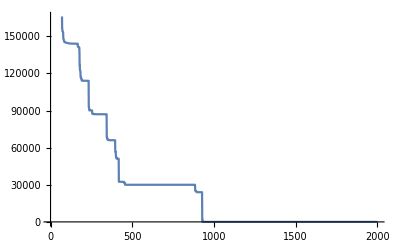

```mathematica
ListLinePlot@average
```

```mathematica
median=Median@Solution30
```

{1.74988×10^6,1.37804×10^6,1.20477×10^6,976597.,901140.,814223.,713837.,694764.,619698.,573422.,504527.,430539.,412330.,374267.,320144.,268211.,262178.,244842.,207664.,175727.,158442.,150398.,143087.,124795.,120319.,117271.,110464.,104720.,103881.,96738.7,90494.4,75033.7,70898.3,69496.9,50278.4,45102.3,41444.6,40346.1,38727.4,36386.9,29027.,23860.7,23003.7,20337.,20334.5,19396.3,17950.5,17867.8,16513.3,15964.5,13877.2,13189.3,12762.2,12556.2,12082.7,10418.7,9610.54,9607.71,8818.94,7686.36,7336.48,6655.,5572.24,5367.86,4911.93,4910.1,3840.61,3756.87,3357.39,2992.23,2782.25,2392.19,2253.59,2125.21,1988.57,1988.5,1725.09,1420.67,1309.48,1162.53,1151.05,1072.07,879.044,854.598,668.13,544.23,540.79,533.999,520.765,509.459,490.491,490.491,345.663,345.072,344.986,281.593,281.593,252.58,239.809,239.677,206.24,205.896,170.894,170.036,165.332,160.632,141.793,141.793,131.562,122.184,95.5688,95.5688,90.8361,84.3524,84.188,80.4359,68.944,68.944,64.7717,63.5645,63.5645,63.5392,63.408,61.1855,60.073,58.6421,58.6421,57.8521,43.353,39.0392,30.6446,30.518,30.517,29.8115,29.8115,25.2823,17.5272,17.3364,17.2128,17.2128,16.5574,15.5921,14.3012,10.2018,10.1936,9.92472,9.20288,8.22799,7.28321,7.12993,7.11486,6.65859,6.65859,5.30914,4.63384,4.03296,4.03014,3.87822,3.81103,3.80528,3.32706,3.30449,3.16506,3.16506,2.47033,2.43567,2.30967,2.30767,2.30679,2.30679,2.30472,2.30429,2.20518,1.97725,1.73752,1.72809,1.36996,1.35628,1.35494,1.33574,1.27726,1.12126,1.11496,0.793815,0.665141,0.665141,0.665141,0.665077,0.609825,0.609825,0.482925,0.45941,0.454963,0.454963,0.405982,0.322917,0.268304,0.261236,0.23752,0.23752,0.223231,0.223231,0.21215,0.208499,0.208099,0.203945,0.200796,0.180935,0.180935,0.175552,0.175507,0.174188,0.174188,0.1487,0.127754,0.127754,0.123617,0.104859,0.100816,0.0996035,0.0996035,0.0994955,0.0928185,0.090904,0.090904,0.090904,0.0859225,0.0857625,0.0854785,0.0809285,0.0809285,0.077863,0.077863,0.077863,0.066792,0.050776,0.050176,0.0375055,0.0375055,0.0360815,0.029727,0.029727,0.029727,0.029727,0.0293205,0.026035,0.026035,0.0260315,0.0246685,0.022696,0.022696,0.022696,0.0190675,0.0190675,0.0190675,0.01744,0.0153035,0.0153035,0.0153035,0.015016,0.014597,0.014597,0.014597,0.013149,0.013149,0.013149,0.013149,0.013149,0.013149,0.012954,0.012954,0.00931,0.0093,0.007448,0.007108,0.007108,0.004943,0.0047385,0.0046695,0.004633,0.0044815,0.004459,0.003902,0.003341,0.003321,0.003301,0.003301,0.003301,0.002764,0.0027635,0.0026365,0.002513,0.002513,0.002513,0.002513,0.002513,0.002513,0.0023265,0.0023265,0.0023265,0.0023265,0.0023265,0.002117,0.00176,0.0012825,0.0012825,0.0012825,0.0011395,0.0011395,0.0010695,0.000914,0.000914,0.000914,0.000914,0.000914,0.0008795,0.0008795,0.0008795,0.000661,0.000661,0.000542,0.000542,0.000542,0.000542,0.000464,0.0004605,0.0004605,0.0004605,0.0004555,0.0003925,0.0003925,0.0003145,0.00028,0.00028,0.0002715,0.0002715,0.0002715,0.0002715,0.0002715,0.0002715,0.000266,0.000261,0.00025,0.00025,0.00025,0.000234,0.000234,0.000234,0.000234,0.000234,0.000234,0.000229,0.000229,0.0002205,0.0002205,0.0002205,0.0002205,0.0002205,0.0002205,0.0002205,0.0002205,0.0001845,0.000153,0.000153,0.000153,0.000153,0.000153,0.0001495,0.000147,0.000124,0.0000825,0.0000825,0.0000765,0.0000765,0.0000765,0.0000765,0.0000765,0.0000765,0.000073,0.000073,0.000073,0.000073,0.000073,0.000073,0.000073,0.000073,0.000073,0.000073,0.0000685,0.0000685,0.000068,0.000068,0.000068,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000056,0.000054,0.000054,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.00005,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.000045,0.0000305,0.0000305,0.0000305,0.0000305,0.0000305,0.0000305,0.000022,0.000022,0.000022,0.0000165,0.0000165,0.0000165,0.0000165,0.0000165,0.0000165,0.0000165,0.0000165,0.0000165,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000014,0.000011,0.0000105,8.×10^-6,8.×10^-6,7.5×10^-6,7.5×10^-6,7.5×10^-6,7.5×10^-6,7.5×10^-6,7.5×10^-6,7.5×10^-6,5.5×10^-6,5.5×10^-6,4.5×10^-6,4.5×10^-6,2.5×10^-6,2.5×10^-6,2.5×10^-6,2.5×10^-6,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,5.×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
standarddeviation=StandardDeviation@Solution30
```

{471548.,424374.,377911.,355122.,376116.,351566.,347600.,351005.,329696.,332890.,340044.,360186.,360309.,361802.,363806.,352990.,358793.,349861.,352134.,356252.,348556.,344883.,344312.,346066.,332451.,334313.,312491.,311104.,310403.,311161.,306809.,309922.,307343.,307917.,309038.,309820.,309772.,304745.,304762.,305611.,305472.,304792.,305020.,304735.,304416.,304310.,303154.,302988.,302696.,302817.,302504.,302566.,302710.,302747.,304003.,304359.,304434.,304275.,304326.,304479.,304626.,306070.,306494.,306572.,306508.,306414.,306989.,307521.,307602.,307601.,295476.,295530.,294881.,294875.,294843.,294803.,294761.,294683.,294766.,294856.,295048.,295085.,295392.,295310.,295342.,295437.,295431.,295438.,295440.,295431.,295461.,295466.,295515.,295521.,295530.,295540.,295525.,295544.,295548.,295561.,295553.,295563.,295590.,295627.,295601.,295606.,295609.,295604.,295633.,295639.,295640.,295640.,295662.,295664.,295681.,295683.,295712.,295713.,295719.,295719.,295723.,295723.,295730.,295726.,295726.,295730.,295729.,295729.,295732.,295739.,295740.,295740.,295754.,295752.,295752.,295754.,295755.,295756.,295757.,295758.,295758.,295758.,295761.,295761.,295761.,295761.,295763.,295763.,295764.,295764.,295764.,295764.,295765.,295765.,295765.,295765.,295766.,295766.,295767.,295767.,295767.,295767.,295767.,295767.,295768.,295768.,289919.,289764.,289764.,289364.,289213.,288446.,288446.,288447.,288294.,287863.,278684.,263313.,263281.,260341.,260341.,259972.,259549.,259087.,259095.,259095.,259106.,259344.,259366.,259389.,259831.,259860.,259860.,259860.,259862.,259862.,259862.,259879.,259884.,259884.,259887.,259887.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259890.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,259915.,233370.,233370.,233404.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,233934.,226855.,226855.,226855.,226855.,226855.,226846.,226054.,226054.,226054.,226054.,226054.,226054.,226042.,226042.,226042.,226042.,226042.,226042.,226040.,226040.,226026.,226026.,226067.,226067.,226067.,226067.,226067.,226067.,226067.,226067.,226065.,226065.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226064.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,226063.,201462.,201462.,201462.,201608.,201608.,201608.,201632.,201722.,201806.,201806.,201816.,201816.,201816.,201816.,201816.,201816.,201816.,201816.,201816.,201816.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,201847.,180179.,180179.,180179.,180179.,175094.,175080.,174078.,173486.,173472.,173472.,173472.,173245.,173245.,173245.,173245.,173244.,173190.,173190.,173190.,173190.,173190.,173188.,134512.,134512.,134512.,134511.,134511.,134511.,134511.,134511.,134511.,134511.,134511.,134510.,134510.,134510.,134489.,134489.,134489.,134489.,134489.,134489.,134465.,134465.,134465.,134465.,134465.,134465.,134465.,134465.,134465.,134465.,134464.,134464.,134464.,134299.,134299.,134299.,134280.,134280.,134391.,134391.,134391.,134391.,134391.,134392.,134392.,134392.,134392.,134392.,134392.,134392.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,134395.,131401.,131382.,131382.,131382.,131381.,131379.,131379.,131392.,131393.,131393.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,131453.,11684.7,11684.7,0.0393924,0.0393924,0.0393924,0.0393924,0.0321919,0.0321919,0.0321919,0.0321919,0.0303994,0.0303994,0.0303994,0.0303994,0.0225477,0.0225477,0.0225477,0.0225477,0.0225477,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944877,0.00944422,0.00944422,0.00944422,0.00944422,0.00944422,0.00592045,0.005474,0.000265737,0.000265737,0.000265737,0.000265737,0.000163832,0.0000491119,0.0000491119,0.0000491119,0.0000322712,0.0000322712,0.0000322712,0.0000322712,0.0000295223,0.0000295223,0.0000295223,0.0000295223,0.0000295223,0.0000295223,0.0000295223,0.0000286151,0.0000286151,0.0000286151,0.0000286151,0.0000286151,0.0000286151,0.0000286151,0.0000286151,0.0000177872,0.0000177872,0.0000177872,0.0000177872,0.0000177872,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000163432,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000148231,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885,0.0000147885}